```mathematica
NumberToConstraint6[val_, vertices_]:=Block[
{n=IntegerDigits[val,4,Length[vertices]],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[vertices[[i]]]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,Length[vertices]}];
res]
```

```mathematica
NumberToConstraint6[3,{1,2}]
```

x1==1 && x2==4

```mathematica
CountSolutions6[g_,edges1_,edges2_,edge3_, n_, vertices_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2,edge3}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraint6[n, vertices];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=ToVars2[EdgeAdd[g,edge3],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
Print[{ n,IntegerDigits[n,4,Length[vertices]]+1,If[Total[Take[result3,{4,7}]]>0,Style[result3,Red],result3]}];
{ n,IntegerDigits[n,4,Length[vertices]]+1,result3}
]
```

```mathematica
DistributeDefinitions[{CountSolutions6,NumberToConstraint6,ToVars2,expMixedBisWithHair}]
```

{CountSolutions6}

```mathematica
AssignColors6[l_, vertices_]:=Block[{result,i},
result=Association[];
For[i=1,i≤Length[l],i++,
result[vertices[[i]]]=l[[i]]
];
ToColors2[result]
]
```

```mathematica
DistributeDefinitions[CountSolutions6,NumberToConstraint6,AssignColors6]
```

{AssignColors6,ToColors2,IndexToColor}

```mathematica
AbsoluteTiming[
TableForm[
ParallelTable[CountSolutions6[expMixedBis,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15}],{k,0,1024-1}], TableDepth->2
]
]
```

```mathematica
NumberToConstraintFour[val_, vertices_]:=Block[
{n=IntegerDigits[val,4,Length[vertices]],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[vertices[[i]]]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,Length[vertices]}];
res]
```

```mathematica
NumberToConstraintFour[3,{1,2}]
```

x1==1 && x2==4

```mathematica
CountSolutionsFour[g_,edges1_,edges2_, n_, vertices_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraintFour[n, vertices];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
{ n,IntegerDigits[n,4,4]+1,result3}
]
```

```mathematica
CountSolutionsFour[expMixedBisFour,{1<->2},{2<->3},0,{9,10,11,12}]
```

{0,{1,1,1,1},{0,0,288}}

```mathematica
4^5
```

1024

```mathematica
AbsoluteTiming[
TableForm[
Monitor[Table[CountSolutionsFour[expMixedBisFour,{1<->3},{2<->4},k,{9,10,11,12}],{k,0,4^4}],k], TableDepth->2
]
]
```

{1577.38,0 | {1,1,1,1} | {96,96,0}
1 | {1,1,1,2} | {8,8,0}
2 | {1,1,1,3} | {8,8,0}
3 | {1,1,1,4} | {8,8,0}
4 | {1,1,2,1} | {8,8,0}
5 | {1,1,2,2} | {0,24,8}
6 | {1,1,2,3} | {2,4,6}
7 | {1,1,2,4} | {2,4,6}
8 | {1,1,3,1} | {8,8,0}
9 | {1,1,3,2} | {2,4,6}
10 | {1,1,3,3} | {0,24,8}
11 | {1,1,3,4} | {2,4,6}
12 | {1,1,4,1} | {8,8,0}
13 | {1,1,4,2} | {2,4,6}
14 | {1,1,4,3} | {2,4,6}
15 | {1,1,4,4} | {0,24,8}
16 | {1,2,1,1} | {8,8,0}
17 | {1,2,1,2} | {0,0,0}
18 | {1,2,1,3} | {1,1,0}
19 | {1,2,1,4} | {1,1,0}
20 | {1,2,2,1} | {24,0,8}
21 | {1,2,2,2} | {8,8,0}
22 | {1,2,2,3} | {4,2,6}
23 | {1,2,2,4} | {4,2,6}
24 | {1,2,3,1} | {4,2,6}
25 | {1,2,3,2} | {1,1,0}
26 | {1,2,3,3} | {2,4,6}
27 | {1,2,3,4} | {0,0,2}
28 | {1,2,4,1} | {4,2,6}
29 | {1,2,4,2} | {1,1,0}
30 | {1,2,4,3} | {0,0,2}
31 | {1,2,4,4} | {2,4,6}
32 | {1,3,1,1} | {8,8,0}
33 | {1,3,1,2} | {1,1,0}
34 | {1,3,1,3} | {0,0,0}
35 | {1,3,1,4} | {1,1,0}
36 | {1,3,2,1} | {4,2,6}
37 | {1,3,2,2} | {2,4,6}
38 | {1,3,2,3} | {1,1,0}
39 | {1,3,2,4} | {0,0,2}
40 | {1,3,3,1} | {24,0,8}
41 | {1,3,3,2} | {4,2,6}
42 | {1,3,3,3} | {8,8,0}
43 | {1,3,3,4} | {4,2,6}
44 | {1,3,4,1} | {4,2,6}
45 | {1,3,4,2} | {0,0,2}
46 | {1,3,4,3} | {1,1,0}
47 | {1,3,4,4} | {2,4,6}
48 | {1,4,1,1} | {8,8,0}
49 | {1,4,1,2} | {1,1,0}
50 | {1,4,1,3} | {1,1,0}
51 | {1,4,1,4} | {0,0,0}
52 | {1,4,2,1} | {4,2,6}
53 | {1,4,2,2} | {2,4,6}
54 | {1,4,2,3} | {0,0,2}
55 | {1,4,2,4} | {1,1,0}
56 | {1,4,3,1} | {4,2,6}
57 | {1,4,3,2} | {0,0,2}
58 | {1,4,3,3} | {2,4,6}
59 | {1,4,3,4} | {1,1,0}
60 | {1,4,4,1} | {24,0,8}
61 | {1,4,4,2} | {4,2,6}
62 | {1,4,4,3} | {4,2,6}
63 | {1,4,4,4} | {8,8,0}
64 | {2,1,1,1} | {8,8,0}
65 | {2,1,1,2} | {24,0,8}
66 | {2,1,1,3} | {4,2,6}
67 | {2,1,1,4} | {4,2,6}
68 | {2,1,2,1} | {0,0,0}
69 | {2,1,2,2} | {8,8,0}
70 | {2,1,2,3} | {1,1,0}
71 | {2,1,2,4} | {1,1,0}
72 | {2,1,3,1} | {1,1,0}
73 | {2,1,3,2} | {4,2,6}
74 | {2,1,3,3} | {2,4,6}
75 | {2,1,3,4} | {0,0,2}
76 | {2,1,4,1} | {1,1,0}
77 | {2,1,4,2} | {4,2,6}
78 | {2,1,4,3} | {0,0,2}
79 | {2,1,4,4} | {2,4,6}
80 | {2,2,1,1} | {0,24,8}
81 | {2,2,1,2} | {8,8,0}
82 | {2,2,1,3} | {2,4,6}
83 | {2,2,1,4} | {2,4,6}
84 | {2,2,2,1} | {8,8,0}
85 | {2,2,2,2} | {96,96,0}
86 | {2,2,2,3} | {8,8,0}
87 | {2,2,2,4} | {8,8,0}
88 | {2,2,3,1} | {2,4,6}
89 | {2,2,3,2} | {8,8,0}
90 | {2,2,3,3} | {0,24,8}
91 | {2,2,3,4} | {2,4,6}
92 | {2,2,4,1} | {2,4,6}
93 | {2,2,4,2} | {8,8,0}
94 | {2,2,4,3} | {2,4,6}
95 | {2,2,4,4} | {0,24,8}
96 | {2,3,1,1} | {2,4,6}
97 | {2,3,1,2} | {4,2,6}
98 | {2,3,1,3} | {1,1,0}
99 | {2,3,1,4} | {0,0,2}
100 | {2,3,2,1} | {1,1,0}
101 | {2,3,2,2} | {8,8,0}
102 | {2,3,2,3} | {0,0,0}
103 | {2,3,2,4} | {1,1,0}
104 | {2,3,3,1} | {4,2,6}
105 | {2,3,3,2} | {24,0,8}
106 | {2,3,3,3} | {8,8,0}
107 | {2,3,3,4} | {4,2,6}
108 | {2,3,4,1} | {0,0,2}
109 | {2,3,4,2} | {4,2,6}
110 | {2,3,4,3} | {1,1,0}
111 | {2,3,4,4} | {2,4,6}
112 | {2,4,1,1} | {2,4,6}
113 | {2,4,1,2} | {4,2,6}
114 | {2,4,1,3} | {0,0,2}
115 | {2,4,1,4} | {1,1,0}
116 | {2,4,2,1} | {1,1,0}
117 | {2,4,2,2} | {8,8,0}
118 | {2,4,2,3} | {1,1,0}
119 | {2,4,2,4} | {0,0,0}
120 | {2,4,3,1} | {0,0,2}
121 | {2,4,3,2} | {4,2,6}
122 | {2,4,3,3} | {2,4,6}
123 | {2,4,3,4} | {1,1,0}
124 | {2,4,4,1} | {4,2,6}
125 | {2,4,4,2} | {24,0,8}
126 | {2,4,4,3} | {4,2,6}
127 | {2,4,4,4} | {8,8,0}
128 | {3,1,1,1} | {8,8,0}
129 | {3,1,1,2} | {4,2,6}
130 | {3,1,1,3} | {24,0,8}
131 | {3,1,1,4} | {4,2,6}
132 | {3,1,2,1} | {1,1,0}
133 | {3,1,2,2} | {2,4,6}
134 | {3,1,2,3} | {4,2,6}
135 | {3,1,2,4} | {0,0,2}
136 | {3,1,3,1} | {0,0,0}
137 | {3,1,3,2} | {1,1,0}
138 | {3,1,3,3} | {8,8,0}
139 | {3,1,3,4} | {1,1,0}
140 | {3,1,4,1} | {1,1,0}
141 | {3,1,4,2} | {0,0,2}
142 | {3,1,4,3} | {4,2,6}
143 | {3,1,4,4} | {2,4,6}
144 | {3,2,1,1} | {2,4,6}
145 | {3,2,1,2} | {1,1,0}
146 | {3,2,1,3} | {4,2,6}
147 | {3,2,1,4} | {0,0,2}
148 | {3,2,2,1} | {4,2,6}
149 | {3,2,2,2} | {8,8,0}
150 | {3,2,2,3} | {24,0,8}
151 | {3,2,2,4} | {4,2,6}
152 | {3,2,3,1} | {1,1,0}
153 | {3,2,3,2} | {0,0,0}
154 | {3,2,3,3} | {8,8,0}
155 | {3,2,3,4} | {1,1,0}
156 | {3,2,4,1} | {0,0,2}
157 | {3,2,4,2} | {1,1,0}
158 | {3,2,4,3} | {4,2,6}
159 | {3,2,4,4} | {2,4,6}
160 | {3,3,1,1} | {0,24,8}
161 | {3,3,1,2} | {2,4,6}
162 | {3,3,1,3} | {8,8,0}
163 | {3,3,1,4} | {2,4,6}
164 | {3,3,2,1} | {2,4,6}
165 | {3,3,2,2} | {0,24,8}
166 | {3,3,2,3} | {8,8,0}
167 | {3,3,2,4} | {2,4,6}
168 | {3,3,3,1} | {8,8,0}
169 | {3,3,3,2} | {8,8,0}
170 | {3,3,3,3} | {96,96,0}
171 | {3,3,3,4} | {8,8,0}
172 | {3,3,4,1} | {2,4,6}
173 | {3,3,4,2} | {2,4,6}
174 | {3,3,4,3} | {8,8,0}
175 | {3,3,4,4} | {0,24,8}
176 | {3,4,1,1} | {2,4,6}
177 | {3,4,1,2} | {0,0,2}
178 | {3,4,1,3} | {4,2,6}
179 | {3,4,1,4} | {1,1,0}
180 | {3,4,2,1} | {0,0,2}
181 | {3,4,2,2} | {2,4,6}
182 | {3,4,2,3} | {4,2,6}
183 | {3,4,2,4} | {1,1,0}
184 | {3,4,3,1} | {1,1,0}
185 | {3,4,3,2} | {1,1,0}
186 | {3,4,3,3} | {8,8,0}
187 | {3,4,3,4} | {0,0,0}
188 | {3,4,4,1} | {4,2,6}
189 | {3,4,4,2} | {4,2,6}
190 | {3,4,4,3} | {24,0,8}
191 | {3,4,4,4} | {8,8,0}
192 | {4,1,1,1} | {8,8,0}
193 | {4,1,1,2} | {4,2,6}
194 | {4,1,1,3} | {4,2,6}
195 | {4,1,1,4} | {24,0,8}
196 | {4,1,2,1} | {1,1,0}
197 | {4,1,2,2} | {2,4,6}
198 | {4,1,2,3} | {0,0,2}
199 | {4,1,2,4} | {4,2,6}
200 | {4,1,3,1} | {1,1,0}
201 | {4,1,3,2} | {0,0,2}
202 | {4,1,3,3} | {2,4,6}
203 | {4,1,3,4} | {4,2,6}
204 | {4,1,4,1} | {0,0,0}
205 | {4,1,4,2} | {1,1,0}
206 | {4,1,4,3} | {1,1,0}
207 | {4,1,4,4} | {8,8,0}
208 | {4,2,1,1} | {2,4,6}
209 | {4,2,1,2} | {1,1,0}
210 | {4,2,1,3} | {0,0,2}
211 | {4,2,1,4} | {4,2,6}
212 | {4,2,2,1} | {4,2,6}
213 | {4,2,2,2} | {8,8,0}
214 | {4,2,2,3} | {4,2,6}
215 | {4,2,2,4} | {24,0,8}
216 | {4,2,3,1} | {0,0,2}
217 | {4,2,3,2} | {1,1,0}
218 | {4,2,3,3} | {2,4,6}
219 | {4,2,3,4} | {4,2,6}
220 | {4,2,4,1} | {1,1,0}
221 | {4,2,4,2} | {0,0,0}
222 | {4,2,4,3} | {1,1,0}
223 | {4,2,4,4} | {8,8,0}
224 | {4,3,1,1} | {2,4,6}
225 | {4,3,1,2} | {0,0,2}
226 | {4,3,1,3} | {1,1,0}
227 | {4,3,1,4} | {4,2,6}
228 | {4,3,2,1} | {0,0,2}
229 | {4,3,2,2} | {2,4,6}
230 | {4,3,2,3} | {1,1,0}
231 | {4,3,2,4} | {4,2,6}
232 | {4,3,3,1} | {4,2,6}
233 | {4,3,3,2} | {4,2,6}
234 | {4,3,3,3} | {8,8,0}
235 | {4,3,3,4} | {24,0,8}
236 | {4,3,4,1} | {1,1,0}
237 | {4,3,4,2} | {1,1,0}
238 | {4,3,4,3} | {0,0,0}
239 | {4,3,4,4} | {8,8,0}
240 | {4,4,1,1} | {0,24,8}
241 | {4,4,1,2} | {2,4,6}
242 | {4,4,1,3} | {2,4,6}
243 | {4,4,1,4} | {8,8,0}
244 | {4,4,2,1} | {2,4,6}
245 | {4,4,2,2} | {0,24,8}
246 | {4,4,2,3} | {2,4,6}
247 | {4,4,2,4} | {8,8,0}
248 | {4,4,3,1} | {2,4,6}
249 | {4,4,3,2} | {2,4,6}
250 | {4,4,3,3} | {0,24,8}
251 | {4,4,3,4} | {8,8,0}
252 | {4,4,4,1} | {8,8,0}
253 | {4,4,4,2} | {8,8,0}
254 | {4,4,4,3} | {8,8,0}
255 | {4,4,4,4} | {96,96,0}
256 | {1,1,1,1} | {96,96,0}}

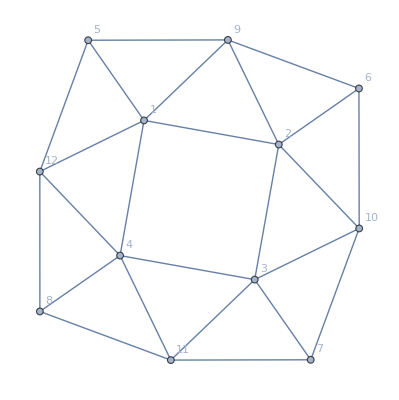

```mathematica
expMixedBisFour=With[
{n=4},
Graph[EdgeAdd[CycleGraph[n],Flatten[
Table[{
i<->i+n,
Mod[i,n]+1<->i+2*n,
i+2*n<->i+n,
i+2*n<->Mod[i,n]+n+1,
i<->i+2*n
},{i,1,n}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
]
```

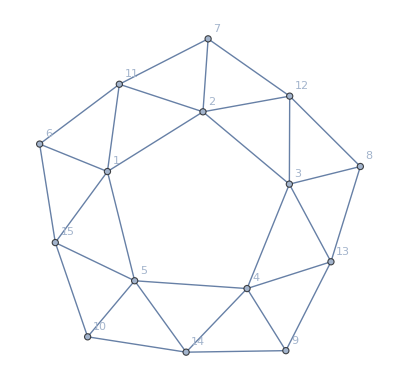

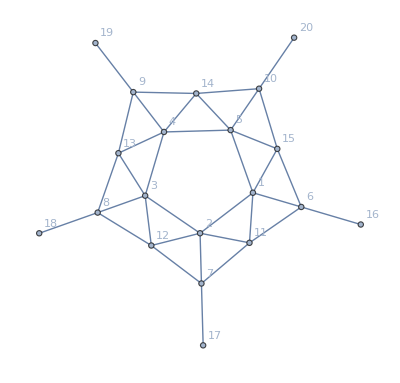

```mathematica
expMixedBis=With[
{n=5},
Graph[EdgeAdd[CycleGraph[n],Flatten[
Table[{
i<->i+n,
Mod[i,n]+1<->i+2*n,
i+2*n<->i+n,
i+2*n<->Mod[i,n]+n+1,
i<->i+2*n
},{i,1,n}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
]
```

```mathematica
CountSolutions6[expMixedBis,{1<->2},{2<->4,2<->5},{3<->5},0,{11,12,13,14,15}]
```

{0,{1,1,1,1,1},{192,0,0,192,0,576}}

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[expMixedBis,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15}],{k,0,1024-1}],k], TableDepth->2
]
]
```

{11584.3,0 | {1,1,1,1,1} | {192,192,576,0,0,0}
1 | {1,1,1,1,2} | {16,16,48,0,0,0}
2 | {1,1,1,1,3} | {16,16,48,0,0,0}
3 | {1,1,1,1,4} | {16,16,48,0,0,0}
4 | {1,1,1,2,1} | {16,16,48,0,0,0}
5 | {1,1,1,2,2} | {0,16,32,0,48,16}
6 | {1,1,1,2,3} | {4,0,20,0,20,12}
7 | {1,1,1,2,4} | {4,0,20,0,20,12}
8 | {1,1,1,3,1} | {16,16,48,0,0,0}
9 | {1,1,1,3,2} | {4,0,20,0,20,12}
10 | {1,1,1,3,3} | {0,16,32,0,48,16}
11 | {1,1,1,3,4} | {4,0,20,0,20,12}
12 | {1,1,1,4,1} | {16,16,48,0,0,0}
13 | {1,1,1,4,2} | {4,0,20,0,20,12}
14 | {1,1,1,4,3} | {4,0,20,0,20,12}
15 | {1,1,1,4,4} | {0,16,32,0,48,16}
16 | {1,1,2,1,1} | {16,16,48,0,0,0}
17 | {1,1,2,1,2} | {0,4,0,0,0,0}
18 | {1,1,2,1,3} | {2,0,6,0,0,0}
19 | {1,1,2,1,4} | {2,0,6,0,0,0}
20 | {1,1,2,2,1} | {16,16,16,32,16,16}
21 | {1,1,2,2,2} | {0,16,32,16,48,0}
22 | {1,1,2,2,3} | {4,0,4,4,8,12}
23 | {1,1,2,2,4} | {4,0,4,4,8,12}
24 | {1,1,2,3,1} | {0,0,24,8,12,12}
25 | {1,1,2,3,2} | {0,0,4,2,6,0}
26 | {1,1,2,3,3} | {0,0,8,4,8,12}
27 | {1,1,2,3,4} | {0,0,8,0,4,4}
28 | {1,1,2,4,1} | {0,0,24,8,12,12}
29 | {1,1,2,4,2} | {0,0,4,2,6,0}
30 | {1,1,2,4,3} | {0,0,8,0,4,4}
31 | {1,1,2,4,4} | {0,0,8,4,8,12}
32 | {1,1,3,1,1} | {16,16,48,0,0,0}
33 | {1,1,3,1,2} | {2,0,6,0,0,0}
34 | {1,1,3,1,3} | {0,4,0,0,0,0}
35 | {1,1,3,1,4} | {2,0,6,0,0,0}
36 | {1,1,3,2,1} | {0,0,24,8,12,12}
37 | {1,1,3,2,2} | {0,0,8,4,8,12}
38 | {1,1,3,2,3} | {0,0,4,2,6,0}
39 | {1,1,3,2,4} | {0,0,8,0,4,4}
40 | {1,1,3,3,1} | {16,16,16,32,16,16}
41 | {1,1,3,3,2} | {4,0,4,4,8,12}
42 | {1,1,3,3,3} | {0,16,32,16,48,0}
43 | {1,1,3,3,4} | {4,0,4,4,8,12}
44 | {1,1,3,4,1} | {0,0,24,8,12,12}
45 | {1,1,3,4,2} | {0,0,8,0,4,4}
46 | {1,1,3,4,3} | {0,0,4,2,6,0}
47 | {1,1,3,4,4} | {0,0,8,4,8,12}
48 | {1,1,4,1,1} | {16,16,48,0,0,0}
49 | {1,1,4,1,2} | {2,0,6,0,0,0}
50 | {1,1,4,1,3} | {2,0,6,0,0,0}
51 | {1,1,4,1,4} | {0,4,0,0,0,0}
52 | {1,1,4,2,1} | {0,0,24,8,12,12}
53 | {1,1,4,2,2} | {0,0,8,4,8,12}
54 | {1,1,4,2,3} | {0,0,8,0,4,4}
55 | {1,1,4,2,4} | {0,0,4,2,6,0}
56 | {1,1,4,3,1} | {0,0,24,8,12,12}
57 | {1,1,4,3,2} | {0,0,8,0,4,4}
58 | {1,1,4,3,3} | {0,0,8,4,8,12}
59 | {1,1,4,3,4} | {0,0,4,2,6,0}
60 | {1,1,4,4,1} | {16,16,16,32,16,16}
61 | {1,1,4,4,2} | {4,0,4,4,8,12}
62 | {1,1,4,4,3} | {4,0,4,4,8,12}
63 | {1,1,4,4,4} | {0,16,32,16,48,0}
64 | {1,2,1,1,1} | {16,16,48,0,0,0}
65 | {1,2,1,1,2} | {0,0,4,0,0,0}
66 | {1,2,1,1,3} | {2,2,4,0,0,0}
67 | {1,2,1,1,4} | {2,2,4,0,0,0}
68 | {1,2,1,2,1} | {4,0,0,0,0,0}
69 | {1,2,1,2,2} | {0,0,4,0,0,0}
70 | {1,2,1,2,3} | {1,0,1,0,0,2}
71 | {1,2,1,2,4} | {1,0,1,0,0,2}
72 | {1,2,1,3,1} | {0,2,6,0,0,0}
73 | {1,2,1,3,2} | {0,0,2,0,2,0}
74 | {1,2,1,3,3} | {0,2,2,0,6,2}
75 | {1,2,1,3,4} | {0,0,2,0,3,1}
76 | {1,2,1,4,1} | {0,2,6,0,0,0}
77 | {1,2,1,4,2} | {0,0,2,0,2,0}
78 | {1,2,1,4,3} | {0,0,2,0,3,1}
79 | {1,2,1,4,4} | {0,2,2,0,6,2}
80 | {1,2,2,1,1} | {16,0,32,0,16,48}
81 | {1,2,2,1,2} | {0,0,4,0,0,0}
82 | {1,2,2,1,3} | {2,0,2,0,2,6}
83 | {1,2,2,1,4} | {2,0,2,0,2,6}
84 | {1,2,2,2,1} | {16,0,32,16,0,48}
85 | {1,2,2,2,2} | {16,16,48,0,0,0}
86 | {1,2,2,2,3} | {16,4,4,12,0,20}
87 | {1,2,2,2,4} | {16,4,4,12,0,20}
88 | {1,2,2,3,1} | {0,0,8,4,12,8}
89 | {1,2,2,3,2} | {2,2,4,0,0,0}
90 | {1,2,2,3,3} | {4,4,0,8,8,8}
91 | {1,2,2,3,4} | {4,0,4,2,2,4}
92 | {1,2,2,4,1} | {0,0,8,4,12,8}
93 | {1,2,2,4,2} | {2,2,4,0,0,0}
94 | {1,2,2,4,3} | {4,0,4,2,2,4}
95 | {1,2,2,4,4} | {4,4,0,8,8,8}
96 | {1,2,3,1,1} | {0,4,20,0,12,20}
97 | {1,2,3,1,2} | {0,0,2,0,0,2}
98 | {1,2,3,1,3} | {0,1,1,0,2,0}
99 | {1,2,3,1,4} | {0,0,2,0,1,3}
100 | {1,2,3,2,1} | {0,0,4,2,0,6}
101 | {1,2,3,2,2} | {2,2,4,0,0,0}
102 | {1,2,3,2,3} | {1,1,0,2,0,0}
103 | {1,2,3,2,4} | {2,0,0,1,0,3}
104 | {1,2,3,3,1} | {0,4,4,4,12,8}
105 | {1,2,3,3,2} | {2,2,0,4,2,2}
106 | {1,2,3,3,3} | {4,16,4,12,20,0}
107 | {1,2,3,3,4} | {4,4,0,4,2,2}
108 | {1,2,3,4,1} | {0,0,8,0,4,4}
109 | {1,2,3,4,2} | {0,0,2,2,1,1}
110 | {1,2,3,4,3} | {0,2,0,1,3,0}
111 | {1,2,3,4,4} | {0,4,4,2,4,2}
112 | {1,2,4,1,1} | {0,4,20,0,12,20}
113 | {1,2,4,1,2} | {0,0,2,0,0,2}
114 | {1,2,4,1,3} | {0,0,2,0,1,3}
115 | {1,2,4,1,4} | {0,1,1,0,2,0}
116 | {1,2,4,2,1} | {0,0,4,2,0,6}
117 | {1,2,4,2,2} | {2,2,4,0,0,0}
118 | {1,2,4,2,3} | {2,0,0,1,0,3}
119 | {1,2,4,2,4} | {1,1,0,2,0,0}
120 | {1,2,4,3,1} | {0,0,8,0,4,4}
121 | {1,2,4,3,2} | {0,0,2,2,1,1}
122 | {1,2,4,3,3} | {0,4,4,2,4,2}
123 | {1,2,4,3,4} | {0,2,0,1,3,0}
124 | {1,2,4,4,1} | {0,4,4,4,12,8}
125 | {1,2,4,4,2} | {2,2,0,4,2,2}
126 | {1,2,4,4,3} | {4,4,0,4,2,2}
127 | {1,2,4,4,4} | {4,16,4,12,20,0}
128 | {1,3,1,1,1} | {16,16,48,0,0,0}
129 | {1,3,1,1,2} | {2,2,4,0,0,0}
130 | {1,3,1,1,3} | {0,0,4,0,0,0}
131 | {1,3,1,1,4} | {2,2,4,0,0,0}
132 | {1,3,1,2,1} | {0,2,6,0,0,0}
133 | {1,3,1,2,2} | {0,2,2,0,6,2}
134 | {1,3,1,2,3} | {0,0,2,0,2,0}
135 | {1,3,1,2,4} | {0,0,2,0,3,1}
136 | {1,3,1,3,1} | {4,0,0,0,0,0}
137 | {1,3,1,3,2} | {1,0,1,0,0,2}
138 | {1,3,1,3,3} | {0,0,4,0,0,0}
139 | {1,3,1,3,4} | {1,0,1,0,0,2}
140 | {1,3,1,4,1} | {0,2,6,0,0,0}
141 | {1,3,1,4,2} | {0,0,2,0,3,1}
142 | {1,3,1,4,3} | {0,0,2,0,2,0}
143 | {1,3,1,4,4} | {0,2,2,0,6,2}
144 | {1,3,2,1,1} | {0,4,20,0,12,20}
145 | {1,3,2,1,2} | {0,1,1,0,2,0}
146 | {1,3,2,1,3} | {0,0,2,0,0,2}
147 | {1,3,2,1,4} | {0,0,2,0,1,3}
148 | {1,3,2,2,1} | {0,4,4,4,12,8}
149 | {1,3,2,2,2} | {4,16,4,12,20,0}
150 | {1,3,2,2,3} | {2,2,0,4,2,2}
151 | {1,3,2,2,4} | {4,4,0,4,2,2}
152 | {1,3,2,3,1} | {0,0,4,2,0,6}
153 | {1,3,2,3,2} | {1,1,0,2,0,0}
154 | {1,3,2,3,3} | {2,2,4,0,0,0}
155 | {1,3,2,3,4} | {2,0,0,1,0,3}
156 | {1,3,2,4,1} | {0,0,8,0,4,4}
157 | {1,3,2,4,2} | {0,2,0,1,3,0}
158 | {1,3,2,4,3} | {0,0,2,2,1,1}
159 | {1,3,2,4,4} | {0,4,4,2,4,2}
160 | {1,3,3,1,1} | {16,0,32,0,16,48}
161 | {1,3,3,1,2} | {2,0,2,0,2,6}
162 | {1,3,3,1,3} | {0,0,4,0,0,0}
163 | {1,3,3,1,4} | {2,0,2,0,2,6}
164 | {1,3,3,2,1} | {0,0,8,4,12,8}
165 | {1,3,3,2,2} | {4,4,0,8,8,8}
166 | {1,3,3,2,3} | {2,2,4,0,0,0}
167 | {1,3,3,2,4} | {4,0,4,2,2,4}
168 | {1,3,3,3,1} | {16,0,32,16,0,48}
169 | {1,3,3,3,2} | {16,4,4,12,0,20}
170 | {1,3,3,3,3} | {16,16,48,0,0,0}
171 | {1,3,3,3,4} | {16,4,4,12,0,20}
172 | {1,3,3,4,1} | {0,0,8,4,12,8}
173 | {1,3,3,4,2} | {4,0,4,2,2,4}
174 | {1,3,3,4,3} | {2,2,4,0,0,0}
175 | {1,3,3,4,4} | {4,4,0,8,8,8}
176 | {1,3,4,1,1} | {0,4,20,0,12,20}
177 | {1,3,4,1,2} | {0,0,2,0,1,3}
178 | {1,3,4,1,3} | {0,0,2,0,0,2}
179 | {1,3,4,1,4} | {0,1,1,0,2,0}
180 | {1,3,4,2,1} | {0,0,8,0,4,4}
181 | {1,3,4,2,2} | {0,4,4,2,4,2}
182 | {1,3,4,2,3} | {0,0,2,2,1,1}
183 | {1,3,4,2,4} | {0,2,0,1,3,0}
184 | {1,3,4,3,1} | {0,0,4,2,0,6}
185 | {1,3,4,3,2} | {2,0,0,1,0,3}
186 | {1,3,4,3,3} | {2,2,4,0,0,0}
187 | {1,3,4,3,4} | {1,1,0,2,0,0}
188 | {1,3,4,4,1} | {0,4,4,4,12,8}
189 | {1,3,4,4,2} | {4,4,0,4,2,2}
190 | {1,3,4,4,3} | {2,2,0,4,2,2}
191 | {1,3,4,4,4} | {4,16,4,12,20,0}
192 | {1,4,1,1,1} | {16,16,48,0,0,0}
193 | {1,4,1,1,2} | {2,2,4,0,0,0}
194 | {1,4,1,1,3} | {2,2,4,0,0,0}
195 | {1,4,1,1,4} | {0,0,4,0,0,0}
196 | {1,4,1,2,1} | {0,2,6,0,0,0}
197 | {1,4,1,2,2} | {0,2,2,0,6,2}
198 | {1,4,1,2,3} | {0,0,2,0,3,1}
199 | {1,4,1,2,4} | {0,0,2,0,2,0}
200 | {1,4,1,3,1} | {0,2,6,0,0,0}
201 | {1,4,1,3,2} | {0,0,2,0,3,1}
202 | {1,4,1,3,3} | {0,2,2,0,6,2}
203 | {1,4,1,3,4} | {0,0,2,0,2,0}
204 | {1,4,1,4,1} | {4,0,0,0,0,0}
205 | {1,4,1,4,2} | {1,0,1,0,0,2}
206 | {1,4,1,4,3} | {1,0,1,0,0,2}
207 | {1,4,1,4,4} | {0,0,4,0,0,0}
208 | {1,4,2,1,1} | {0,4,20,0,12,20}
209 | {1,4,2,1,2} | {0,1,1,0,2,0}
210 | {1,4,2,1,3} | {0,0,2,0,1,3}
211 | {1,4,2,1,4} | {0,0,2,0,0,2}
212 | {1,4,2,2,1} | {0,4,4,4,12,8}
213 | {1,4,2,2,2} | {4,16,4,12,20,0}
214 | {1,4,2,2,3} | {4,4,0,4,2,2}
215 | {1,4,2,2,4} | {2,2,0,4,2,2}
216 | {1,4,2,3,1} | {0,0,8,0,4,4}
217 | {1,4,2,3,2} | {0,2,0,1,3,0}
218 | {1,4,2,3,3} | {0,4,4,2,4,2}
219 | {1,4,2,3,4} | {0,0,2,2,1,1}
220 | {1,4,2,4,1} | {0,0,4,2,0,6}
221 | {1,4,2,4,2} | {1,1,0,2,0,0}
222 | {1,4,2,4,3} | {2,0,0,1,0,3}
223 | {1,4,2,4,4} | {2,2,4,0,0,0}
224 | {1,4,3,1,1} | {0,4,20,0,12,20}
225 | {1,4,3,1,2} | {0,0,2,0,1,3}
226 | {1,4,3,1,3} | {0,1,1,0,2,0}
227 | {1,4,3,1,4} | {0,0,2,0,0,2}
228 | {1,4,3,2,1} | {0,0,8,0,4,4}
229 | {1,4,3,2,2} | {0,4,4,2,4,2}
230 | {1,4,3,2,3} | {0,2,0,1,3,0}
231 | {1,4,3,2,4} | {0,0,2,2,1,1}
232 | {1,4,3,3,1} | {0,4,4,4,12,8}
233 | {1,4,3,3,2} | {4,4,0,4,2,2}
234 | {1,4,3,3,3} | {4,16,4,12,20,0}
235 | {1,4,3,3,4} | {2,2,0,4,2,2}
236 | {1,4,3,4,1} | {0,0,4,2,0,6}
237 | {1,4,3,4,2} | {2,0,0,1,0,3}
238 | {1,4,3,4,3} | {1,1,0,2,0,0}
239 | {1,4,3,4,4} | {2,2,4,0,0,0}
240 | {1,4,4,1,1} | {16,0,32,0,16,48}
241 | {1,4,4,1,2} | {2,0,2,0,2,6}
242 | {1,4,4,1,3} | {2,0,2,0,2,6}
243 | {1,4,4,1,4} | {0,0,4,0,0,0}
244 | {1,4,4,2,1} | {0,0,8,4,12,8}
245 | {1,4,4,2,2} | {4,4,0,8,8,8}
246 | {1,4,4,2,3} | {4,0,4,2,2,4}
247 | {1,4,4,2,4} | {2,2,4,0,0,0}
248 | {1,4,4,3,1} | {0,0,8,4,12,8}
249 | {1,4,4,3,2} | {4,0,4,2,2,4}
250 | {1,4,4,3,3} | {4,4,0,8,8,8}
251 | {1,4,4,3,4} | {2,2,4,0,0,0}
252 | {1,4,4,4,1} | {16,0,32,16,0,48}
253 | {1,4,4,4,2} | {16,4,4,12,0,20}
254 | {1,4,4,4,3} | {16,4,4,12,0,20}
255 | {1,4,4,4,4} | {16,16,48,0,0,0}
256 | {2,1,1,1,1} | {16,16,48,0,0,0}
257 | {2,1,1,1,2} | {16,0,32,16,0,48}
258 | {2,1,1,1,3} | {16,4,4,12,0,20}
259 | {2,1,1,1,4} | {16,4,4,12,0,20}
260 | {2,1,1,2,1} | {0,0,4,0,0,0}
261 | {2,1,1,2,2} | {16,0,32,0,16,48}
262 | {2,1,1,2,3} | {2,0,2,0,2,6}
263 | {2,1,1,2,4} | {2,0,2,0,2,6}
264 | {2,1,1,3,1} | {2,2,4,0,0,0}
265 | {2,1,1,3,2} | {0,0,8,4,12,8}
266 | {2,1,1,3,3} | {4,4,0,8,8,8}
267 | {2,1,1,3,4} | {4,0,4,2,2,4}
268 | {2,1,1,4,1} | {2,2,4,0,0,0}
269 | {2,1,1,4,2} | {0,0,8,4,12,8}
270 | {2,1,1,4,3} | {4,0,4,2,2,4}
271 | {2,1,1,4,4} | {4,4,0,8,8,8}
272 | {2,1,2,1,1} | {0,0,4,0,0,0}
273 | {2,1,2,1,2} | {4,0,0,0,0,0}
274 | {2,1,2,1,3} | {1,0,1,0,0,2}
275 | {2,1,2,1,4} | {1,0,1,0,0,2}
276 | {2,1,2,2,1} | {0,0,4,0,0,0}
277 | {2,1,2,2,2} | {16,16,48,0,0,0}
278 | {2,1,2,2,3} | {2,2,4,0,0,0}
279 | {2,1,2,2,4} | {2,2,4,0,0,0}
280 | {2,1,2,3,1} | {0,0,2,0,2,0}
281 | {2,1,2,3,2} | {0,2,6,0,0,0}
282 | {2,1,2,3,3} | {0,2,2,0,6,2}
283 | {2,1,2,3,4} | {0,0,2,0,3,1}
284 | {2,1,2,4,1} | {0,0,2,0,2,0}
285 | {2,1,2,4,2} | {0,2,6,0,0,0}
286 | {2,1,2,4,3} | {0,0,2,0,3,1}
287 | {2,1,2,4,4} | {0,2,2,0,6,2}
288 | {2,1,3,1,1} | {2,2,4,0,0,0}
289 | {2,1,3,1,2} | {0,0,4,2,0,6}
290 | {2,1,3,1,3} | {1,1,0,2,0,0}
291 | {2,1,3,1,4} | {2,0,0,1,0,3}
292 | {2,1,3,2,1} | {0,0,2,0,0,2}
293 | {2,1,3,2,2} | {0,4,20,0,12,20}
294 | {2,1,3,2,3} | {0,1,1,0,2,0}
295 | {2,1,3,2,4} | {0,0,2,0,1,3}
296 | {2,1,3,3,1} | {2,2,0,4,2,2}
297 | {2,1,3,3,2} | {0,4,4,4,12,8}
298 | {2,1,3,3,3} | {4,16,4,12,20,0}
299 | {2,1,3,3,4} | {4,4,0,4,2,2}
300 | {2,1,3,4,1} | {0,0,2,2,1,1}
301 | {2,1,3,4,2} | {0,0,8,0,4,4}
302 | {2,1,3,4,3} | {0,2,0,1,3,0}
303 | {2,1,3,4,4} | {0,4,4,2,4,2}
304 | {2,1,4,1,1} | {2,2,4,0,0,0}
305 | {2,1,4,1,2} | {0,0,4,2,0,6}
306 | {2,1,4,1,3} | {2,0,0,1,0,3}
307 | {2,1,4,1,4} | {1,1,0,2,0,0}
308 | {2,1,4,2,1} | {0,0,2,0,0,2}
309 | {2,1,4,2,2} | {0,4,20,0,12,20}
310 | {2,1,4,2,3} | {0,0,2,0,1,3}
311 | {2,1,4,2,4} | {0,1,1,0,2,0}
312 | {2,1,4,3,1} | {0,0,2,2,1,1}
313 | {2,1,4,3,2} | {0,0,8,0,4,4}
314 | {2,1,4,3,3} | {0,4,4,2,4,2}
315 | {2,1,4,3,4} | {0,2,0,1,3,0}
316 | {2,1,4,4,1} | {2,2,0,4,2,2}
317 | {2,1,4,4,2} | {0,4,4,4,12,8}
318 | {2,1,4,4,3} | {4,4,0,4,2,2}
319 | {2,1,4,4,4} | {4,16,4,12,20,0}
320 | {2,2,1,1,1} | {0,16,32,16,48,0}
321 | {2,2,1,1,2} | {16,16,16,32,16,16}
322 | {2,2,1,1,3} | {4,0,4,4,8,12}
323 | {2,2,1,1,4} | {4,0,4,4,8,12}
324 | {2,2,1,2,1} | {0,4,0,0,0,0}
325 | {2,2,1,2,2} | {16,16,48,0,0,0}
326 | {2,2,1,2,3} | {2,0,6,0,0,0}
327 | {2,2,1,2,4} | {2,0,6,0,0,0}
328 | {2,2,1,3,1} | {0,0,4,2,6,0}
329 | {2,2,1,3,2} | {0,0,24,8,12,12}
330 | {2,2,1,3,3} | {0,0,8,4,8,12}
331 | {2,2,1,3,4} | {0,0,8,0,4,4}
332 | {2,2,1,4,1} | {0,0,4,2,6,0}
333 | {2,2,1,4,2} | {0,0,24,8,12,12}
334 | {2,2,1,4,3} | {0,0,8,0,4,4}
335 | {2,2,1,4,4} | {0,0,8,4,8,12}
336 | {2,2,2,1,1} | {0,16,32,0,48,16}
337 | {2,2,2,1,2} | {16,16,48,0,0,0}
338 | {2,2,2,1,3} | {4,0,20,0,20,12}
339 | {2,2,2,1,4} | {4,0,20,0,20,12}
340 | {2,2,2,2,1} | {16,16,48,0,0,0}
341 | {2,2,2,2,2} | {192,192,576,0,0,0}
342 | {2,2,2,2,3} | {16,16,48,0,0,0}
343 | {2,2,2,2,4} | {16,16,48,0,0,0}
344 | {2,2,2,3,1} | {4,0,20,0,20,12}
345 | {2,2,2,3,2} | {16,16,48,0,0,0}
346 | {2,2,2,3,3} | {0,16,32,0,48,16}
347 | {2,2,2,3,4} | {4,0,20,0,20,12}
348 | {2,2,2,4,1} | {4,0,20,0,20,12}
349 | {2,2,2,4,2} | {16,16,48,0,0,0}
350 | {2,2,2,4,3} | {4,0,20,0,20,12}
351 | {2,2,2,4,4} | {0,16,32,0,48,16}
352 | {2,2,3,1,1} | {0,0,8,4,8,12}
353 | {2,2,3,1,2} | {0,0,24,8,12,12}
354 | {2,2,3,1,3} | {0,0,4,2,6,0}
355 | {2,2,3,1,4} | {0,0,8,0,4,4}
356 | {2,2,3,2,1} | {2,0,6,0,0,0}
357 | {2,2,3,2,2} | {16,16,48,0,0,0}
358 | {2,2,3,2,3} | {0,4,0,0,0,0}
359 | {2,2,3,2,4} | {2,0,6,0,0,0}
360 | {2,2,3,3,1} | {4,0,4,4,8,12}
361 | {2,2,3,3,2} | {16,16,16,32,16,16}
362 | {2,2,3,3,3} | {0,16,32,16,48,0}
363 | {2,2,3,3,4} | {4,0,4,4,8,12}
364 | {2,2,3,4,1} | {0,0,8,0,4,4}
365 | {2,2,3,4,2} | {0,0,24,8,12,12}
366 | {2,2,3,4,3} | {0,0,4,2,6,0}
367 | {2,2,3,4,4} | {0,0,8,4,8,12}
368 | {2,2,4,1,1} | {0,0,8,4,8,12}
369 | {2,2,4,1,2} | {0,0,24,8,12,12}
370 | {2,2,4,1,3} | {0,0,8,0,4,4}
371 | {2,2,4,1,4} | {0,0,4,2,6,0}
372 | {2,2,4,2,1} | {2,0,6,0,0,0}
373 | {2,2,4,2,2} | {16,16,48,0,0,0}
374 | {2,2,4,2,3} | {2,0,6,0,0,0}
375 | {2,2,4,2,4} | {0,4,0,0,0,0}
376 | {2,2,4,3,1} | {0,0,8,0,4,4}
377 | {2,2,4,3,2} | {0,0,24,8,12,12}
378 | {2,2,4,3,3} | {0,0,8,4,8,12}
379 | {2,2,4,3,4} | {0,0,4,2,6,0}
380 | {2,2,4,4,1} | {4,0,4,4,8,12}
381 | {2,2,4,4,2} | {16,16,16,32,16,16}
382 | {2,2,4,4,3} | {4,0,4,4,8,12}
383 | {2,2,4,4,4} | {0,16,32,16,48,0}
384 | {2,3,1,1,1} | {4,16,4,12,20,0}
385 | {2,3,1,1,2} | {0,4,4,4,12,8}
386 | {2,3,1,1,3} | {2,2,0,4,2,2}
387 | {2,3,1,1,4} | {4,4,0,4,2,2}
388 | {2,3,1,2,1} | {0,1,1,0,2,0}
389 | {2,3,1,2,2} | {0,4,20,0,12,20}
390 | {2,3,1,2,3} | {0,0,2,0,0,2}
391 | {2,3,1,2,4} | {0,0,2,0,1,3}
392 | {2,3,1,3,1} | {1,1,0,2,0,0}
393 | {2,3,1,3,2} | {0,0,4,2,0,6}
394 | {2,3,1,3,3} | {2,2,4,0,0,0}
395 | {2,3,1,3,4} | {2,0,0,1,0,3}
396 | {2,3,1,4,1} | {0,2,0,1,3,0}
397 | {2,3,1,4,2} | {0,0,8,0,4,4}
398 | {2,3,1,4,3} | {0,0,2,2,1,1}
399 | {2,3,1,4,4} | {0,4,4,2,4,2}
400 | {2,3,2,1,1} | {0,2,2,0,6,2}
401 | {2,3,2,1,2} | {0,2,6,0,0,0}
402 | {2,3,2,1,3} | {0,0,2,0,2,0}
403 | {2,3,2,1,4} | {0,0,2,0,3,1}
404 | {2,3,2,2,1} | {2,2,4,0,0,0}
405 | {2,3,2,2,2} | {16,16,48,0,0,0}
406 | {2,3,2,2,3} | {0,0,4,0,0,0}
407 | {2,3,2,2,4} | {2,2,4,0,0,0}
408 | {2,3,2,3,1} | {1,0,1,0,0,2}
409 | {2,3,2,3,2} | {4,0,0,0,0,0}
410 | {2,3,2,3,3} | {0,0,4,0,0,0}
411 | {2,3,2,3,4} | {1,0,1,0,0,2}
412 | {2,3,2,4,1} | {0,0,2,0,3,1}
413 | {2,3,2,4,2} | {0,2,6,0,0,0}
414 | {2,3,2,4,3} | {0,0,2,0,2,0}
415 | {2,3,2,4,4} | {0,2,2,0,6,2}
416 | {2,3,3,1,1} | {4,4,0,8,8,8}
417 | {2,3,3,1,2} | {0,0,8,4,12,8}
418 | {2,3,3,1,3} | {2,2,4,0,0,0}
419 | {2,3,3,1,4} | {4,0,4,2,2,4}
420 | {2,3,3,2,1} | {2,0,2,0,2,6}
421 | {2,3,3,2,2} | {16,0,32,0,16,48}
422 | {2,3,3,2,3} | {0,0,4,0,0,0}
423 | {2,3,3,2,4} | {2,0,2,0,2,6}
424 | {2,3,3,3,1} | {16,4,4,12,0,20}
425 | {2,3,3,3,2} | {16,0,32,16,0,48}
426 | {2,3,3,3,3} | {16,16,48,0,0,0}
427 | {2,3,3,3,4} | {16,4,4,12,0,20}
428 | {2,3,3,4,1} | {4,0,4,2,2,4}
429 | {2,3,3,4,2} | {0,0,8,4,12,8}
430 | {2,3,3,4,3} | {2,2,4,0,0,0}
431 | {2,3,3,4,4} | {4,4,0,8,8,8}
432 | {2,3,4,1,1} | {0,4,4,2,4,2}
433 | {2,3,4,1,2} | {0,0,8,0,4,4}
434 | {2,3,4,1,3} | {0,0,2,2,1,1}
435 | {2,3,4,1,4} | {0,2,0,1,3,0}
436 | {2,3,4,2,1} | {0,0,2,0,1,3}
437 | {2,3,4,2,2} | {0,4,20,0,12,20}
438 | {2,3,4,2,3} | {0,0,2,0,0,2}
439 | {2,3,4,2,4} | {0,1,1,0,2,0}
440 | {2,3,4,3,1} | {2,0,0,1,0,3}
441 | {2,3,4,3,2} | {0,0,4,2,0,6}
442 | {2,3,4,3,3} | {2,2,4,0,0,0}
443 | {2,3,4,3,4} | {1,1,0,2,0,0}
444 | {2,3,4,4,1} | {4,4,0,4,2,2}
445 | {2,3,4,4,2} | {0,4,4,4,12,8}
446 | {2,3,4,4,3} | {2,2,0,4,2,2}
447 | {2,3,4,4,4} | {4,16,4,12,20,0}
448 | {2,4,1,1,1} | {4,16,4,12,20,0}
449 | {2,4,1,1,2} | {0,4,4,4,12,8}
450 | {2,4,1,1,3} | {4,4,0,4,2,2}
451 | {2,4,1,1,4} | {2,2,0,4,2,2}
452 | {2,4,1,2,1} | {0,1,1,0,2,0}
453 | {2,4,1,2,2} | {0,4,20,0,12,20}
454 | {2,4,1,2,3} | {0,0,2,0,1,3}
455 | {2,4,1,2,4} | {0,0,2,0,0,2}
456 | {2,4,1,3,1} | {0,2,0,1,3,0}
457 | {2,4,1,3,2} | {0,0,8,0,4,4}
458 | {2,4,1,3,3} | {0,4,4,2,4,2}
459 | {2,4,1,3,4} | {0,0,2,2,1,1}
460 | {2,4,1,4,1} | {1,1,0,2,0,0}
461 | {2,4,1,4,2} | {0,0,4,2,0,6}
462 | {2,4,1,4,3} | {2,0,0,1,0,3}
463 | {2,4,1,4,4} | {2,2,4,0,0,0}
464 | {2,4,2,1,1} | {0,2,2,0,6,2}
465 | {2,4,2,1,2} | {0,2,6,0,0,0}
466 | {2,4,2,1,3} | {0,0,2,0,3,1}
467 | {2,4,2,1,4} | {0,0,2,0,2,0}
468 | {2,4,2,2,1} | {2,2,4,0,0,0}
469 | {2,4,2,2,2} | {16,16,48,0,0,0}
470 | {2,4,2,2,3} | {2,2,4,0,0,0}
471 | {2,4,2,2,4} | {0,0,4,0,0,0}
472 | {2,4,2,3,1} | {0,0,2,0,3,1}
473 | {2,4,2,3,2} | {0,2,6,0,0,0}
474 | {2,4,2,3,3} | {0,2,2,0,6,2}
475 | {2,4,2,3,4} | {0,0,2,0,2,0}
476 | {2,4,2,4,1} | {1,0,1,0,0,2}
477 | {2,4,2,4,2} | {4,0,0,0,0,0}
478 | {2,4,2,4,3} | {1,0,1,0,0,2}
479 | {2,4,2,4,4} | {0,0,4,0,0,0}
480 | {2,4,3,1,1} | {0,4,4,2,4,2}
481 | {2,4,3,1,2} | {0,0,8,0,4,4}
482 | {2,4,3,1,3} | {0,2,0,1,3,0}
483 | {2,4,3,1,4} | {0,0,2,2,1,1}
484 | {2,4,3,2,1} | {0,0,2,0,1,3}
485 | {2,4,3,2,2} | {0,4,20,0,12,20}
486 | {2,4,3,2,3} | {0,1,1,0,2,0}
487 | {2,4,3,2,4} | {0,0,2,0,0,2}
488 | {2,4,3,3,1} | {4,4,0,4,2,2}
489 | {2,4,3,3,2} | {0,4,4,4,12,8}
490 | {2,4,3,3,3} | {4,16,4,12,20,0}
491 | {2,4,3,3,4} | {2,2,0,4,2,2}
492 | {2,4,3,4,1} | {2,0,0,1,0,3}
493 | {2,4,3,4,2} | {0,0,4,2,0,6}
494 | {2,4,3,4,3} | {1,1,0,2,0,0}
495 | {2,4,3,4,4} | {2,2,4,0,0,0}
496 | {2,4,4,1,1} | {4,4,0,8,8,8}
497 | {2,4,4,1,2} | {0,0,8,4,12,8}
498 | {2,4,4,1,3} | {4,0,4,2,2,4}
499 | {2,4,4,1,4} | {2,2,4,0,0,0}
500 | {2,4,4,2,1} | {2,0,2,0,2,6}
501 | {2,4,4,2,2} | {16,0,32,0,16,48}
502 | {2,4,4,2,3} | {2,0,2,0,2,6}
503 | {2,4,4,2,4} | {0,0,4,0,0,0}
504 | {2,4,4,3,1} | {4,0,4,2,2,4}
505 | {2,4,4,3,2} | {0,0,8,4,12,8}
506 | {2,4,4,3,3} | {4,4,0,8,8,8}
507 | {2,4,4,3,4} | {2,2,4,0,0,0}
508 | {2,4,4,4,1} | {16,4,4,12,0,20}
509 | {2,4,4,4,2} | {16,0,32,16,0,48}
510 | {2,4,4,4,3} | {16,4,4,12,0,20}
511 | {2,4,4,4,4} | {16,16,48,0,0,0}
512 | {3,1,1,1,1} | {16,16,48,0,0,0}
513 | {3,1,1,1,2} | {16,4,4,12,0,20}
514 | {3,1,1,1,3} | {16,0,32,16,0,48}
515 | {3,1,1,1,4} | {16,4,4,12,0,20}
516 | {3,1,1,2,1} | {2,2,4,0,0,0}
517 | {3,1,1,2,2} | {4,4,0,8,8,8}
518 | {3,1,1,2,3} | {0,0,8,4,12,8}
519 | {3,1,1,2,4} | {4,0,4,2,2,4}
520 | {3,1,1,3,1} | {0,0,4,0,0,0}
521 | {3,1,1,3,2} | {2,0,2,0,2,6}
522 | {3,1,1,3,3} | {16,0,32,0,16,48}
523 | {3,1,1,3,4} | {2,0,2,0,2,6}
524 | {3,1,1,4,1} | {2,2,4,0,0,0}
525 | {3,1,1,4,2} | {4,0,4,2,2,4}
526 | {3,1,1,4,3} | {0,0,8,4,12,8}
527 | {3,1,1,4,4} | {4,4,0,8,8,8}
528 | {3,1,2,1,1} | {2,2,4,0,0,0}
529 | {3,1,2,1,2} | {1,1,0,2,0,0}
530 | {3,1,2,1,3} | {0,0,4,2,0,6}
531 | {3,1,2,1,4} | {2,0,0,1,0,3}
532 | {3,1,2,2,1} | {2,2,0,4,2,2}
533 | {3,1,2,2,2} | {4,16,4,12,20,0}
534 | {3,1,2,2,3} | {0,4,4,4,12,8}
535 | {3,1,2,2,4} | {4,4,0,4,2,2}
536 | {3,1,2,3,1} | {0,0,2,0,0,2}
537 | {3,1,2,3,2} | {0,1,1,0,2,0}
538 | {3,1,2,3,3} | {0,4,20,0,12,20}
539 | {3,1,2,3,4} | {0,0,2,0,1,3}
540 | {3,1,2,4,1} | {0,0,2,2,1,1}
541 | {3,1,2,4,2} | {0,2,0,1,3,0}
542 | {3,1,2,4,3} | {0,0,8,0,4,4}
543 | {3,1,2,4,4} | {0,4,4,2,4,2}
544 | {3,1,3,1,1} | {0,0,4,0,0,0}
545 | {3,1,3,1,2} | {1,0,1,0,0,2}
546 | {3,1,3,1,3} | {4,0,0,0,0,0}
547 | {3,1,3,1,4} | {1,0,1,0,0,2}
548 | {3,1,3,2,1} | {0,0,2,0,2,0}
549 | {3,1,3,2,2} | {0,2,2,0,6,2}
550 | {3,1,3,2,3} | {0,2,6,0,0,0}
551 | {3,1,3,2,4} | {0,0,2,0,3,1}
552 | {3,1,3,3,1} | {0,0,4,0,0,0}
553 | {3,1,3,3,2} | {2,2,4,0,0,0}
554 | {3,1,3,3,3} | {16,16,48,0,0,0}
555 | {3,1,3,3,4} | {2,2,4,0,0,0}
556 | {3,1,3,4,1} | {0,0,2,0,2,0}
557 | {3,1,3,4,2} | {0,0,2,0,3,1}
558 | {3,1,3,4,3} | {0,2,6,0,0,0}
559 | {3,1,3,4,4} | {0,2,2,0,6,2}
560 | {3,1,4,1,1} | {2,2,4,0,0,0}
561 | {3,1,4,1,2} | {2,0,0,1,0,3}
562 | {3,1,4,1,3} | {0,0,4,2,0,6}
563 | {3,1,4,1,4} | {1,1,0,2,0,0}
564 | {3,1,4,2,1} | {0,0,2,2,1,1}
565 | {3,1,4,2,2} | {0,4,4,2,4,2}
566 | {3,1,4,2,3} | {0,0,8,0,4,4}
567 | {3,1,4,2,4} | {0,2,0,1,3,0}
568 | {3,1,4,3,1} | {0,0,2,0,0,2}
569 | {3,1,4,3,2} | {0,0,2,0,1,3}
570 | {3,1,4,3,3} | {0,4,20,0,12,20}
571 | {3,1,4,3,4} | {0,1,1,0,2,0}
572 | {3,1,4,4,1} | {2,2,0,4,2,2}
573 | {3,1,4,4,2} | {4,4,0,4,2,2}
574 | {3,1,4,4,3} | {0,4,4,4,12,8}
575 | {3,1,4,4,4} | {4,16,4,12,20,0}
576 | {3,2,1,1,1} | {4,16,4,12,20,0}
577 | {3,2,1,1,2} | {2,2,0,4,2,2}
578 | {3,2,1,1,3} | {0,4,4,4,12,8}
579 | {3,2,1,1,4} | {4,4,0,4,2,2}
580 | {3,2,1,2,1} | {1,1,0,2,0,0}
581 | {3,2,1,2,2} | {2,2,4,0,0,0}
582 | {3,2,1,2,3} | {0,0,4,2,0,6}
583 | {3,2,1,2,4} | {2,0,0,1,0,3}
584 | {3,2,1,3,1} | {0,1,1,0,2,0}
585 | {3,2,1,3,2} | {0,0,2,0,0,2}
586 | {3,2,1,3,3} | {0,4,20,0,12,20}
587 | {3,2,1,3,4} | {0,0,2,0,1,3}
588 | {3,2,1,4,1} | {0,2,0,1,3,0}
589 | {3,2,1,4,2} | {0,0,2,2,1,1}
590 | {3,2,1,4,3} | {0,0,8,0,4,4}
591 | {3,2,1,4,4} | {0,4,4,2,4,2}
592 | {3,2,2,1,1} | {4,4,0,8,8,8}
593 | {3,2,2,1,2} | {2,2,4,0,0,0}
594 | {3,2,2,1,3} | {0,0,8,4,12,8}
595 | {3,2,2,1,4} | {4,0,4,2,2,4}
596 | {3,2,2,2,1} | {16,4,4,12,0,20}
597 | {3,2,2,2,2} | {16,16,48,0,0,0}
598 | {3,2,2,2,3} | {16,0,32,16,0,48}
599 | {3,2,2,2,4} | {16,4,4,12,0,20}
600 | {3,2,2,3,1} | {2,0,2,0,2,6}
601 | {3,2,2,3,2} | {0,0,4,0,0,0}
602 | {3,2,2,3,3} | {16,0,32,0,16,48}
603 | {3,2,2,3,4} | {2,0,2,0,2,6}
604 | {3,2,2,4,1} | {4,0,4,2,2,4}
605 | {3,2,2,4,2} | {2,2,4,0,0,0}
606 | {3,2,2,4,3} | {0,0,8,4,12,8}
607 | {3,2,2,4,4} | {4,4,0,8,8,8}
608 | {3,2,3,1,1} | {0,2,2,0,6,2}
609 | {3,2,3,1,2} | {0,0,2,0,2,0}
610 | {3,2,3,1,3} | {0,2,6,0,0,0}
611 | {3,2,3,1,4} | {0,0,2,0,3,1}
612 | {3,2,3,2,1} | {1,0,1,0,0,2}
613 | {3,2,3,2,2} | {0,0,4,0,0,0}
614 | {3,2,3,2,3} | {4,0,0,0,0,0}
615 | {3,2,3,2,4} | {1,0,1,0,0,2}
616 | {3,2,3,3,1} | {2,2,4,0,0,0}
617 | {3,2,3,3,2} | {0,0,4,0,0,0}
618 | {3,2,3,3,3} | {16,16,48,0,0,0}
619 | {3,2,3,3,4} | {2,2,4,0,0,0}
620 | {3,2,3,4,1} | {0,0,2,0,3,1}
621 | {3,2,3,4,2} | {0,0,2,0,2,0}
622 | {3,2,3,4,3} | {0,2,6,0,0,0}
623 | {3,2,3,4,4} | {0,2,2,0,6,2}
624 | {3,2,4,1,1} | {0,4,4,2,4,2}
625 | {3,2,4,1,2} | {0,0,2,2,1,1}
626 | {3,2,4,1,3} | {0,0,8,0,4,4}
627 | {3,2,4,1,4} | {0,2,0,1,3,0}
628 | {3,2,4,2,1} | {2,0,0,1,0,3}
629 | {3,2,4,2,2} | {2,2,4,0,0,0}
630 | {3,2,4,2,3} | {0,0,4,2,0,6}
631 | {3,2,4,2,4} | {1,1,0,2,0,0}
632 | {3,2,4,3,1} | {0,0,2,0,1,3}
633 | {3,2,4,3,2} | {0,0,2,0,0,2}
634 | {3,2,4,3,3} | {0,4,20,0,12,20}
635 | {3,2,4,3,4} | {0,1,1,0,2,0}
636 | {3,2,4,4,1} | {4,4,0,4,2,2}
637 | {3,2,4,4,2} | {2,2,0,4,2,2}
638 | {3,2,4,4,3} | {0,4,4,4,12,8}
639 | {3,2,4,4,4} | {4,16,4,12,20,0}
640 | {3,3,1,1,1} | {0,16,32,16,48,0}
641 | {3,3,1,1,2} | {4,0,4,4,8,12}
642 | {3,3,1,1,3} | {16,16,16,32,16,16}
643 | {3,3,1,1,4} | {4,0,4,4,8,12}
644 | {3,3,1,2,1} | {0,0,4,2,6,0}
645 | {3,3,1,2,2} | {0,0,8,4,8,12}
646 | {3,3,1,2,3} | {0,0,24,8,12,12}
647 | {3,3,1,2,4} | {0,0,8,0,4,4}
648 | {3,3,1,3,1} | {0,4,0,0,0,0}
649 | {3,3,1,3,2} | {2,0,6,0,0,0}
650 | {3,3,1,3,3} | {16,16,48,0,0,0}
651 | {3,3,1,3,4} | {2,0,6,0,0,0}
652 | {3,3,1,4,1} | {0,0,4,2,6,0}
653 | {3,3,1,4,2} | {0,0,8,0,4,4}
654 | {3,3,1,4,3} | {0,0,24,8,12,12}
655 | {3,3,1,4,4} | {0,0,8,4,8,12}
656 | {3,3,2,1,1} | {0,0,8,4,8,12}
657 | {3,3,2,1,2} | {0,0,4,2,6,0}
658 | {3,3,2,1,3} | {0,0,24,8,12,12}
659 | {3,3,2,1,4} | {0,0,8,0,4,4}
660 | {3,3,2,2,1} | {4,0,4,4,8,12}
661 | {3,3,2,2,2} | {0,16,32,16,48,0}
662 | {3,3,2,2,3} | {16,16,16,32,16,16}
663 | {3,3,2,2,4} | {4,0,4,4,8,12}
664 | {3,3,2,3,1} | {2,0,6,0,0,0}
665 | {3,3,2,3,2} | {0,4,0,0,0,0}
666 | {3,3,2,3,3} | {16,16,48,0,0,0}
667 | {3,3,2,3,4} | {2,0,6,0,0,0}
668 | {3,3,2,4,1} | {0,0,8,0,4,4}
669 | {3,3,2,4,2} | {0,0,4,2,6,0}
670 | {3,3,2,4,3} | {0,0,24,8,12,12}
671 | {3,3,2,4,4} | {0,0,8,4,8,12}
672 | {3,3,3,1,1} | {0,16,32,0,48,16}
673 | {3,3,3,1,2} | {4,0,20,0,20,12}
674 | {3,3,3,1,3} | {16,16,48,0,0,0}
675 | {3,3,3,1,4} | {4,0,20,0,20,12}
676 | {3,3,3,2,1} | {4,0,20,0,20,12}
677 | {3,3,3,2,2} | {0,16,32,0,48,16}
678 | {3,3,3,2,3} | {16,16,48,0,0,0}
679 | {3,3,3,2,4} | {4,0,20,0,20,12}
680 | {3,3,3,3,1} | {16,16,48,0,0,0}
681 | {3,3,3,3,2} | {16,16,48,0,0,0}
682 | {3,3,3,3,3} | {192,192,576,0,0,0}
683 | {3,3,3,3,4} | {16,16,48,0,0,0}
684 | {3,3,3,4,1} | {4,0,20,0,20,12}
685 | {3,3,3,4,2} | {4,0,20,0,20,12}
686 | {3,3,3,4,3} | {16,16,48,0,0,0}
687 | {3,3,3,4,4} | {0,16,32,0,48,16}
688 | {3,3,4,1,1} | {0,0,8,4,8,12}
689 | {3,3,4,1,2} | {0,0,8,0,4,4}
690 | {3,3,4,1,3} | {0,0,24,8,12,12}
691 | {3,3,4,1,4} | {0,0,4,2,6,0}
692 | {3,3,4,2,1} | {0,0,8,0,4,4}
693 | {3,3,4,2,2} | {0,0,8,4,8,12}
694 | {3,3,4,2,3} | {0,0,24,8,12,12}
695 | {3,3,4,2,4} | {0,0,4,2,6,0}
696 | {3,3,4,3,1} | {2,0,6,0,0,0}
697 | {3,3,4,3,2} | {2,0,6,0,0,0}
698 | {3,3,4,3,3} | {16,16,48,0,0,0}
699 | {3,3,4,3,4} | {0,4,0,0,0,0}
700 | {3,3,4,4,1} | {4,0,4,4,8,12}
701 | {3,3,4,4,2} | {4,0,4,4,8,12}
702 | {3,3,4,4,3} | {16,16,16,32,16,16}
703 | {3,3,4,4,4} | {0,16,32,16,48,0}
704 | {3,4,1,1,1} | {4,16,4,12,20,0}
705 | {3,4,1,1,2} | {4,4,0,4,2,2}
706 | {3,4,1,1,3} | {0,4,4,4,12,8}
707 | {3,4,1,1,4} | {2,2,0,4,2,2}
708 | {3,4,1,2,1} | {0,2,0,1,3,0}
709 | {3,4,1,2,2} | {0,4,4,2,4,2}
710 | {3,4,1,2,3} | {0,0,8,0,4,4}
711 | {3,4,1,2,4} | {0,0,2,2,1,1}
712 | {3,4,1,3,1} | {0,1,1,0,2,0}
713 | {3,4,1,3,2} | {0,0,2,0,1,3}
714 | {3,4,1,3,3} | {0,4,20,0,12,20}
715 | {3,4,1,3,4} | {0,0,2,0,0,2}
716 | {3,4,1,4,1} | {1,1,0,2,0,0}
717 | {3,4,1,4,2} | {2,0,0,1,0,3}
718 | {3,4,1,4,3} | {0,0,4,2,0,6}
719 | {3,4,1,4,4} | {2,2,4,0,0,0}
720 | {3,4,2,1,1} | {0,4,4,2,4,2}
721 | {3,4,2,1,2} | {0,2,0,1,3,0}
722 | {3,4,2,1,3} | {0,0,8,0,4,4}
723 | {3,4,2,1,4} | {0,0,2,2,1,1}
724 | {3,4,2,2,1} | {4,4,0,4,2,2}
725 | {3,4,2,2,2} | {4,16,4,12,20,0}
726 | {3,4,2,2,3} | {0,4,4,4,12,8}
727 | {3,4,2,2,4} | {2,2,0,4,2,2}
728 | {3,4,2,3,1} | {0,0,2,0,1,3}
729 | {3,4,2,3,2} | {0,1,1,0,2,0}
730 | {3,4,2,3,3} | {0,4,20,0,12,20}
731 | {3,4,2,3,4} | {0,0,2,0,0,2}
732 | {3,4,2,4,1} | {2,0,0,1,0,3}
733 | {3,4,2,4,2} | {1,1,0,2,0,0}
734 | {3,4,2,4,3} | {0,0,4,2,0,6}
735 | {3,4,2,4,4} | {2,2,4,0,0,0}
736 | {3,4,3,1,1} | {0,2,2,0,6,2}
737 | {3,4,3,1,2} | {0,0,2,0,3,1}
738 | {3,4,3,1,3} | {0,2,6,0,0,0}
739 | {3,4,3,1,4} | {0,0,2,0,2,0}
740 | {3,4,3,2,1} | {0,0,2,0,3,1}
741 | {3,4,3,2,2} | {0,2,2,0,6,2}
742 | {3,4,3,2,3} | {0,2,6,0,0,0}
743 | {3,4,3,2,4} | {0,0,2,0,2,0}
744 | {3,4,3,3,1} | {2,2,4,0,0,0}
745 | {3,4,3,3,2} | {2,2,4,0,0,0}
746 | {3,4,3,3,3} | {16,16,48,0,0,0}
747 | {3,4,3,3,4} | {0,0,4,0,0,0}
748 | {3,4,3,4,1} | {1,0,1,0,0,2}
749 | {3,4,3,4,2} | {1,0,1,0,0,2}
750 | {3,4,3,4,3} | {4,0,0,0,0,0}
751 | {3,4,3,4,4} | {0,0,4,0,0,0}
752 | {3,4,4,1,1} | {4,4,0,8,8,8}
753 | {3,4,4,1,2} | {4,0,4,2,2,4}
754 | {3,4,4,1,3} | {0,0,8,4,12,8}
755 | {3,4,4,1,4} | {2,2,4,0,0,0}
756 | {3,4,4,2,1} | {4,0,4,2,2,4}
757 | {3,4,4,2,2} | {4,4,0,8,8,8}
758 | {3,4,4,2,3} | {0,0,8,4,12,8}
759 | {3,4,4,2,4} | {2,2,4,0,0,0}
760 | {3,4,4,3,1} | {2,0,2,0,2,6}
761 | {3,4,4,3,2} | {2,0,2,0,2,6}
762 | {3,4,4,3,3} | {16,0,32,0,16,48}
763 | {3,4,4,3,4} | {0,0,4,0,0,0}
764 | {3,4,4,4,1} | {16,4,4,12,0,20}
765 | {3,4,4,4,2} | {16,4,4,12,0,20}
766 | {3,4,4,4,3} | {16,0,32,16,0,48}
767 | {3,4,4,4,4} | {16,16,48,0,0,0}
768 | {4,1,1,1,1} | {16,16,48,0,0,0}
769 | {4,1,1,1,2} | {16,4,4,12,0,20}
770 | {4,1,1,1,3} | {16,4,4,12,0,20}
771 | {4,1,1,1,4} | {16,0,32,16,0,48}
772 | {4,1,1,2,1} | {2,2,4,0,0,0}
773 | {4,1,1,2,2} | {4,4,0,8,8,8}
774 | {4,1,1,2,3} | {4,0,4,2,2,4}
775 | {4,1,1,2,4} | {0,0,8,4,12,8}
776 | {4,1,1,3,1} | {2,2,4,0,0,0}
777 | {4,1,1,3,2} | {4,0,4,2,2,4}
778 | {4,1,1,3,3} | {4,4,0,8,8,8}
779 | {4,1,1,3,4} | {0,0,8,4,12,8}
780 | {4,1,1,4,1} | {0,0,4,0,0,0}
781 | {4,1,1,4,2} | {2,0,2,0,2,6}
782 | {4,1,1,4,3} | {2,0,2,0,2,6}
783 | {4,1,1,4,4} | {16,0,32,0,16,48}
784 | {4,1,2,1,1} | {2,2,4,0,0,0}
785 | {4,1,2,1,2} | {1,1,0,2,0,0}
786 | {4,1,2,1,3} | {2,0,0,1,0,3}
787 | {4,1,2,1,4} | {0,0,4,2,0,6}
788 | {4,1,2,2,1} | {2,2,0,4,2,2}
789 | {4,1,2,2,2} | {4,16,4,12,20,0}
790 | {4,1,2,2,3} | {4,4,0,4,2,2}
791 | {4,1,2,2,4} | {0,4,4,4,12,8}
792 | {4,1,2,3,1} | {0,0,2,2,1,1}
793 | {4,1,2,3,2} | {0,2,0,1,3,0}
794 | {4,1,2,3,3} | {0,4,4,2,4,2}
795 | {4,1,2,3,4} | {0,0,8,0,4,4}
796 | {4,1,2,4,1} | {0,0,2,0,0,2}
797 | {4,1,2,4,2} | {0,1,1,0,2,0}
798 | {4,1,2,4,3} | {0,0,2,0,1,3}
799 | {4,1,2,4,4} | {0,4,20,0,12,20}
800 | {4,1,3,1,1} | {2,2,4,0,0,0}
801 | {4,1,3,1,2} | {2,0,0,1,0,3}
802 | {4,1,3,1,3} | {1,1,0,2,0,0}
803 | {4,1,3,1,4} | {0,0,4,2,0,6}
804 | {4,1,3,2,1} | {0,0,2,2,1,1}
805 | {4,1,3,2,2} | {0,4,4,2,4,2}
806 | {4,1,3,2,3} | {0,2,0,1,3,0}
807 | {4,1,3,2,4} | {0,0,8,0,4,4}
808 | {4,1,3,3,1} | {2,2,0,4,2,2}
809 | {4,1,3,3,2} | {4,4,0,4,2,2}
810 | {4,1,3,3,3} | {4,16,4,12,20,0}
811 | {4,1,3,3,4} | {0,4,4,4,12,8}
812 | {4,1,3,4,1} | {0,0,2,0,0,2}
813 | {4,1,3,4,2} | {0,0,2,0,1,3}
814 | {4,1,3,4,3} | {0,1,1,0,2,0}
815 | {4,1,3,4,4} | {0,4,20,0,12,20}
816 | {4,1,4,1,1} | {0,0,4,0,0,0}
817 | {4,1,4,1,2} | {1,0,1,0,0,2}
818 | {4,1,4,1,3} | {1,0,1,0,0,2}
819 | {4,1,4,1,4} | {4,0,0,0,0,0}
820 | {4,1,4,2,1} | {0,0,2,0,2,0}
821 | {4,1,4,2,2} | {0,2,2,0,6,2}
822 | {4,1,4,2,3} | {0,0,2,0,3,1}
823 | {4,1,4,2,4} | {0,2,6,0,0,0}
824 | {4,1,4,3,1} | {0,0,2,0,2,0}
825 | {4,1,4,3,2} | {0,0,2,0,3,1}
826 | {4,1,4,3,3} | {0,2,2,0,6,2}
827 | {4,1,4,3,4} | {0,2,6,0,0,0}
828 | {4,1,4,4,1} | {0,0,4,0,0,0}
829 | {4,1,4,4,2} | {2,2,4,0,0,0}
830 | {4,1,4,4,3} | {2,2,4,0,0,0}
831 | {4,1,4,4,4} | {16,16,48,0,0,0}
832 | {4,2,1,1,1} | {4,16,4,12,20,0}
833 | {4,2,1,1,2} | {2,2,0,4,2,2}
834 | {4,2,1,1,3} | {4,4,0,4,2,2}
835 | {4,2,1,1,4} | {0,4,4,4,12,8}
836 | {4,2,1,2,1} | {1,1,0,2,0,0}
837 | {4,2,1,2,2} | {2,2,4,0,0,0}
838 | {4,2,1,2,3} | {2,0,0,1,0,3}
839 | {4,2,1,2,4} | {0,0,4,2,0,6}
840 | {4,2,1,3,1} | {0,2,0,1,3,0}
841 | {4,2,1,3,2} | {0,0,2,2,1,1}
842 | {4,2,1,3,3} | {0,4,4,2,4,2}
843 | {4,2,1,3,4} | {0,0,8,0,4,4}
844 | {4,2,1,4,1} | {0,1,1,0,2,0}
845 | {4,2,1,4,2} | {0,0,2,0,0,2}
846 | {4,2,1,4,3} | {0,0,2,0,1,3}
847 | {4,2,1,4,4} | {0,4,20,0,12,20}
848 | {4,2,2,1,1} | {4,4,0,8,8,8}
849 | {4,2,2,1,2} | {2,2,4,0,0,0}
850 | {4,2,2,1,3} | {4,0,4,2,2,4}
851 | {4,2,2,1,4} | {0,0,8,4,12,8}
852 | {4,2,2,2,1} | {16,4,4,12,0,20}
853 | {4,2,2,2,2} | {16,16,48,0,0,0}
854 | {4,2,2,2,3} | {16,4,4,12,0,20}
855 | {4,2,2,2,4} | {16,0,32,16,0,48}
856 | {4,2,2,3,1} | {4,0,4,2,2,4}
857 | {4,2,2,3,2} | {2,2,4,0,0,0}
858 | {4,2,2,3,3} | {4,4,0,8,8,8}
859 | {4,2,2,3,4} | {0,0,8,4,12,8}
860 | {4,2,2,4,1} | {2,0,2,0,2,6}
861 | {4,2,2,4,2} | {0,0,4,0,0,0}
862 | {4,2,2,4,3} | {2,0,2,0,2,6}
863 | {4,2,2,4,4} | {16,0,32,0,16,48}
864 | {4,2,3,1,1} | {0,4,4,2,4,2}
865 | {4,2,3,1,2} | {0,0,2,2,1,1}
866 | {4,2,3,1,3} | {0,2,0,1,3,0}
867 | {4,2,3,1,4} | {0,0,8,0,4,4}
868 | {4,2,3,2,1} | {2,0,0,1,0,3}
869 | {4,2,3,2,2} | {2,2,4,0,0,0}
870 | {4,2,3,2,3} | {1,1,0,2,0,0}
871 | {4,2,3,2,4} | {0,0,4,2,0,6}
872 | {4,2,3,3,1} | {4,4,0,4,2,2}
873 | {4,2,3,3,2} | {2,2,0,4,2,2}
874 | {4,2,3,3,3} | {4,16,4,12,20,0}
875 | {4,2,3,3,4} | {0,4,4,4,12,8}
876 | {4,2,3,4,1} | {0,0,2,0,1,3}
877 | {4,2,3,4,2} | {0,0,2,0,0,2}
878 | {4,2,3,4,3} | {0,1,1,0,2,0}
879 | {4,2,3,4,4} | {0,4,20,0,12,20}
880 | {4,2,4,1,1} | {0,2,2,0,6,2}
881 | {4,2,4,1,2} | {0,0,2,0,2,0}
882 | {4,2,4,1,3} | {0,0,2,0,3,1}
883 | {4,2,4,1,4} | {0,2,6,0,0,0}
884 | {4,2,4,2,1} | {1,0,1,0,0,2}
885 | {4,2,4,2,2} | {0,0,4,0,0,0}
886 | {4,2,4,2,3} | {1,0,1,0,0,2}
887 | {4,2,4,2,4} | {4,0,0,0,0,0}
888 | {4,2,4,3,1} | {0,0,2,0,3,1}
889 | {4,2,4,3,2} | {0,0,2,0,2,0}
890 | {4,2,4,3,3} | {0,2,2,0,6,2}
891 | {4,2,4,3,4} | {0,2,6,0,0,0}
892 | {4,2,4,4,1} | {2,2,4,0,0,0}
893 | {4,2,4,4,2} | {0,0,4,0,0,0}
894 | {4,2,4,4,3} | {2,2,4,0,0,0}
895 | {4,2,4,4,4} | {16,16,48,0,0,0}
896 | {4,3,1,1,1} | {4,16,4,12,20,0}
897 | {4,3,1,1,2} | {4,4,0,4,2,2}
898 | {4,3,1,1,3} | {2,2,0,4,2,2}
899 | {4,3,1,1,4} | {0,4,4,4,12,8}
900 | {4,3,1,2,1} | {0,2,0,1,3,0}
901 | {4,3,1,2,2} | {0,4,4,2,4,2}
902 | {4,3,1,2,3} | {0,0,2,2,1,1}
903 | {4,3,1,2,4} | {0,0,8,0,4,4}
904 | {4,3,1,3,1} | {1,1,0,2,0,0}
905 | {4,3,1,3,2} | {2,0,0,1,0,3}
906 | {4,3,1,3,3} | {2,2,4,0,0,0}
907 | {4,3,1,3,4} | {0,0,4,2,0,6}
908 | {4,3,1,4,1} | {0,1,1,0,2,0}
909 | {4,3,1,4,2} | {0,0,2,0,1,3}
910 | {4,3,1,4,3} | {0,0,2,0,0,2}
911 | {4,3,1,4,4} | {0,4,20,0,12,20}
912 | {4,3,2,1,1} | {0,4,4,2,4,2}
913 | {4,3,2,1,2} | {0,2,0,1,3,0}
914 | {4,3,2,1,3} | {0,0,2,2,1,1}
915 | {4,3,2,1,4} | {0,0,8,0,4,4}
916 | {4,3,2,2,1} | {4,4,0,4,2,2}
917 | {4,3,2,2,2} | {4,16,4,12,20,0}
918 | {4,3,2,2,3} | {2,2,0,4,2,2}
919 | {4,3,2,2,4} | {0,4,4,4,12,8}
920 | {4,3,2,3,1} | {2,0,0,1,0,3}
921 | {4,3,2,3,2} | {1,1,0,2,0,0}
922 | {4,3,2,3,3} | {2,2,4,0,0,0}
923 | {4,3,2,3,4} | {0,0,4,2,0,6}
924 | {4,3,2,4,1} | {0,0,2,0,1,3}
925 | {4,3,2,4,2} | {0,1,1,0,2,0}
926 | {4,3,2,4,3} | {0,0,2,0,0,2}
927 | {4,3,2,4,4} | {0,4,20,0,12,20}
928 | {4,3,3,1,1} | {4,4,0,8,8,8}
929 | {4,3,3,1,2} | {4,0,4,2,2,4}
930 | {4,3,3,1,3} | {2,2,4,0,0,0}
931 | {4,3,3,1,4} | {0,0,8,4,12,8}
932 | {4,3,3,2,1} | {4,0,4,2,2,4}
933 | {4,3,3,2,2} | {4,4,0,8,8,8}
934 | {4,3,3,2,3} | {2,2,4,0,0,0}
935 | {4,3,3,2,4} | {0,0,8,4,12,8}
936 | {4,3,3,3,1} | {16,4,4,12,0,20}
937 | {4,3,3,3,2} | {16,4,4,12,0,20}
938 | {4,3,3,3,3} | {16,16,48,0,0,0}
939 | {4,3,3,3,4} | {16,0,32,16,0,48}
940 | {4,3,3,4,1} | {2,0,2,0,2,6}
941 | {4,3,3,4,2} | {2,0,2,0,2,6}
942 | {4,3,3,4,3} | {0,0,4,0,0,0}
943 | {4,3,3,4,4} | {16,0,32,0,16,48}
944 | {4,3,4,1,1} | {0,2,2,0,6,2}
945 | {4,3,4,1,2} | {0,0,2,0,3,1}
946 | {4,3,4,1,3} | {0,0,2,0,2,0}
947 | {4,3,4,1,4} | {0,2,6,0,0,0}
948 | {4,3,4,2,1} | {0,0,2,0,3,1}
949 | {4,3,4,2,2} | {0,2,2,0,6,2}
950 | {4,3,4,2,3} | {0,0,2,0,2,0}
951 | {4,3,4,2,4} | {0,2,6,0,0,0}
952 | {4,3,4,3,1} | {1,0,1,0,0,2}
953 | {4,3,4,3,2} | {1,0,1,0,0,2}
954 | {4,3,4,3,3} | {0,0,4,0,0,0}
955 | {4,3,4,3,4} | {4,0,0,0,0,0}
956 | {4,3,4,4,1} | {2,2,4,0,0,0}
957 | {4,3,4,4,2} | {2,2,4,0,0,0}
958 | {4,3,4,4,3} | {0,0,4,0,0,0}
959 | {4,3,4,4,4} | {16,16,48,0,0,0}
960 | {4,4,1,1,1} | {0,16,32,16,48,0}
961 | {4,4,1,1,2} | {4,0,4,4,8,12}
962 | {4,4,1,1,3} | {4,0,4,4,8,12}
963 | {4,4,1,1,4} | {16,16,16,32,16,16}
964 | {4,4,1,2,1} | {0,0,4,2,6,0}
965 | {4,4,1,2,2} | {0,0,8,4,8,12}
966 | {4,4,1,2,3} | {0,0,8,0,4,4}
967 | {4,4,1,2,4} | {0,0,24,8,12,12}
968 | {4,4,1,3,1} | {0,0,4,2,6,0}
969 | {4,4,1,3,2} | {0,0,8,0,4,4}
970 | {4,4,1,3,3} | {0,0,8,4,8,12}
971 | {4,4,1,3,4} | {0,0,24,8,12,12}
972 | {4,4,1,4,1} | {0,4,0,0,0,0}
973 | {4,4,1,4,2} | {2,0,6,0,0,0}
974 | {4,4,1,4,3} | {2,0,6,0,0,0}
975 | {4,4,1,4,4} | {16,16,48,0,0,0}
976 | {4,4,2,1,1} | {0,0,8,4,8,12}
977 | {4,4,2,1,2} | {0,0,4,2,6,0}
978 | {4,4,2,1,3} | {0,0,8,0,4,4}
979 | {4,4,2,1,4} | {0,0,24,8,12,12}
980 | {4,4,2,2,1} | {4,0,4,4,8,12}
981 | {4,4,2,2,2} | {0,16,32,16,48,0}
982 | {4,4,2,2,3} | {4,0,4,4,8,12}
983 | {4,4,2,2,4} | {16,16,16,32,16,16}
984 | {4,4,2,3,1} | {0,0,8,0,4,4}
985 | {4,4,2,3,2} | {0,0,4,2,6,0}
986 | {4,4,2,3,3} | {0,0,8,4,8,12}
987 | {4,4,2,3,4} | {0,0,24,8,12,12}
988 | {4,4,2,4,1} | {2,0,6,0,0,0}
989 | {4,4,2,4,2} | {0,4,0,0,0,0}
990 | {4,4,2,4,3} | {2,0,6,0,0,0}
991 | {4,4,2,4,4} | {16,16,48,0,0,0}
992 | {4,4,3,1,1} | {0,0,8,4,8,12}
993 | {4,4,3,1,2} | {0,0,8,0,4,4}
994 | {4,4,3,1,3} | {0,0,4,2,6,0}
995 | {4,4,3,1,4} | {0,0,24,8,12,12}
996 | {4,4,3,2,1} | {0,0,8,0,4,4}
997 | {4,4,3,2,2} | {0,0,8,4,8,12}
998 | {4,4,3,2,3} | {0,0,4,2,6,0}
999 | {4,4,3,2,4} | {0,0,24,8,12,12}
1000 | {4,4,3,3,1} | {4,0,4,4,8,12}
1001 | {4,4,3,3,2} | {4,0,4,4,8,12}
1002 | {4,4,3,3,3} | {0,16,32,16,48,0}
1003 | {4,4,3,3,4} | {16,16,16,32,16,16}
1004 | {4,4,3,4,1} | {2,0,6,0,0,0}
1005 | {4,4,3,4,2} | {2,0,6,0,0,0}
1006 | {4,4,3,4,3} | {0,4,0,0,0,0}
1007 | {4,4,3,4,4} | {16,16,48,0,0,0}
1008 | {4,4,4,1,1} | {0,16,32,0,48,16}
1009 | {4,4,4,1,2} | {4,0,20,0,20,12}
1010 | {4,4,4,1,3} | {4,0,20,0,20,12}
1011 | {4,4,4,1,4} | {16,16,48,0,0,0}
1012 | {4,4,4,2,1} | {4,0,20,0,20,12}
1013 | {4,4,4,2,2} | {0,16,32,0,48,16}
1014 | {4,4,4,2,3} | {4,0,20,0,20,12}
1015 | {4,4,4,2,4} | {16,16,48,0,0,0}
1016 | {4,4,4,3,1} | {4,0,20,0,20,12}
1017 | {4,4,4,3,2} | {4,0,20,0,20,12}
1018 | {4,4,4,3,3} | {0,16,32,0,48,16}
1019 | {4,4,4,3,4} | {16,16,48,0,0,0}
1020 | {4,4,4,4,1} | {16,16,48,0,0,0}
1021 | {4,4,4,4,2} | {16,16,48,0,0,0}
1022 | {4,4,4,4,3} | {16,16,48,0,0,0}
1023 | {4,4,4,4,4} | {192,192,576,0,0,0}}

```mathematica
Graph[expMixedBis,VertexStyle->AssignColors6[{1,1,1,2,2},{11,12,13,14,15}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

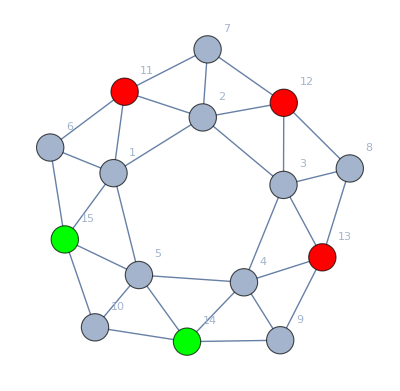

```mathematica
a
```

```mathematica
aaa={{1, {1,1,1,1,2}, {0,2,12,0,22,10}}, {2, {1,1,1,1,3}, {0,2,12,0,22,10}}, {3, {1,1,1,1,4}, {0,2,12,0,22,10}}, {4, {1,1,1,2,1}, {2,2,10,12,10,10}}, {5, {1,1,1,2,2}, {0,0,12,2,10,4}}, {6, {1,1,1,2,3}, {1,2,3,2,4,2}}, {7, {1,1,1,2,4}, {1,2,3,2,4,2}}, {8, {1,1,1,3,1}, {2,2,10,12,10,10}}, {9, {1,1,1,3,2}, {1,2,3,2,4,2}}, {10, {1,1,1,3,3}, {0,0,12,2,10,4}}, {11, {1,1,1,3,4}, {1,2,3,2,4,2}}, {12, {1,1,1,4,1}, {2,2,10,12,10,10}}, {13, {1,1,1,4,2}, {1,2,3,2,4,2}}, {14, {1,1,1,4,3}, {1,2,3,2,4,2}}, {15, {1,1,1,4,4}, {0,0,12,2,10,4}}, {16, {1,1,2,1,1}, {2,0,12,0,10,22}}, {17, {1,1,2,1,2}, {22,22,8,16,4,4}}, {18, {1,1,2,1,3}, {19,19,6,17,3,3}}, {19, {1,1,2,1,4}, {19,19,6,17,3,3}}, {20, {1,1,2,2,1}, {0,0,12,2,4,10}}, {21, {1,1,2,2,2}, {6,6,0,8,4,4}}, {22, {1,1,2,2,3}, {2,7,9,3,7,4}}, {23, {1,1,2,2,4}, {2,7,9,3,7,4}}, {24, {1,1,2,3,1}, {2,1,3,2,2,4}}, {25, {1,1,2,3,2}, {4,4,6,2,3,3}}, {26, {1,1,2,3,3}, {7,2,9,3,4,7}}, {27, {1,1,2,3,4}, {2,2,2,1,3,3}}, {28, {1,1,2,4,1}, {2,1,3,2,2,4}}, {29, {1,1,2,4,2}, {4,4,6,2,3,3}}, {30, {1,1,2,4,3}, {2,2,2,1,3,3}}, {31, {1,1,2,4,4}, {7,2,9,3,4,7}}, {32, {1,1,3,1,1}, {2,0,12,0,10,22}}, {33, {1,1,3,1,2}, {19,19,6,17,3,3}}, {34, {1,1,3,1,3}, {22,22,8,16,4,4}}, {35, {1,1,3,1,4}, {19,19,6,17,3,3}}, {36, {1,1,3,2,1}, {2,1,3,2,2,4}}, {37, {1,1,3,2,2}, {7,2,9,3,4,7}}, {38, {1,1,3,2,3}, {4,4,6,2,3,3}}, {39, {1,1,3,2,4}, {2,2,2,1,3,3}}, {40, {1,1,3,3,1}, {0,0,12,2,4,10}}, {41, {1,1,3,3,2}, {2,7,9,3,7,4}}, {42, {1,1,3,3,3}, {6,6,0,8,4,4}}, {43, {1,1,3,3,4}, {2,7,9,3,7,4}}, {44, {1,1,3,4,1}, {2,1,3,2,2,4}}, {45, {1,1,3,4,2}, {2,2,2,1,3,3}}, {46, {1,1,3,4,3}, {4,4,6,2,3,3}}, {47, {1,1,3,4,4}, {7,2,9,3,4,7}}, {48, {1,1,4,1,1}, {2,0,12,0,10,22}}, {49, {1,1,4,1,2}, {19,19,6,17,3,3}}, {50, {1,1,4,1,3}, {19,19,6,17,3,3}}, {51, {1,1,4,1,4}, {22,22,8,16,4,4}}, {52, {1,1,4,2,1}, {2,1,3,2,2,4}}, {53, {1,1,4,2,2}, {7,2,9,3,4,7}}, {54, {1,1,4,2,3}, {2,2,2,1,3,3}}, {55, {1,1,4,2,4}, {4,4,6,2,3,3}}, {56, {1,1,4,3,1}, {2,1,3,2,2,4}}, {57, {1,1,4,3,2}, {2,2,2,1,3,3}}, {58, {1,1,4,3,3}, {7,2,9,3,4,7}}, {59, {1,1,4,3,4}, {4,4,6,2,3,3}}, {60, {1,1,4,4,1}, {0,0,12,2,4,10}}, {61, {1,1,4,4,2}, {2,7,9,3,7,4}}, {62, {1,1,4,4,3}, {2,7,9,3,7,4}}, {63, {1,1,4,4,4}, {6,6,0,8,4,4}}, {64, {1,2,1,1,1}, {0,10,4,10,22,0}}, {65, {1,2,1,1,2}, {0,4,48,0,8,16}}, {66, {1,2,1,1,3}, {0,3,41,0,6,17}}, {67, {1,2,1,1,4}, {0,3,41,0,6,17}}, {68, {1,2,1,2,1}, {22,4,26,4,4,16}}, {69, {1,2,1,2,2}, {4,0,48,0,16,8}}, {70, {1,2,1,2,3}, {4,4,10,2,3,3}}, {71, {1,2,1,2,4}, {4,4,10,2,3,3}}, {72, {1,2,1,3,1}, {19,3,22,3,3,17}}, {73, {1,2,1,3,2}, {4,4,10,2,3,3}}, {74, {1,2,1,3,3}, {3,0,11,0,2,6}}, {75, {1,2,1,3,4}, {2,2,4,1,1,4}}, {76, {1,2,1,4,1}, {19,3,22,3,3,17}}, {77, {1,2,1,4,2}, {4,4,10,2,3,3}}, {78, {1,2,1,4,3}, {2,2,4,1,1,4}}, {79, {1,2,1,4,4}, {3,0,11,0,2,6}}, {80, {1,2,2,1,1}, {0,6,6,2,10,4}}, {81, {1,2,2,1,2}, {4,22,26,4,16,4}}, {82, {1,2,2,1,3}, {3,4,7,3,2,3}}, {83, {1,2,2,1,4}, {3,4,7,3,2,3}}, {84, {1,2,2,2,1}, {6,0,6,2,4,10}}, {85, {1,2,2,2,2}, {10,0,4,10,0,22}}, {86, {1,2,2,2,3}, {1,1,4,1,3,4}}, {87, {1,2,2,2,4}, {1,1,4,1,3,4}}, {88, {1,2,2,3,1}, {7,7,4,6,4,4}}, {89, {1,2,2,3,2}, {3,19,22,3,17,3}}, {90, {1,2,2,3,3}, {0,2,16,1,6,7}}, {91, {1,2,2,3,4}, {1,2,3,2,2,3}}, {92, {1,2,2,4,1}, {7,7,4,6,4,4}}, {93, {1,2,2,4,2}, {3,19,22,3,17,3}}, {94, {1,2,2,4,3}, {1,2,3,2,2,3}}, {95, {1,2,2,4,4}, {0,2,16,1,6,7}}, {96, {1,2,3,1,1}, {1,1,4,1,4,3}}, {97, {1,2,3,1,2}, {4,4,10,2,3,3}}, {98, {1,2,3,1,3}, {4,2,12,1,3,4}}, {99, {1,2,3,1,4}, {2,1,5,2,1,3}}, {100, {1,2,3,2,1}, {4,3,7,3,3,2}}, {101, {1,2,3,2,2}, {3,0,41,0,17,6}}, {102, {1,2,3,2,3}, {2,4,12,1,4,3}}, {103, {1,2,3,2,4}, {1,2,5,2,3,1}}, {104, {1,2,3,3,1}, {2,0,16,1,7,6}}, {105, {1,2,3,3,2}, {0,3,11,0,6,2}}, {106, {1,2,3,3,3}, {1,1,4,2,3,3}}, {107, {1,2,3,3,4}, {0,1,5,1,4,2}}, {108, {1,2,3,4,1}, {2,1,3,2,3,2}}, {109, {1,2,3,4,2}, {2,2,4,1,4,1}}, {110, {1,2,3,4,3}, {1,1,6,0,3,3}}, {111, {1,2,3,4,4}, {1,0,5,1,2,4}}, {112, {1,2,4,1,1}, {1,1,4,1,4,3}}, {113, {1,2,4,1,2}, {4,4,10,2,3,3}}, {114, {1,2,4,1,3}, {2,1,5,2,1,3}}, {115, {1,2,4,1,4}, {4,2,12,1,3,4}}, {116, {1,2,4,2,1}, {4,3,7,3,3,2}}, {117, {1,2,4,2,2}, {3,0,41,0,17,6}}, {118, {1,2,4,2,3}, {1,2,5,2,3,1}}, {119, {1,2,4,2,4}, {2,4,12,1,4,3}}, {120, {1,2,4,3,1}, {2,1,3,2,3,2}}, {121, {1,2,4,3,2}, {2,2,4,1,4,1}}, {122, {1,2,4,3,3}, {1,0,5,1,2,4}}, {123, {1,2,4,3,4}, {1,1,6,0,3,3}}, {124, {1,2,4,4,1}, {2,0,16,1,7,6}}, {125, {1,2,4,4,2}, {0,3,11,0,6,2}}, {126, {1,2,4,4,3}, {0,1,5,1,4,2}}, {127, {1,2,4,4,4}, {1,1,4,2,3,3}}, {128, {1,3,1,1,1}, {0,10,4,10,22,0}}, {129, {1,3,1,1,2}, {0,3,41,0,6,17}}, {130, {1,3,1,1,3}, {0,4,48,0,8,16}}, {131, {1,3,1,1,4}, {0,3,41,0,6,17}}, {132, {1,3,1,2,1}, {19,3,22,3,3,17}}, {133, {1,3,1,2,2}, {3,0,11,0,2,6}}, {134, {1,3,1,2,3}, {4,4,10,2,3,3}}, {135, {1,3,1,2,4}, {2,2,4,1,1,4}}, {136, {1,3,1,3,1}, {22,4,26,4,4,16}}, {137, {1,3,1,3,2}, {4,4,10,2,3,3}}, {138, {1,3,1,3,3}, {4,0,48,0,16,8}}, {139, {1,3,1,3,4}, {4,4,10,2,3,3}}, {140, {1,3,1,4,1}, {19,3,22,3,3,17}}, {141, {1,3,1,4,2}, {2,2,4,1,1,4}}, {142, {1,3,1,4,3}, {4,4,10,2,3,3}}, {143, {1,3,1,4,4}, {3,0,11,0,2,6}}, {144, {1,3,2,1,1}, {1,1,4,1,4,3}}, {145, {1,3,2,1,2}, {4,2,12,1,3,4}}, {146, {1,3,2,1,3}, {4,4,10,2,3,3}}, {147, {1,3,2,1,4}, {2,1,5,2,1,3}}, {148, {1,3,2,2,1}, {2,0,16,1,7,6}}, {149, {1,3,2,2,2}, {1,1,4,2,3,3}}, {150, {1,3,2,2,3}, {0,3,11,0,6,2}}, {151, {1,3,2,2,4}, {0,1,5,1,4,2}}, {152, {1,3,2,3,1}, {4,3,7,3,3,2}}, {153, {1,3,2,3,2}, {2,4,12,1,4,3}}, {154, {1,3,2,3,3}, {3,0,41,0,17,6}}, {155, {1,3,2,3,4}, {1,2,5,2,3,1}}, {156, {1,3,2,4,1}, {2,1,3,2,3,2}}, {157, {1,3,2,4,2}, {1,1,6,0,3,3}}, {158, {1,3,2,4,3}, {2,2,4,1,4,1}}, {159, {1,3,2,4,4}, {1,0,5,1,2,4}}, {160, {1,3,3,1,1}, {0,6,6,2,10,4}}, {161, {1,3,3,1,2}, {3,4,7,3,2,3}}, {162, {1,3,3,1,3}, {4,22,26,4,16,4}}, {163, {1,3,3,1,4}, {3,4,7,3,2,3}}, {164, {1,3,3,2,1}, {7,7,4,6,4,4}}, {165, {1,3,3,2,2}, {0,2,16,1,6,7}}, {166, {1,3,3,2,3}, {3,19,22,3,17,3}}, {167, {1,3,3,2,4}, {1,2,3,2,2,3}}, {168, {1,3,3,3,1}, {6,0,6,2,4,10}}, {169, {1,3,3,3,2}, {1,1,4,1,3,4}}, {170, {1,3,3,3,3}, {10,0,4,10,0,22}}, {171, {1,3,3,3,4}, {1,1,4,1,3,4}}, {172, {1,3,3,4,1}, {7,7,4,6,4,4}}, {173, {1,3,3,4,2}, {1,2,3,2,2,3}}, {174, {1,3,3,4,3}, {3,19,22,3,17,3}}, {175, {1,3,3,4,4}, {0,2,16,1,6,7}}, {176, {1,3,4,1,1}, {1,1,4,1,4,3}}, {177, {1,3,4,1,2}, {2,1,5,2,1,3}}, {178, {1,3,4,1,3}, {4,4,10,2,3,3}}, {179, {1,3,4,1,4}, {4,2,12,1,3,4}}, {180, {1,3,4,2,1}, {2,1,3,2,3,2}}, {181, {1,3,4,2,2}, {1,0,5,1,2,4}}, {182, {1,3,4,2,3}, {2,2,4,1,4,1}}, {183, {1,3,4,2,4}, {1,1,6,0,3,3}}, {184, {1,3,4,3,1}, {4,3,7,3,3,2}}, {185, {1,3,4,3,2}, {1,2,5,2,3,1}}, {186, {1,3,4,3,3}, {3,0,41,0,17,6}}, {187, {1,3,4,3,4}, {2,4,12,1,4,3}}, {188, {1,3,4,4,1}, {2,0,16,1,7,6}}, {189, {1,3,4,4,2}, {0,1,5,1,4,2}}, {190, {1,3,4,4,3}, {0,3,11,0,6,2}}, {191, {1,3,4,4,4}, {1,1,4,2,3,3}}, {192, {1,4,1,1,1}, {0,10,4,10,22,0}}, {193, {1,4,1,1,2}, {0,3,41,0,6,17}}, {194, {1,4,1,1,3}, {0,3,41,0,6,17}}, {195, {1,4,1,1,4}, {0,4,48,0,8,16}}, {196, {1,4,1,2,1}, {19,3,22,3,3,17}}, {197, {1,4,1,2,2}, {3,0,11,0,2,6}}, {198, {1,4,1,2,3}, {2,2,4,1,1,4}}, {199, {1,4,1,2,4}, {4,4,10,2,3,3}}, {200, {1,4,1,3,1}, {19,3,22,3,3,17}}, {201, {1,4,1,3,2}, {2,2,4,1,1,4}}, {202, {1,4,1,3,3}, {3,0,11,0,2,6}}, {203, {1,4,1,3,4}, {4,4,10,2,3,3}}, {204, {1,4,1,4,1}, {22,4,26,4,4,16}}, {205, {1,4,1,4,2}, {4,4,10,2,3,3}}, {206, {1,4,1,4,3}, {4,4,10,2,3,3}}, {207, {1,4,1,4,4}, {4,0,48,0,16,8}}, {208, {1,4,2,1,1}, {1,1,4,1,4,3}}, {209, {1,4,2,1,2}, {4,2,12,1,3,4}}, {210, {1,4,2,1,3}, {2,1,5,2,1,3}}, {211, {1,4,2,1,4}, {4,4,10,2,3,3}}, {212, {1,4,2,2,1}, {2,0,16,1,7,6}}, {213, {1,4,2,2,2}, {1,1,4,2,3,3}}, {214, {1,4,2,2,3}, {0,1,5,1,4,2}}, {215, {1,4,2,2,4}, {0,3,11,0,6,2}}, {216, {1,4,2,3,1}, {2,1,3,2,3,2}}, {217, {1,4,2,3,2}, {1,1,6,0,3,3}}, {218, {1,4,2,3,3}, {1,0,5,1,2,4}}, {219, {1,4,2,3,4}, {2,2,4,1,4,1}}, {220, {1,4,2,4,1}, {4,3,7,3,3,2}}, {221, {1,4,2,4,2}, {2,4,12,1,4,3}}, {222, {1,4,2,4,3}, {1,2,5,2,3,1}}, {223, {1,4,2,4,4}, {3,0,41,0,17,6}}, {224, {1,4,3,1,1}, {1,1,4,1,4,3}}, {225, {1,4,3,1,2}, {2,1,5,2,1,3}}, {226, {1,4,3,1,3}, {4,2,12,1,3,4}}, {227, {1,4,3,1,4}, {4,4,10,2,3,3}}, {228, {1,4,3,2,1}, {2,1,3,2,3,2}}, {229, {1,4,3,2,2}, {1,0,5,1,2,4}}, {230, {1,4,3,2,3}, {1,1,6,0,3,3}}, {231, {1,4,3,2,4}, {2,2,4,1,4,1}}, {232, {1,4,3,3,1}, {2,0,16,1,7,6}}, {233, {1,4,3,3,2}, {0,1,5,1,4,2}}, {234, {1,4,3,3,3}, {1,1,4,2,3,3}}, {235, {1,4,3,3,4}, {0,3,11,0,6,2}}, {236, {1,4,3,4,1}, {4,3,7,3,3,2}}, {237, {1,4,3,4,2}, {1,2,5,2,3,1}}, {238, {1,4,3,4,3}, {2,4,12,1,4,3}}, {239, {1,4,3,4,4}, {3,0,41,0,17,6}}, {240, {1,4,4,1,1}, {0,6,6,2,10,4}}, {241, {1,4,4,1,2}, {3,4,7,3,2,3}}, {242, {1,4,4,1,3}, {3,4,7,3,2,3}}, {243, {1,4,4,1,4}, {4,22,26,4,16,4}}, {244, {1,4,4,2,1}, {7,7,4,6,4,4}}, {245, {1,4,4,2,2}, {0,2,16,1,6,7}}, {246, {1,4,4,2,3}, {1,2,3,2,2,3}}, {247, {1,4,4,2,4}, {3,19,22,3,17,3}}, {248, {1,4,4,3,1}, {7,7,4,6,4,4}}, {249, {1,4,4,3,2}, {1,2,3,2,2,3}}, {250, {1,4,4,3,3}, {0,2,16,1,6,7}}, {251, {1,4,4,3,4}, {3,19,22,3,17,3}}, {252, {1,4,4,4,1}, {6,0,6,2,4,10}}, {253, {1,4,4,4,2}, {1,1,4,1,3,4}}, {254, {1,4,4,4,3}, {1,1,4,1,3,4}}, {255, {1,4,4,4,4}, {10,0,4,10,0,22}}, {256, {2,1,1,1,1}, {10,0,4,10,0,22}}, {257, {2,1,1,1,2}, {6,0,6,2,4,10}}, {258, {2,1,1,1,3}, {1,1,4,1,3,4}}, {259, {2,1,1,1,4}, {1,1,4,1,3,4}}, {260, {2,1,1,2,1}, {4,22,26,4,16,4}}, {261, {2,1,1,2,2}, {0,6,6,2,10,4}}, {262, {2,1,1,2,3}, {3,4,7,3,2,3}}, {263, {2,1,1,2,4}, {3,4,7,3,2,3}}, {264, {2,1,1,3,1}, {3,19,22,3,17,3}}, {265, {2,1,1,3,2}, {7,7,4,6,4,4}}, {266, {2,1,1,3,3}, {0,2,16,1,6,7}}, {267, {2,1,1,3,4}, {1,2,3,2,2,3}}, {268, {2,1,1,4,1}, {3,19,22,3,17,3}}, {269, {2,1,1,4,2}, {7,7,4,6,4,4}}, {270, {2,1,1,4,3}, {1,2,3,2,2,3}}, {271, {2,1,1,4,4}, {0,2,16,1,6,7}}, {272, {2,1,2,1,1}, {4,0,48,0,16,8}}, {273, {2,1,2,1,2}, {22,4,26,4,4,16}}, {274, {2,1,2,1,3}, {4,4,10,2,3,3}}, {275, {2,1,2,1,4}, {4,4,10,2,3,3}}, {276, {2,1,2,2,1}, {0,4,48,0,8,16}}, {277, {2,1,2,2,2}, {0,10,4,10,22,0}}, {278, {2,1,2,2,3}, {0,3,41,0,6,17}}, {279, {2,1,2,2,4}, {0,3,41,0,6,17}}, {280, {2,1,2,3,1}, {4,4,10,2,3,3}}, {281, {2,1,2,3,2}, {19,3,22,3,3,17}}, {282, {2,1,2,3,3}, {3,0,11,0,2,6}}, {283, {2,1,2,3,4}, {2,2,4,1,1,4}}, {284, {2,1,2,4,1}, {4,4,10,2,3,3}}, {285, {2,1,2,4,2}, {19,3,22,3,3,17}}, {286, {2,1,2,4,3}, {2,2,4,1,1,4}}, {287, {2,1,2,4,4}, {3,0,11,0,2,6}}, {288, {2,1,3,1,1}, {3,0,41,0,17,6}}, {289, {2,1,3,1,2}, {4,3,7,3,3,2}}, {290, {2,1,3,1,3}, {2,4,12,1,4,3}}, {291, {2,1,3,1,4}, {1,2,5,2,3,1}}, {292, {2,1,3,2,1}, {4,4,10,2,3,3}}, {293, {2,1,3,2,2}, {1,1,4,1,4,3}}, {294, {2,1,3,2,3}, {4,2,12,1,3,4}}, {295, {2,1,3,2,4}, {2,1,5,2,1,3}}, {296, {2,1,3,3,1}, {0,3,11,0,6,2}}, {297, {2,1,3,3,2}, {2,0,16,1,7,6}}, {298, {2,1,3,3,3}, {1,1,4,2,3,3}}, {299, {2,1,3,3,4}, {0,1,5,1,4,2}}, {300, {2,1,3,4,1}, {2,2,4,1,4,1}}, {301, {2,1,3,4,2}, {2,1,3,2,3,2}}, {302, {2,1,3,4,3}, {1,1,6,0,3,3}}, {303, {2,1,3,4,4}, {1,0,5,1,2,4}}, {304, {2,1,4,1,1}, {3,0,41,0,17,6}}, {305, {2,1,4,1,2}, {4,3,7,3,3,2}}, {306, {2,1,4,1,3}, {1,2,5,2,3,1}}, {307, {2,1,4,1,4}, {2,4,12,1,4,3}}, {308, {2,1,4,2,1}, {4,4,10,2,3,3}}, {309, {2,1,4,2,2}, {1,1,4,1,4,3}}, {310, {2,1,4,2,3}, {2,1,5,2,1,3}}, {311, {2,1,4,2,4}, {4,2,12,1,3,4}}, {312, {2,1,4,3,1}, {2,2,4,1,4,1}}, {313, {2,1,4,3,2}, {2,1,3,2,3,2}}, {314, {2,1,4,3,3}, {1,0,5,1,2,4}}, {315, {2,1,4,3,4}, {1,1,6,0,3,3}}, {316, {2,1,4,4,1}, {0,3,11,0,6,2}}, {317, {2,1,4,4,2}, {2,0,16,1,7,6}}, {318, {2,1,4,4,3}, {0,1,5,1,4,2}}, {319, {2,1,4,4,4}, {1,1,4,2,3,3}}, {320, {2,2,1,1,1}, {6,6,0,8,4,4}}, {321, {2,2,1,1,2}, {0,0,12,2,4,10}}, {322, {2,2,1,1,3}, {2,7,9,3,7,4}}, {323, {2,2,1,1,4}, {2,7,9,3,7,4}}, {324, {2,2,1,2,1}, {22,22,8,16,4,4}}, {325, {2,2,1,2,2}, {2,0,12,0,10,22}}, {326, {2,2,1,2,3}, {19,19,6,17,3,3}}, {327, {2,2,1,2,4}, {19,19,6,17,3,3}}, {328, {2,2,1,3,1}, {4,4,6,2,3,3}}, {329, {2,2,1,3,2}, {2,1,3,2,2,4}}, {330, {2,2,1,3,3}, {7,2,9,3,4,7}}, {331, {2,2,1,3,4}, {2,2,2,1,3,3}}, {332, {2,2,1,4,1}, {4,4,6,2,3,3}}, {333, {2,2,1,4,2}, {2,1,3,2,2,4}}, {334, {2,2,1,4,3}, {2,2,2,1,3,3}}, {335, {2,2,1,4,4}, {7,2,9,3,4,7}}, {336, {2,2,2,1,1}, {0,0,12,2,10,4}}, {337, {2,2,2,1,2}, {2,2,10,12,10,10}}, {338, {2,2,2,1,3}, {1,2,3,2,4,2}}, {339, {2,2,2,1,4}, {1,2,3,2,4,2}}, {340, {2,2,2,2,1}, {0,2,12,0,22,10}}, {341, {2,2,2,2,2}, {6,6,18,0,0,0}}, {342, {2,2,2,2,3}, {0,2,12,0,22,10}}, {343, {2,2,2,2,4}, {0,2,12,0,22,10}}, {344, {2,2,2,3,1}, {1,2,3,2,4,2}}, {345, {2,2,2,3,2}, {2,2,10,12,10,10}}, {346, {2,2,2,3,3}, {0,0,12,2,10,4}}, {347, {2,2,2,3,4}, {1,2,3,2,4,2}}, {348, {2,2,2,4,1}, {1,2,3,2,4,2}}, {349, {2,2,2,4,2}, {2,2,10,12,10,10}}, {350, {2,2,2,4,3}, {1,2,3,2,4,2}}, {351, {2,2,2,4,4}, {0,0,12,2,10,4}}, {352, {2,2,3,1,1}, {7,2,9,3,4,7}}, {353, {2,2,3,1,2}, {2,1,3,2,2,4}}, {354, {2,2,3,1,3}, {4,4,6,2,3,3}}, {355, {2,2,3,1,4}, {2,2,2,1,3,3}}, {356, {2,2,3,2,1}, {19,19,6,17,3,3}}, {357, {2,2,3,2,2}, {2,0,12,0,10,22}}, {358, {2,2,3,2,3}, {22,22,8,16,4,4}}, {359, {2,2,3,2,4}, {19,19,6,17,3,3}}, {360, {2,2,3,3,1}, {2,7,9,3,7,4}}, {361, {2,2,3,3,2}, {0,0,12,2,4,10}}, {362, {2,2,3,3,3}, {6,6,0,8,4,4}}, {363, {2,2,3,3,4}, {2,7,9,3,7,4}}, {364, {2,2,3,4,1}, {2,2,2,1,3,3}}, {365, {2,2,3,4,2}, {2,1,3,2,2,4}}, {366, {2,2,3,4,3}, {4,4,6,2,3,3}}, {367, {2,2,3,4,4}, {7,2,9,3,4,7}}, {368, {2,2,4,1,1}, {7,2,9,3,4,7}}, {369, {2,2,4,1,2}, {2,1,3,2,2,4}}, {370, {2,2,4,1,3}, {2,2,2,1,3,3}}, {371, {2,2,4,1,4}, {4,4,6,2,3,3}}, {372, {2,2,4,2,1}, {19,19,6,17,3,3}}, {373, {2,2,4,2,2}, {2,0,12,0,10,22}}, {374, {2,2,4,2,3}, {19,19,6,17,3,3}}, {375, {2,2,4,2,4}, {22,22,8,16,4,4}}, {376, {2,2,4,3,1}, {2,2,2,1,3,3}}, {377, {2,2,4,3,2}, {2,1,3,2,2,4}}, {378, {2,2,4,3,3}, {7,2,9,3,4,7}}, {379, {2,2,4,3,4}, {4,4,6,2,3,3}}, {380, {2,2,4,4,1}, {2,7,9,3,7,4}}, {381, {2,2,4,4,2}, {0,0,12,2,4,10}}, {382, {2,2,4,4,3}, {2,7,9,3,7,4}}, {383, {2,2,4,4,4}, {6,6,0,8,4,4}}, {384, {2,3,1,1,1}, {1,1,4,2,3,3}}, {385, {2,3,1,1,2}, {2,0,16,1,7,6}}, {386, {2,3,1,1,3}, {0,3,11,0,6,2}}, {387, {2,3,1,1,4}, {0,1,5,1,4,2}}, {388, {2,3,1,2,1}, {4,2,12,1,3,4}}, {389, {2,3,1,2,2}, {1,1,4,1,4,3}}, {390, {2,3,1,2,3}, {4,4,10,2,3,3}}, {391, {2,3,1,2,4}, {2,1,5,2,1,3}}, {392, {2,3,1,3,1}, {2,4,12,1,4,3}}, {393, {2,3,1,3,2}, {4,3,7,3,3,2}}, {394, {2,3,1,3,3}, {3,0,41,0,17,6}}, {395, {2,3,1,3,4}, {1,2,5,2,3,1}}, {396, {2,3,1,4,1}, {1,1,6,0,3,3}}, {397, {2,3,1,4,2}, {2,1,3,2,3,2}}, {398, {2,3,1,4,3}, {2,2,4,1,4,1}}, {399, {2,3,1,4,4}, {1,0,5,1,2,4}}, {400, {2,3,2,1,1}, {3,0,11,0,2,6}}, {401, {2,3,2,1,2}, {19,3,22,3,3,17}}, {402, {2,3,2,1,3}, {4,4,10,2,3,3}}, {403, {2,3,2,1,4}, {2,2,4,1,1,4}}, {404, {2,3,2,2,1}, {0,3,41,0,6,17}}, {405, {2,3,2,2,2}, {0,10,4,10,22,0}}, {406, {2,3,2,2,3}, {0,4,48,0,8,16}}, {407, {2,3,2,2,4}, {0,3,41,0,6,17}}, {408, {2,3,2,3,1}, {4,4,10,2,3,3}}, {409, {2,3,2,3,2}, {22,4,26,4,4,16}}, {410, {2,3,2,3,3}, {4,0,48,0,16,8}}, {411, {2,3,2,3,4}, {4,4,10,2,3,3}}, {412, {2,3,2,4,1}, {2,2,4,1,1,4}}, {413, {2,3,2,4,2}, {19,3,22,3,3,17}}, {414, {2,3,2,4,3}, {4,4,10,2,3,3}}, {415, {2,3,2,4,4}, {3,0,11,0,2,6}}, {416, {2,3,3,1,1}, {0,2,16,1,6,7}}, {417, {2,3,3,1,2}, {7,7,4,6,4,4}}, {418, {2,3,3,1,3}, {3,19,22,3,17,3}}, {419, {2,3,3,1,4}, {1,2,3,2,2,3}}, {420, {2,3,3,2,1}, {3,4,7,3,2,3}}, {421, {2,3,3,2,2}, {0,6,6,2,10,4}}, {422, {2,3,3,2,3}, {4,22,26,4,16,4}}, {423, {2,3,3,2,4}, {3,4,7,3,2,3}}, {424, {2,3,3,3,1}, {1,1,4,1,3,4}}, {425, {2,3,3,3,2}, {6,0,6,2,4,10}}, {426, {2,3,3,3,3}, {10,0,4,10,0,22}}, {427, {2,3,3,3,4}, {1,1,4,1,3,4}}, {428, {2,3,3,4,1}, {1,2,3,2,2,3}}, {429, {2,3,3,4,2}, {7,7,4,6,4,4}}, {430, {2,3,3,4,3}, {3,19,22,3,17,3}}, {431, {2,3,3,4,4}, {0,2,16,1,6,7}}, {432, {2,3,4,1,1}, {1,0,5,1,2,4}}, {433, {2,3,4,1,2}, {2,1,3,2,3,2}}, {434, {2,3,4,1,3}, {2,2,4,1,4,1}}, {435, {2,3,4,1,4}, {1,1,6,0,3,3}}, {436, {2,3,4,2,1}, {2,1,5,2,1,3}}, {437, {2,3,4,2,2}, {1,1,4,1,4,3}}, {438, {2,3,4,2,3}, {4,4,10,2,3,3}}, {439, {2,3,4,2,4}, {4,2,12,1,3,4}}, {440, {2,3,4,3,1}, {1,2,5,2,3,1}}, {441, {2,3,4,3,2}, {4,3,7,3,3,2}}, {442, {2,3,4,3,3}, {3,0,41,0,17,6}}, {443, {2,3,4,3,4}, {2,4,12,1,4,3}}, {444, {2,3,4,4,1}, {0,1,5,1,4,2}}, {445, {2,3,4,4,2}, {2,0,16,1,7,6}}, {446, {2,3,4,4,3}, {0,3,11,0,6,2}}, {447, {2,3,4,4,4}, {1,1,4,2,3,3}}, {448, {2,4,1,1,1}, {1,1,4,2,3,3}}, {449, {2,4,1,1,2}, {2,0,16,1,7,6}}, {450, {2,4,1,1,3}, {0,1,5,1,4,2}}, {451, {2,4,1,1,4}, {0,3,11,0,6,2}}, {452, {2,4,1,2,1}, {4,2,12,1,3,4}}, {453, {2,4,1,2,2}, {1,1,4,1,4,3}}, {454, {2,4,1,2,3}, {2,1,5,2,1,3}}, {455, {2,4,1,2,4}, {4,4,10,2,3,3}}, {456, {2,4,1,3,1}, {1,1,6,0,3,3}}, {457, {2,4,1,3,2}, {2,1,3,2,3,2}}, {458, {2,4,1,3,3}, {1,0,5,1,2,4}}, {459, {2,4,1,3,4}, {2,2,4,1,4,1}}, {460, {2,4,1,4,1}, {2,4,12,1,4,3}}, {461, {2,4,1,4,2}, {4,3,7,3,3,2}}, {462, {2,4,1,4,3}, {1,2,5,2,3,1}}, {463, {2,4,1,4,4}, {3,0,41,0,17,6}}, {464, {2,4,2,1,1}, {3,0,11,0,2,6}}, {465, {2,4,2,1,2}, {19,3,22,3,3,17}}, {466, {2,4,2,1,3}, {2,2,4,1,1,4}}, {467, {2,4,2,1,4}, {4,4,10,2,3,3}}, {468, {2,4,2,2,1}, {0,3,41,0,6,17}}, {469, {2,4,2,2,2}, {0,10,4,10,22,0}}, {470, {2,4,2,2,3}, {0,3,41,0,6,17}}, {471, {2,4,2,2,4}, {0,4,48,0,8,16}}, {472, {2,4,2,3,1}, {2,2,4,1,1,4}}, {473, {2,4,2,3,2}, {19,3,22,3,3,17}}, {474, {2,4,2,3,3}, {3,0,11,0,2,6}}, {475, {2,4,2,3,4}, {4,4,10,2,3,3}}, {476, {2,4,2,4,1}, {4,4,10,2,3,3}}, {477, {2,4,2,4,2}, {22,4,26,4,4,16}}, {478, {2,4,2,4,3}, {4,4,10,2,3,3}}, {479, {2,4,2,4,4}, {4,0,48,0,16,8}}, {480, {2,4,3,1,1}, {1,0,5,1,2,4}}, {481, {2,4,3,1,2}, {2,1,3,2,3,2}}, {482, {2,4,3,1,3}, {1,1,6,0,3,3}}, {483, {2,4,3,1,4}, {2,2,4,1,4,1}}, {484, {2,4,3,2,1}, {2,1,5,2,1,3}}, {485, {2,4,3,2,2}, {1,1,4,1,4,3}}, {486, {2,4,3,2,3}, {4,2,12,1,3,4}}, {487, {2,4,3,2,4}, {4,4,10,2,3,3}}, {488, {2,4,3,3,1}, {0,1,5,1,4,2}}, {489, {2,4,3,3,2}, {2,0,16,1,7,6}}, {490, {2,4,3,3,3}, {1,1,4,2,3,3}}, {491, {2,4,3,3,4}, {0,3,11,0,6,2}}, {492, {2,4,3,4,1}, {1,2,5,2,3,1}}, {493, {2,4,3,4,2}, {4,3,7,3,3,2}}, {494, {2,4,3,4,3}, {2,4,12,1,4,3}}, {495, {2,4,3,4,4}, {3,0,41,0,17,6}}, {496, {2,4,4,1,1}, {0,2,16,1,6,7}}, {497, {2,4,4,1,2}, {7,7,4,6,4,4}}, {498, {2,4,4,1,3}, {1,2,3,2,2,3}}, {499, {2,4,4,1,4}, {3,19,22,3,17,3}}, {500, {2,4,4,2,1}, {3,4,7,3,2,3}}, {501, {2,4,4,2,2}, {0,6,6,2,10,4}}, {502, {2,4,4,2,3}, {3,4,7,3,2,3}}, {503, {2,4,4,2,4}, {4,22,26,4,16,4}}, {504, {2,4,4,3,1}, {1,2,3,2,2,3}}, {505, {2,4,4,3,2}, {7,7,4,6,4,4}}, {506, {2,4,4,3,3}, {0,2,16,1,6,7}}, {507, {2,4,4,3,4}, {3,19,22,3,17,3}}, {508, {2,4,4,4,1}, {1,1,4,1,3,4}}, {509, {2,4,4,4,2}, {6,0,6,2,4,10}}, {510, {2,4,4,4,3}, {1,1,4,1,3,4}}, {511, {2,4,4,4,4}, {10,0,4,10,0,22}}, {512, {3,1,1,1,1}, {10,0,4,10,0,22}}, {513, {3,1,1,1,2}, {1,1,4,1,3,4}}, {514, {3,1,1,1,3}, {6,0,6,2,4,10}}, {515, {3,1,1,1,4}, {1,1,4,1,3,4}}, {516, {3,1,1,2,1}, {3,19,22,3,17,3}}, {517, {3,1,1,2,2}, {0,2,16,1,6,7}}, {518, {3,1,1,2,3}, {7,7,4,6,4,4}}, {519, {3,1,1,2,4}, {1,2,3,2,2,3}}, {520, {3,1,1,3,1}, {4,22,26,4,16,4}}, {521, {3,1,1,3,2}, {3,4,7,3,2,3}}, {522, {3,1,1,3,3}, {0,6,6,2,10,4}}, {523, {3,1,1,3,4}, {3,4,7,3,2,3}}, {524, {3,1,1,4,1}, {3,19,22,3,17,3}}, {525, {3,1,1,4,2}, {1,2,3,2,2,3}}, {526, {3,1,1,4,3}, {7,7,4,6,4,4}}, {527, {3,1,1,4,4}, {0,2,16,1,6,7}}, {528, {3,1,2,1,1}, {3,0,41,0,17,6}}, {529, {3,1,2,1,2}, {2,4,12,1,4,3}}, {530, {3,1,2,1,3}, {4,3,7,3,3,2}}, {531, {3,1,2,1,4}, {1,2,5,2,3,1}}, {532, {3,1,2,2,1}, {0,3,11,0,6,2}}, {533, {3,1,2,2,2}, {1,1,4,2,3,3}}, {534, {3,1,2,2,3}, {2,0,16,1,7,6}}, {535, {3,1,2,2,4}, {0,1,5,1,4,2}}, {536, {3,1,2,3,1}, {4,4,10,2,3,3}}, {537, {3,1,2,3,2}, {4,2,12,1,3,4}}, {538, {3,1,2,3,3}, {1,1,4,1,4,3}}, {539, {3,1,2,3,4}, {2,1,5,2,1,3}}, {540, {3,1,2,4,1}, {2,2,4,1,4,1}}, {541, {3,1,2,4,2}, {1,1,6,0,3,3}}, {542, {3,1,2,4,3}, {2,1,3,2,3,2}}, {543, {3,1,2,4,4}, {1,0,5,1,2,4}}, {544, {3,1,3,1,1}, {4,0,48,0,16,8}}, {545, {3,1,3,1,2}, {4,4,10,2,3,3}}, {546, {3,1,3,1,3}, {22,4,26,4,4,16}}, {547, {3,1,3,1,4}, {4,4,10,2,3,3}}, {548, {3,1,3,2,1}, {4,4,10,2,3,3}}, {549, {3,1,3,2,2}, {3,0,11,0,2,6}}, {550, {3,1,3,2,3}, {19,3,22,3,3,17}}, {551, {3,1,3,2,4}, {2,2,4,1,1,4}}, {552, {3,1,3,3,1}, {0,4,48,0,8,16}}, {553, {3,1,3,3,2}, {0,3,41,0,6,17}}, {554, {3,1,3,3,3}, {0,10,4,10,22,0}}, {555, {3,1,3,3,4}, {0,3,41,0,6,17}}, {556, {3,1,3,4,1}, {4,4,10,2,3,3}}, {557, {3,1,3,4,2}, {2,2,4,1,1,4}}, {558, {3,1,3,4,3}, {19,3,22,3,3,17}}, {559, {3,1,3,4,4}, {3,0,11,0,2,6}}, {560, {3,1,4,1,1}, {3,0,41,0,17,6}}, {561, {3,1,4,1,2}, {1,2,5,2,3,1}}, {562, {3,1,4,1,3}, {4,3,7,3,3,2}}, {563, {3,1,4,1,4}, {2,4,12,1,4,3}}, {564, {3,1,4,2,1}, {2,2,4,1,4,1}}, {565, {3,1,4,2,2}, {1,0,5,1,2,4}}, {566, {3,1,4,2,3}, {2,1,3,2,3,2}}, {567, {3,1,4,2,4}, {1,1,6,0,3,3}}, {568, {3,1,4,3,1}, {4,4,10,2,3,3}}, {569, {3,1,4,3,2}, {2,1,5,2,1,3}}, {570, {3,1,4,3,3}, {1,1,4,1,4,3}}, {571, {3,1,4,3,4}, {4,2,12,1,3,4}}, {572, {3,1,4,4,1}, {0,3,11,0,6,2}}, {573, {3,1,4,4,2}, {0,1,5,1,4,2}}, {574, {3,1,4,4,3}, {2,0,16,1,7,6}}, {575, {3,1,4,4,4}, {1,1,4,2,3,3}}, {576, {3,2,1,1,1}, {1,1,4,2,3,3}}, {577, {3,2,1,1,2}, {0,3,11,0,6,2}}, {578, {3,2,1,1,3}, {2,0,16,1,7,6}}, {579, {3,2,1,1,4}, {0,1,5,1,4,2}}, {580, {3,2,1,2,1}, {2,4,12,1,4,3}}, {581, {3,2,1,2,2}, {3,0,41,0,17,6}}, {582, {3,2,1,2,3}, {4,3,7,3,3,2}}, {583, {3,2,1,2,4}, {1,2,5,2,3,1}}, {584, {3,2,1,3,1}, {4,2,12,1,3,4}}, {585, {3,2,1,3,2}, {4,4,10,2,3,3}}, {586, {3,2,1,3,3}, {1,1,4,1,4,3}}, {587, {3,2,1,3,4}, {2,1,5,2,1,3}}, {588, {3,2,1,4,1}, {1,1,6,0,3,3}}, {589, {3,2,1,4,2}, {2,2,4,1,4,1}}, {590, {3,2,1,4,3}, {2,1,3,2,3,2}}, {591, {3,2,1,4,4}, {1,0,5,1,2,4}}, {592, {3,2,2,1,1}, {0,2,16,1,6,7}}, {593, {3,2,2,1,2}, {3,19,22,3,17,3}}, {594, {3,2,2,1,3}, {7,7,4,6,4,4}}, {595, {3,2,2,1,4}, {1,2,3,2,2,3}}, {596, {3,2,2,2,1}, {1,1,4,1,3,4}}, {597, {3,2,2,2,2}, {10,0,4,10,0,22}}, {598, {3,2,2,2,3}, {6,0,6,2,4,10}}, {599, {3,2,2,2,4}, {1,1,4,1,3,4}}, {600, {3,2,2,3,1}, {3,4,7,3,2,3}}, {601, {3,2,2,3,2}, {4,22,26,4,16,4}}, {602, {3,2,2,3,3}, {0,6,6,2,10,4}}, {603, {3,2,2,3,4}, {3,4,7,3,2,3}}, {604, {3,2,2,4,1}, {1,2,3,2,2,3}}, {605, {3,2,2,4,2}, {3,19,22,3,17,3}}, {606, {3,2,2,4,3}, {7,7,4,6,4,4}}, {607, {3,2,2,4,4}, {0,2,16,1,6,7}}, {608, {3,2,3,1,1}, {3,0,11,0,2,6}}, {609, {3,2,3,1,2}, {4,4,10,2,3,3}}, {610, {3,2,3,1,3}, {19,3,22,3,3,17}}, {611, {3,2,3,1,4}, {2,2,4,1,1,4}}, {612, {3,2,3,2,1}, {4,4,10,2,3,3}}, {613, {3,2,3,2,2}, {4,0,48,0,16,8}}, {614, {3,2,3,2,3}, {22,4,26,4,4,16}}, {615, {3,2,3,2,4}, {4,4,10,2,3,3}}, {616, {3,2,3,3,1}, {0,3,41,0,6,17}}, {617, {3,2,3,3,2}, {0,4,48,0,8,16}}, {618, {3,2,3,3,3}, {0,10,4,10,22,0}}, {619, {3,2,3,3,4}, {0,3,41,0,6,17}}, {620, {3,2,3,4,1}, {2,2,4,1,1,4}}, {621, {3,2,3,4,2}, {4,4,10,2,3,3}}, {622, {3,2,3,4,3}, {19,3,22,3,3,17}}, {623, {3,2,3,4,4}, {3,0,11,0,2,6}}, {624, {3,2,4,1,1}, {1,0,5,1,2,4}}, {625, {3,2,4,1,2}, {2,2,4,1,4,1}}, {626, {3,2,4,1,3}, {2,1,3,2,3,2}}, {627, {3,2,4,1,4}, {1,1,6,0,3,3}}, {628, {3,2,4,2,1}, {1,2,5,2,3,1}}, {629, {3,2,4,2,2}, {3,0,41,0,17,6}}, {630, {3,2,4,2,3}, {4,3,7,3,3,2}}, {631, {3,2,4,2,4}, {2,4,12,1,4,3}}, {632, {3,2,4,3,1}, {2,1,5,2,1,3}}, {633, {3,2,4,3,2}, {4,4,10,2,3,3}}, {634, {3,2,4,3,3}, {1,1,4,1,4,3}}, {635, {3,2,4,3,4}, {4,2,12,1,3,4}}, {636, {3,2,4,4,1}, {0,1,5,1,4,2}}, {637, {3,2,4,4,2}, {0,3,11,0,6,2}}, {638, {3,2,4,4,3}, {2,0,16,1,7,6}}, {639, {3,2,4,4,4}, {1,1,4,2,3,3}}, {640, {3,3,1,1,1}, {6,6,0,8,4,4}}, {641, {3,3,1,1,2}, {2,7,9,3,7,4}}, {642, {3,3,1,1,3}, {0,0,12,2,4,10}}, {643, {3,3,1,1,4}, {2,7,9,3,7,4}}, {644, {3,3,1,2,1}, {4,4,6,2,3,3}}, {645, {3,3,1,2,2}, {7,2,9,3,4,7}}, {646, {3,3,1,2,3}, {2,1,3,2,2,4}}, {647, {3,3,1,2,4}, {2,2,2,1,3,3}}, {648, {3,3,1,3,1}, {22,22,8,16,4,4}}, {649, {3,3,1,3,2}, {19,19,6,17,3,3}}, {650, {3,3,1,3,3}, {2,0,12,0,10,22}}, {651, {3,3,1,3,4}, {19,19,6,17,3,3}}, {652, {3,3,1,4,1}, {4,4,6,2,3,3}}, {653, {3,3,1,4,2}, {2,2,2,1,3,3}}, {654, {3,3,1,4,3}, {2,1,3,2,2,4}}, {655, {3,3,1,4,4}, {7,2,9,3,4,7}}, {656, {3,3,2,1,1}, {7,2,9,3,4,7}}, {657, {3,3,2,1,2}, {4,4,6,2,3,3}}, {658, {3,3,2,1,3}, {2,1,3,2,2,4}}, {659, {3,3,2,1,4}, {2,2,2,1,3,3}}, {660, {3,3,2,2,1}, {2,7,9,3,7,4}}, {661, {3,3,2,2,2}, {6,6,0,8,4,4}}, {662, {3,3,2,2,3}, {0,0,12,2,4,10}}, {663, {3,3,2,2,4}, {2,7,9,3,7,4}}, {664, {3,3,2,3,1}, {19,19,6,17,3,3}}, {665, {3,3,2,3,2}, {22,22,8,16,4,4}}, {666, {3,3,2,3,3}, {2,0,12,0,10,22}}, {667, {3,3,2,3,4}, {19,19,6,17,3,3}}, {668, {3,3,2,4,1}, {2,2,2,1,3,3}}, {669, {3,3,2,4,2}, {4,4,6,2,3,3}}, {670, {3,3,2,4,3}, {2,1,3,2,2,4}}, {671, {3,3,2,4,4}, {7,2,9,3,4,7}}, {672, {3,3,3,1,1}, {0,0,12,2,10,4}}, {673, {3,3,3,1,2}, {1,2,3,2,4,2}}, {674, {3,3,3,1,3}, {2,2,10,12,10,10}}, {675, {3,3,3,1,4}, {1,2,3,2,4,2}}, {676, {3,3,3,2,1}, {1,2,3,2,4,2}}, {677, {3,3,3,2,2}, {0,0,12,2,10,4}}, {678, {3,3,3,2,3}, {2,2,10,12,10,10}}, {679, {3,3,3,2,4}, {1,2,3,2,4,2}}, {680, {3,3,3,3,1}, {0,2,12,0,22,10}}, {681, {3,3,3,3,2}, {0,2,12,0,22,10}}, {682, {3,3,3,3,3}, {6,6,18,0,0,0}}, {683, {3,3,3,3,4}, {0,2,12,0,22,10}}, {684, {3,3,3,4,1}, {1,2,3,2,4,2}}, {685, {3,3,3,4,2}, {1,2,3,2,4,2}}, {686, {3,3,3,4,3}, {2,2,10,12,10,10}}, {687, {3,3,3,4,4}, {0,0,12,2,10,4}}, {688, {3,3,4,1,1}, {7,2,9,3,4,7}}, {689, {3,3,4,1,2}, {2,2,2,1,3,3}}, {690, {3,3,4,1,3}, {2,1,3,2,2,4}}, {691, {3,3,4,1,4}, {4,4,6,2,3,3}}, {692, {3,3,4,2,1}, {2,2,2,1,3,3}}, {693, {3,3,4,2,2}, {7,2,9,3,4,7}}, {694, {3,3,4,2,3}, {2,1,3,2,2,4}}, {695, {3,3,4,2,4}, {4,4,6,2,3,3}}, {696, {3,3,4,3,1}, {19,19,6,17,3,3}}, {697, {3,3,4,3,2}, {19,19,6,17,3,3}}, {698, {3,3,4,3,3}, {2,0,12,0,10,22}}, {699, {3,3,4,3,4}, {22,22,8,16,4,4}}, {700, {3,3,4,4,1}, {2,7,9,3,7,4}}, {701, {3,3,4,4,2}, {2,7,9,3,7,4}}, {702, {3,3,4,4,3}, {0,0,12,2,4,10}}, {703, {3,3,4,4,4}, {6,6,0,8,4,4}}, {704, {3,4,1,1,1}, {1,1,4,2,3,3}}, {705, {3,4,1,1,2}, {0,1,5,1,4,2}}, {706, {3,4,1,1,3}, {2,0,16,1,7,6}}, {707, {3,4,1,1,4}, {0,3,11,0,6,2}}, {708, {3,4,1,2,1}, {1,1,6,0,3,3}}, {709, {3,4,1,2,2}, {1,0,5,1,2,4}}, {710, {3,4,1,2,3}, {2,1,3,2,3,2}}, {711, {3,4,1,2,4}, {2,2,4,1,4,1}}, {712, {3,4,1,3,1}, {4,2,12,1,3,4}}, {713, {3,4,1,3,2}, {2,1,5,2,1,3}}, {714, {3,4,1,3,3}, {1,1,4,1,4,3}}, {715, {3,4,1,3,4}, {4,4,10,2,3,3}}, {716, {3,4,1,4,1}, {2,4,12,1,4,3}}, {717, {3,4,1,4,2}, {1,2,5,2,3,1}}, {718, {3,4,1,4,3}, {4,3,7,3,3,2}}, {719, {3,4,1,4,4}, {3,0,41,0,17,6}}, {720, {3,4,2,1,1}, {1,0,5,1,2,4}}, {721, {3,4,2,1,2}, {1,1,6,0,3,3}}, {722, {3,4,2,1,3}, {2,1,3,2,3,2}}, {723, {3,4,2,1,4}, {2,2,4,1,4,1}}, {724, {3,4,2,2,1}, {0,1,5,1,4,2}}, {725, {3,4,2,2,2}, {1,1,4,2,3,3}}, {726, {3,4,2,2,3}, {2,0,16,1,7,6}}, {727, {3,4,2,2,4}, {0,3,11,0,6,2}}, {728, {3,4,2,3,1}, {2,1,5,2,1,3}}, {729, {3,4,2,3,2}, {4,2,12,1,3,4}}, {730, {3,4,2,3,3}, {1,1,4,1,4,3}}, {731, {3,4,2,3,4}, {4,4,10,2,3,3}}, {732, {3,4,2,4,1}, {1,2,5,2,3,1}}, {733, {3,4,2,4,2}, {2,4,12,1,4,3}}, {734, {3,4,2,4,3}, {4,3,7,3,3,2}}, {735, {3,4,2,4,4}, {3,0,41,0,17,6}}, {736, {3,4,3,1,1}, {3,0,11,0,2,6}}, {737, {3,4,3,1,2}, {2,2,4,1,1,4}}, {738, {3,4,3,1,3}, {19,3,22,3,3,17}}, {739, {3,4,3,1,4}, {4,4,10,2,3,3}}, {740, {3,4,3,2,1}, {2,2,4,1,1,4}}, {741, {3,4,3,2,2}, {3,0,11,0,2,6}}, {742, {3,4,3,2,3}, {19,3,22,3,3,17}}, {743, {3,4,3,2,4}, {4,4,10,2,3,3}}, {744, {3,4,3,3,1}, {0,3,41,0,6,17}}, {745, {3,4,3,3,2}, {0,3,41,0,6,17}}, {746, {3,4,3,3,3}, {0,10,4,10,22,0}}, {747, {3,4,3,3,4}, {0,4,48,0,8,16}}, {748, {3,4,3,4,1}, {4,4,10,2,3,3}}, {749, {3,4,3,4,2}, {4,4,10,2,3,3}}, {750, {3,4,3,4,3}, {22,4,26,4,4,16}}, {751, {3,4,3,4,4}, {4,0,48,0,16,8}}, {752, {3,4,4,1,1}, {0,2,16,1,6,7}}, {753, {3,4,4,1,2}, {1,2,3,2,2,3}}, {754, {3,4,4,1,3}, {7,7,4,6,4,4}}, {755, {3,4,4,1,4}, {3,19,22,3,17,3}}, {756, {3,4,4,2,1}, {1,2,3,2,2,3}}, {757, {3,4,4,2,2}, {0,2,16,1,6,7}}, {758, {3,4,4,2,3}, {7,7,4,6,4,4}}, {759, {3,4,4,2,4}, {3,19,22,3,17,3}}, {760, {3,4,4,3,1}, {3,4,7,3,2,3}}, {761, {3,4,4,3,2}, {3,4,7,3,2,3}}, {762, {3,4,4,3,3}, {0,6,6,2,10,4}}, {763, {3,4,4,3,4}, {4,22,26,4,16,4}}, {764, {3,4,4,4,1}, {1,1,4,1,3,4}}, {765, {3,4,4,4,2}, {1,1,4,1,3,4}}, {766, {3,4,4,4,3}, {6,0,6,2,4,10}}, {767, {3,4,4,4,4}, {10,0,4,10,0,22}}, {768, {4,1,1,1,1}, {10,0,4,10,0,22}}, {769, {4,1,1,1,2}, {1,1,4,1,3,4}}, {770, {4,1,1,1,3}, {1,1,4,1,3,4}}, {771, {4,1,1,1,4}, {6,0,6,2,4,10}}, {772, {4,1,1,2,1}, {3,19,22,3,17,3}}, {773, {4,1,1,2,2}, {0,2,16,1,6,7}}, {774, {4,1,1,2,3}, {1,2,3,2,2,3}}, {775, {4,1,1,2,4}, {7,7,4,6,4,4}}, {776, {4,1,1,3,1}, {3,19,22,3,17,3}}, {777, {4,1,1,3,2}, {1,2,3,2,2,3}}, {778, {4,1,1,3,3}, {0,2,16,1,6,7}}, {779, {4,1,1,3,4}, {7,7,4,6,4,4}}, {780, {4,1,1,4,1}, {4,22,26,4,16,4}}, {781, {4,1,1,4,2}, {3,4,7,3,2,3}}, {782, {4,1,1,4,3}, {3,4,7,3,2,3}}, {783, {4,1,1,4,4}, {0,6,6,2,10,4}}, {784, {4,1,2,1,1}, {3,0,41,0,17,6}}, {785, {4,1,2,1,2}, {2,4,12,1,4,3}}, {786, {4,1,2,1,3}, {1,2,5,2,3,1}}, {787, {4,1,2,1,4}, {4,3,7,3,3,2}}, {788, {4,1,2,2,1}, {0,3,11,0,6,2}}, {789, {4,1,2,2,2}, {1,1,4,2,3,3}}, {790, {4,1,2,2,3}, {0,1,5,1,4,2}}, {791, {4,1,2,2,4}, {2,0,16,1,7,6}}, {792, {4,1,2,3,1}, {2,2,4,1,4,1}}, {793, {4,1,2,3,2}, {1,1,6,0,3,3}}, {794, {4,1,2,3,3}, {1,0,5,1,2,4}}, {795, {4,1,2,3,4}, {2,1,3,2,3,2}}, {796, {4,1,2,4,1}, {4,4,10,2,3,3}}, {797, {4,1,2,4,2}, {4,2,12,1,3,4}}, {798, {4,1,2,4,3}, {2,1,5,2,1,3}}, {799, {4,1,2,4,4}, {1,1,4,1,4,3}}, {800, {4,1,3,1,1}, {3,0,41,0,17,6}}, {801, {4,1,3,1,2}, {1,2,5,2,3,1}}, {802, {4,1,3,1,3}, {2,4,12,1,4,3}}, {803, {4,1,3,1,4}, {4,3,7,3,3,2}}, {804, {4,1,3,2,1}, {2,2,4,1,4,1}}, {805, {4,1,3,2,2}, {1,0,5,1,2,4}}, {806, {4,1,3,2,3}, {1,1,6,0,3,3}}, {807, {4,1,3,2,4}, {2,1,3,2,3,2}}, {808, {4,1,3,3,1}, {0,3,11,0,6,2}}, {809, {4,1,3,3,2}, {0,1,5,1,4,2}}, {810, {4,1,3,3,3}, {1,1,4,2,3,3}}, {811, {4,1,3,3,4}, {2,0,16,1,7,6}}, {812, {4,1,3,4,1}, {4,4,10,2,3,3}}, {813, {4,1,3,4,2}, {2,1,5,2,1,3}}, {814, {4,1,3,4,3}, {4,2,12,1,3,4}}, {815, {4,1,3,4,4}, {1,1,4,1,4,3}}, {816, {4,1,4,1,1}, {4,0,48,0,16,8}}, {817, {4,1,4,1,2}, {4,4,10,2,3,3}}, {818, {4,1,4,1,3}, {4,4,10,2,3,3}}, {819, {4,1,4,1,4}, {22,4,26,4,4,16}}, {820, {4,1,4,2,1}, {4,4,10,2,3,3}}, {821, {4,1,4,2,2}, {3,0,11,0,2,6}}, {822, {4,1,4,2,3}, {2,2,4,1,1,4}}, {823, {4,1,4,2,4}, {19,3,22,3,3,17}}, {824, {4,1,4,3,1}, {4,4,10,2,3,3}}, {825, {4,1,4,3,2}, {2,2,4,1,1,4}}, {826, {4,1,4,3,3}, {3,0,11,0,2,6}}, {827, {4,1,4,3,4}, {19,3,22,3,3,17}}, {828, {4,1,4,4,1}, {0,4,48,0,8,16}}, {829, {4,1,4,4,2}, {0,3,41,0,6,17}}, {830, {4,1,4,4,3}, {0,3,41,0,6,17}}, {831, {4,1,4,4,4}, {0,10,4,10,22,0}}, {832, {4,2,1,1,1}, {1,1,4,2,3,3}}, {833, {4,2,1,1,2}, {0,3,11,0,6,2}}, {834, {4,2,1,1,3}, {0,1,5,1,4,2}}, {835, {4,2,1,1,4}, {2,0,16,1,7,6}}, {836, {4,2,1,2,1}, {2,4,12,1,4,3}}, {837, {4,2,1,2,2}, {3,0,41,0,17,6}}, {838, {4,2,1,2,3}, {1,2,5,2,3,1}}, {839, {4,2,1,2,4}, {4,3,7,3,3,2}}, {840, {4,2,1,3,1}, {1,1,6,0,3,3}}, {841, {4,2,1,3,2}, {2,2,4,1,4,1}}, {842, {4,2,1,3,3}, {1,0,5,1,2,4}}, {843, {4,2,1,3,4}, {2,1,3,2,3,2}}, {844, {4,2,1,4,1}, {4,2,12,1,3,4}}, {845, {4,2,1,4,2}, {4,4,10,2,3,3}}, {846, {4,2,1,4,3}, {2,1,5,2,1,3}}, {847, {4,2,1,4,4}, {1,1,4,1,4,3}}, {848, {4,2,2,1,1}, {0,2,16,1,6,7}}, {849, {4,2,2,1,2}, {3,19,22,3,17,3}}, {850, {4,2,2,1,3}, {1,2,3,2,2,3}}, {851, {4,2,2,1,4}, {7,7,4,6,4,4}}, {852, {4,2,2,2,1}, {1,1,4,1,3,4}}, {853, {4,2,2,2,2}, {10,0,4,10,0,22}}, {854, {4,2,2,2,3}, {1,1,4,1,3,4}}, {855, {4,2,2,2,4}, {6,0,6,2,4,10}}, {856, {4,2,2,3,1}, {1,2,3,2,2,3}}, {857, {4,2,2,3,2}, {3,19,22,3,17,3}}, {858, {4,2,2,3,3}, {0,2,16,1,6,7}}, {859, {4,2,2,3,4}, {7,7,4,6,4,4}}, {860, {4,2,2,4,1}, {3,4,7,3,2,3}}, {861, {4,2,2,4,2}, {4,22,26,4,16,4}}, {862, {4,2,2,4,3}, {3,4,7,3,2,3}}, {863, {4,2,2,4,4}, {0,6,6,2,10,4}}, {864, {4,2,3,1,1}, {1,0,5,1,2,4}}, {865, {4,2,3,1,2}, {2,2,4,1,4,1}}, {866, {4,2,3,1,3}, {1,1,6,0,3,3}}, {867, {4,2,3,1,4}, {2,1,3,2,3,2}}, {868, {4,2,3,2,1}, {1,2,5,2,3,1}}, {869, {4,2,3,2,2}, {3,0,41,0,17,6}}, {870, {4,2,3,2,3}, {2,4,12,1,4,3}}, {871, {4,2,3,2,4}, {4,3,7,3,3,2}}, {872, {4,2,3,3,1}, {0,1,5,1,4,2}}, {873, {4,2,3,3,2}, {0,3,11,0,6,2}}, {874, {4,2,3,3,3}, {1,1,4,2,3,3}}, {875, {4,2,3,3,4}, {2,0,16,1,7,6}}, {876, {4,2,3,4,1}, {2,1,5,2,1,3}}, {877, {4,2,3,4,2}, {4,4,10,2,3,3}}, {878, {4,2,3,4,3}, {4,2,12,1,3,4}}, {879, {4,2,3,4,4}, {1,1,4,1,4,3}}, {880, {4,2,4,1,1}, {3,0,11,0,2,6}}, {881, {4,2,4,1,2}, {4,4,10,2,3,3}}, {882, {4,2,4,1,3}, {2,2,4,1,1,4}}, {883, {4,2,4,1,4}, {19,3,22,3,3,17}}, {884, {4,2,4,2,1}, {4,4,10,2,3,3}}, {885, {4,2,4,2,2}, {4,0,48,0,16,8}}, {886, {4,2,4,2,3}, {4,4,10,2,3,3}}, {887, {4,2,4,2,4}, {22,4,26,4,4,16}}, {888, {4,2,4,3,1}, {2,2,4,1,1,4}}, {889, {4,2,4,3,2}, {4,4,10,2,3,3}}, {890, {4,2,4,3,3}, {3,0,11,0,2,6}}, {891, {4,2,4,3,4}, {19,3,22,3,3,17}}, {892, {4,2,4,4,1}, {0,3,41,0,6,17}}, {893, {4,2,4,4,2}, {0,4,48,0,8,16}}, {894, {4,2,4,4,3}, {0,3,41,0,6,17}}, {895, {4,2,4,4,4}, {0,10,4,10,22,0}}, {896, {4,3,1,1,1}, {1,1,4,2,3,3}}, {897, {4,3,1,1,2}, {0,1,5,1,4,2}}, {898, {4,3,1,1,3}, {0,3,11,0,6,2}}, {899, {4,3,1,1,4}, {2,0,16,1,7,6}}, {900, {4,3,1,2,1}, {1,1,6,0,3,3}}, {901, {4,3,1,2,2}, {1,0,5,1,2,4}}, {902, {4,3,1,2,3}, {2,2,4,1,4,1}}, {903, {4,3,1,2,4}, {2,1,3,2,3,2}}, {904, {4,3,1,3,1}, {2,4,12,1,4,3}}, {905, {4,3,1,3,2}, {1,2,5,2,3,1}}, {906, {4,3,1,3,3}, {3,0,41,0,17,6}}, {907, {4,3,1,3,4}, {4,3,7,3,3,2}}, {908, {4,3,1,4,1}, {4,2,12,1,3,4}}, {909, {4,3,1,4,2}, {2,1,5,2,1,3}}, {910, {4,3,1,4,3}, {4,4,10,2,3,3}}, {911, {4,3,1,4,4}, {1,1,4,1,4,3}}, {912, {4,3,2,1,1}, {1,0,5,1,2,4}}, {913, {4,3,2,1,2}, {1,1,6,0,3,3}}, {914, {4,3,2,1,3}, {2,2,4,1,4,1}}, {915, {4,3,2,1,4}, {2,1,3,2,3,2}}, {916, {4,3,2,2,1}, {0,1,5,1,4,2}}, {917, {4,3,2,2,2}, {1,1,4,2,3,3}}, {918, {4,3,2,2,3}, {0,3,11,0,6,2}}, {919, {4,3,2,2,4}, {2,0,16,1,7,6}}, {920, {4,3,2,3,1}, {1,2,5,2,3,1}}, {921, {4,3,2,3,2}, {2,4,12,1,4,3}}, {922, {4,3,2,3,3}, {3,0,41,0,17,6}}, {923, {4,3,2,3,4}, {4,3,7,3,3,2}}, {924, {4,3,2,4,1}, {2,1,5,2,1,3}}, {925, {4,3,2,4,2}, {4,2,12,1,3,4}}, {926, {4,3,2,4,3}, {4,4,10,2,3,3}}, {927, {4,3,2,4,4}, {1,1,4,1,4,3}}, {928, {4,3,3,1,1}, {0,2,16,1,6,7}}, {929, {4,3,3,1,2}, {1,2,3,2,2,3}}, {930, {4,3,3,1,3}, {3,19,22,3,17,3}}, {931, {4,3,3,1,4}, {7,7,4,6,4,4}}, {932, {4,3,3,2,1}, {1,2,3,2,2,3}}, {933, {4,3,3,2,2}, {0,2,16,1,6,7}}, {934, {4,3,3,2,3}, {3,19,22,3,17,3}}, {935, {4,3,3,2,4}, {7,7,4,6,4,4}}, {936, {4,3,3,3,1}, {1,1,4,1,3,4}}, {937, {4,3,3,3,2}, {1,1,4,1,3,4}}, {938, {4,3,3,3,3}, {10,0,4,10,0,22}}, {939, {4,3,3,3,4}, {6,0,6,2,4,10}}, {940, {4,3,3,4,1}, {3,4,7,3,2,3}}, {941, {4,3,3,4,2}, {3,4,7,3,2,3}}, {942, {4,3,3,4,3}, {4,22,26,4,16,4}}, {943, {4,3,3,4,4}, {0,6,6,2,10,4}}, {944, {4,3,4,1,1}, {3,0,11,0,2,6}}, {945, {4,3,4,1,2}, {2,2,4,1,1,4}}, {946, {4,3,4,1,3}, {4,4,10,2,3,3}}, {947, {4,3,4,1,4}, {19,3,22,3,3,17}}, {948, {4,3,4,2,1}, {2,2,4,1,1,4}}, {949, {4,3,4,2,2}, {3,0,11,0,2,6}}, {950, {4,3,4,2,3}, {4,4,10,2,3,3}}, {951, {4,3,4,2,4}, {19,3,22,3,3,17}}, {952, {4,3,4,3,1}, {4,4,10,2,3,3}}, {953, {4,3,4,3,2}, {4,4,10,2,3,3}}, {954, {4,3,4,3,3}, {4,0,48,0,16,8}}, {955, {4,3,4,3,4}, {22,4,26,4,4,16}}, {956, {4,3,4,4,1}, {0,3,41,0,6,17}}, {957, {4,3,4,4,2}, {0,3,41,0,6,17}}, {958, {4,3,4,4,3}, {0,4,48,0,8,16}}, {959, {4,3,4,4,4}, {0,10,4,10,22,0}}, {960, {4,4,1,1,1}, {6,6,0,8,4,4}}, {961, {4,4,1,1,2}, {2,7,9,3,7,4}}, {962, {4,4,1,1,3}, {2,7,9,3,7,4}}, {963, {4,4,1,1,4}, {0,0,12,2,4,10}}, {964, {4,4,1,2,1}, {4,4,6,2,3,3}}, {965, {4,4,1,2,2}, {7,2,9,3,4,7}}, {966, {4,4,1,2,3}, {2,2,2,1,3,3}}, {967, {4,4,1,2,4}, {2,1,3,2,2,4}}, {968, {4,4,1,3,1}, {4,4,6,2,3,3}}, {969, {4,4,1,3,2}, {2,2,2,1,3,3}}, {970, {4,4,1,3,3}, {7,2,9,3,4,7}}, {971, {4,4,1,3,4}, {2,1,3,2,2,4}}, {972, {4,4,1,4,1}, {22,22,8,16,4,4}}, {973, {4,4,1,4,2}, {19,19,6,17,3,3}}, {974, {4,4,1,4,3}, {19,19,6,17,3,3}}, {975, {4,4,1,4,4}, {2,0,12,0,10,22}}, {976, {4,4,2,1,1}, {7,2,9,3,4,7}}, {977, {4,4,2,1,2}, {4,4,6,2,3,3}}, {978, {4,4,2,1,3}, {2,2,2,1,3,3}}, {979, {4,4,2,1,4}, {2,1,3,2,2,4}}, {980, {4,4,2,2,1}, {2,7,9,3,7,4}}, {981, {4,4,2,2,2}, {6,6,0,8,4,4}}, {982, {4,4,2,2,3}, {2,7,9,3,7,4}}, {983, {4,4,2,2,4}, {0,0,12,2,4,10}}, {984, {4,4,2,3,1}, {2,2,2,1,3,3}}, {985, {4,4,2,3,2}, {4,4,6,2,3,3}}, {986, {4,4,2,3,3}, {7,2,9,3,4,7}}, {987, {4,4,2,3,4}, {2,1,3,2,2,4}}, {988, {4,4,2,4,1}, {19,19,6,17,3,3}}, {989, {4,4,2,4,2}, {22,22,8,16,4,4}}, {990, {4,4,2,4,3}, {19,19,6,17,3,3}}, {991, {4,4,2,4,4}, {2,0,12,0,10,22}}, {992, {4,4,3,1,1}, {7,2,9,3,4,7}}, {993, {4,4,3,1,2}, {2,2,2,1,3,3}}, {994, {4,4,3,1,3}, {4,4,6,2,3,3}}, {995, {4,4,3,1,4}, {2,1,3,2,2,4}}, {996, {4,4,3,2,1}, {2,2,2,1,3,3}}, {997, {4,4,3,2,2}, {7,2,9,3,4,7}}, {998, {4,4,3,2,3}, {4,4,6,2,3,3}}, {999, {4,4,3,2,4}, {2,1,3,2,2,4}}, {1000, {4,4,3,3,1}, {2,7,9,3,7,4}}, {1001, {4,4,3,3,2}, {2,7,9,3,7,4}}, {1002, {4,4,3,3,3}, {6,6,0,8,4,4}}, {1003, {4,4,3,3,4}, {0,0,12,2,4,10}}, {1004, {4,4,3,4,1}, {19,19,6,17,3,3}}, {1005, {4,4,3,4,2}, {19,19,6,17,3,3}}, {1006, {4,4,3,4,3}, {22,22,8,16,4,4}}, {1007, {4,4,3,4,4}, {2,0,12,0,10,22}}, {1008, {4,4,4,1,1}, {0,0,12,2,10,4}}, {1009, {4,4,4,1,2}, {1,2,3,2,4,2}}, {1010, {4,4,4,1,3}, {1,2,3,2,4,2}}, {1011, {4,4,4,1,4}, {2,2,10,12,10,10}}, {1012, {4,4,4,2,1}, {1,2,3,2,4,2}}, {1013, {4,4,4,2,2}, {0,0,12,2,10,4}}, {1014, {4,4,4,2,3}, {1,2,3,2,4,2}}, {1015, {4,4,4,2,4}, {2,2,10,12,10,10}}, {1016, {4,4,4,3,1}, {1,2,3,2,4,2}}, {1017, {4,4,4,3,2}, {1,2,3,2,4,2}}, {1018, {4,4,4,3,3}, {0,0,12,2,10,4}}, {1019, {4,4,4,3,4}, {2,2,10,12,10,10}}, {1020, {4,4,4,4,1}, {0,2,12,0,22,10}}, {1021, {4,4,4,4,2}, {0,2,12,0,22,10}}, {1022, {4,4,4,4,3}, {0,2,12,0,22,10}}, {1023, {4,4,4,4,4}, {6,6,18,0,0,0}}, {1024, {1,1,1,1,1}, {6,6,18,0,0,0}}}
```

{{1,{1,1,1,1,2},{0,2,12,0,22,10}},{2,{1,1,1,1,3},{0,2,12,0,22,10}},{3,{1,1,1,1,4},{0,2,12,0,22,10}},{4,{1,1,1,2,1},{2,2,10,12,10,10}},{5,{1,1,1,2,2},{0,0,12,2,10,4}},{6,{1,1,1,2,3},{1,2,3,2,4,2}},{7,{1,1,1,2,4},{1,2,3,2,4,2}},{8,{1,1,1,3,1},{2,2,10,12,10,10}},{9,{1,1,1,3,2},{1,2,3,2,4,2}},1006,{1016,{4,4,4,3,1},{1,2,3,2,4,2}},{1017,{4,4,4,3,2},{1,2,3,2,4,2}},{1018,{4,4,4,3,3},{0,0,12,2,10,4}},{1019,{4,4,4,3,4},{2,2,10,12,10,10}},{1020,{4,4,4,4,1},{0,2,12,0,22,10}},{1021,{4,4,4,4,2},{0,2,12,0,22,10}},{1022,{4,4,4,4,3},{0,2,12,0,22,10}},{1023,{4,4,4,4,4},{6,6,18,0,0,0}},{1024,{1,1,1,1,1},{6,6,18,0,0,0}}}
 |  |  |  |

```mathematica
Sort[Map[Total[Take[#[[3]],{1,3}]]&,aaa]]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,30,30,30,30,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52}

```mathematica
Sort[Select[aaa,Total[Take[#[[3]],{1,3}]]==0&]]
```

{}

```mathematica
ToColors2[<|1->1,2->3,3->2,4->4|>]
```

{1→Red,2→Blue,3→Green,4→Yellow}

```mathematica
Length[aaa]
```

1024

```mathematica
Tally[Map[#[[3]]&,aaa]]
```

{{{0,2,12,0,22,10},12},{{2,2,10,12,10,10},12},{{0,0,12,2,10,4},12},{{1,2,3,2,4,2},24},{{2,0,12,0,10,22},12},{{22,22,8,16,4,4},12},{{19,19,6,17,3,3},24},{{0,0,12,2,4,10},12},{{6,6,0,8,4,4},12},{{2,7,9,3,7,4},24},{{2,1,3,2,2,4},24},{{4,4,6,2,3,3},24},{{7,2,9,3,4,7},24},{{2,2,2,1,3,3},24},{{0,10,4,10,22,0},12},{{0,4,48,0,8,16},12},{{0,3,41,0,6,17},24},{{22,4,26,4,4,16},12},{{4,0,48,0,16,8},12},{{4,4,10,2,3,3},72},{{19,3,22,3,3,17},24},{{3,0,11,0,2,6},24},{{2,2,4,1,1,4},24},{{0,6,6,2,10,4},12},{{4,22,26,4,16,4},12},{{3,4,7,3,2,3},24},{{6,0,6,2,4,10},12},{{10,0,4,10,0,22},12},{{1,1,4,1,3,4},24},{{7,7,4,6,4,4},24},{{3,19,22,3,17,3},24},{{0,2,16,1,6,7},24},{{1,2,3,2,2,3},24},{{1,1,4,1,4,3},24},{{4,2,12,1,3,4},24},{{2,1,5,2,1,3},24},{{4,3,7,3,3,2},24},{{3,0,41,0,17,6},24},{{2,4,12,1,4,3},24},{{1,2,5,2,3,1},24},{{2,0,16,1,7,6},24},{{0,3,11,0,6,2},24},{{1,1,4,2,3,3},24},{{0,1,5,1,4,2},24},{{2,1,3,2,3,2},24},{{2,2,4,1,4,1},24},{{1,1,6,0,3,3},24},{{1,0,5,1,2,4},24},{{6,6,18,0,0,0},4}}

```mathematica
expMixedBisWithHair=With[
{n=5},
Graph[EdgeAdd[CycleGraph[n],Flatten[
Table[{
i<->i+n,
i+3*n<->i+n,
Mod[i,n]+1<->i+2*n,
i+2*n<->i+n,
i+2*n<->Mod[i,n]+n+1,
i<->i+2*n
},{i,1,n}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
]
```

-Graphics-

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[expMixedBisWithHair,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15,16,17,18,19,20}],{k,0,1024}],k], TableDepth->2
]
]
```

{20231.,0 | {1,1,1,1,1,1,1,1,1,1} | {192,192,576,0,0,0,0}
1 | {1,1,1,1,1,1,1,1,1,2} | {128,128,384,0,0,0,0}
2 | {1,1,1,1,1,1,1,1,1,3} | {128,128,384,0,0,0,0}
3 | {1,1,1,1,1,1,1,1,1,4} | {128,128,384,0,0,0,0}
4 | {1,1,1,1,1,1,1,1,2,1} | {128,128,384,0,0,0,0}
5 | {1,1,1,1,1,1,1,1,2,2} | {80,80,240,0,0,0,0}
6 | {1,1,1,1,1,1,1,1,2,3} | {88,88,264,0,0,0,0}
7 | {1,1,1,1,1,1,1,1,2,4} | {88,88,264,0,0,0,0}
8 | {1,1,1,1,1,1,1,1,3,1} | {128,128,384,0,0,0,0}
9 | {1,1,1,1,1,1,1,1,3,2} | {88,88,264,0,0,0,0}
10 | {1,1,1,1,1,1,1,1,3,3} | {80,80,240,0,0,0,0}
11 | {1,1,1,1,1,1,1,1,3,4} | {88,88,264,0,0,0,0}
12 | {1,1,1,1,1,1,1,1,4,1} | {128,128,384,0,0,0,0}
13 | {1,1,1,1,1,1,1,1,4,2} | {88,88,264,0,0,0,0}
14 | {1,1,1,1,1,1,1,1,4,3} | {88,88,264,0,0,0,0}
15 | {1,1,1,1,1,1,1,1,4,4} | {80,80,240,0,0,0,0}
16 | {1,1,1,1,1,1,1,2,1,1} | {128,128,384,0,0,0,0}
17 | {1,1,1,1,1,1,1,2,1,2} | {96,96,240,0,0,0,0}
18 | {1,1,1,1,1,1,1,2,1,3} | {80,80,264,0,0,0,0}
19 | {1,1,1,1,1,1,1,2,1,4} | {80,80,264,0,0,0,0}
20 | {1,1,1,1,1,1,1,2,2,1} | {80,80,240,0,0,0,0}
21 | {1,1,1,1,1,1,1,2,2,2} | {56,56,144,0,0,0,0}
22 | {1,1,1,1,1,1,1,2,2,3} | {52,52,168,0,0,0,0}
23 | {1,1,1,1,1,1,1,2,2,4} | {52,52,168,0,0,0,0}
24 | {1,1,1,1,1,1,1,2,3,1} | {88,88,264,0,0,0,0}
25 | {1,1,1,1,1,1,1,2,3,2} | {68,68,168,0,0,0,0}
26 | {1,1,1,1,1,1,1,2,3,3} | {52,52,168,0,0,0,0}
27 | {1,1,1,1,1,1,1,2,3,4} | {56,56,192,0,0,0,0}
28 | {1,1,1,1,1,1,1,2,4,1} | {88,88,264,0,0,0,0}
29 | {1,1,1,1,1,1,1,2,4,2} | {68,68,168,0,0,0,0}
30 | {1,1,1,1,1,1,1,2,4,3} | {56,56,192,0,0,0,0}
31 | {1,1,1,1,1,1,1,2,4,4} | {52,52,168,0,0,0,0}
32 | {1,1,1,1,1,1,1,3,1,1} | {128,128,384,0,0,0,0}
33 | {1,1,1,1,1,1,1,3,1,2} | {80,80,264,0,0,0,0}
34 | {1,1,1,1,1,1,1,3,1,3} | {96,96,240,0,0,0,0}
35 | {1,1,1,1,1,1,1,3,1,4} | {80,80,264,0,0,0,0}
36 | {1,1,1,1,1,1,1,3,2,1} | {88,88,264,0,0,0,0}
37 | {1,1,1,1,1,1,1,3,2,2} | {52,52,168,0,0,0,0}
38 | {1,1,1,1,1,1,1,3,2,3} | {68,68,168,0,0,0,0}
39 | {1,1,1,1,1,1,1,3,2,4} | {56,56,192,0,0,0,0}
40 | {1,1,1,1,1,1,1,3,3,1} | {80,80,240,0,0,0,0}
41 | {1,1,1,1,1,1,1,3,3,2} | {52,52,168,0,0,0,0}
42 | {1,1,1,1,1,1,1,3,3,3} | {56,56,144,0,0,0,0}
43 | {1,1,1,1,1,1,1,3,3,4} | {52,52,168,0,0,0,0}
44 | {1,1,1,1,1,1,1,3,4,1} | {88,88,264,0,0,0,0}
45 | {1,1,1,1,1,1,1,3,4,2} | {56,56,192,0,0,0,0}
46 | {1,1,1,1,1,1,1,3,4,3} | {68,68,168,0,0,0,0}
47 | {1,1,1,1,1,1,1,3,4,4} | {52,52,168,0,0,0,0}
48 | {1,1,1,1,1,1,1,4,1,1} | {128,128,384,0,0,0,0}
49 | {1,1,1,1,1,1,1,4,1,2} | {80,80,264,0,0,0,0}
50 | {1,1,1,1,1,1,1,4,1,3} | {80,80,264,0,0,0,0}
51 | {1,1,1,1,1,1,1,4,1,4} | {96,96,240,0,0,0,0}
52 | {1,1,1,1,1,1,1,4,2,1} | {88,88,264,0,0,0,0}
53 | {1,1,1,1,1,1,1,4,2,2} | {52,52,168,0,0,0,0}
54 | {1,1,1,1,1,1,1,4,2,3} | {56,56,192,0,0,0,0}
55 | {1,1,1,1,1,1,1,4,2,4} | {68,68,168,0,0,0,0}
56 | {1,1,1,1,1,1,1,4,3,1} | {88,88,264,0,0,0,0}
57 | {1,1,1,1,1,1,1,4,3,2} | {56,56,192,0,0,0,0}
58 | {1,1,1,1,1,1,1,4,3,3} | {52,52,168,0,0,0,0}
59 | {1,1,1,1,1,1,1,4,3,4} | {68,68,168,0,0,0,0}
60 | {1,1,1,1,1,1,1,4,4,1} | {80,80,240,0,0,0,0}
61 | {1,1,1,1,1,1,1,4,4,2} | {52,52,168,0,0,0,0}
62 | {1,1,1,1,1,1,1,4,4,3} | {52,52,168,0,0,0,0}
63 | {1,1,1,1,1,1,1,4,4,4} | {56,56,144,0,0,0,0}
64 | {1,1,1,1,1,1,2,1,1,1} | {128,128,384,0,0,0,0}
65 | {1,1,1,1,1,1,2,1,1,2} | {80,80,272,0,0,0,0}
66 | {1,1,1,1,1,1,2,1,1,3} | {88,88,248,0,0,0,0}
67 | {1,1,1,1,1,1,2,1,1,4} | {88,88,248,0,0,0,0}
68 | {1,1,1,1,1,1,2,1,2,1} | {96,80,256,0,0,0,0}
69 | {1,1,1,1,1,1,2,1,2,2} | {56,48,168,0,0,0,0}
70 | {1,1,1,1,1,1,2,1,2,3} | {68,56,172,0,0,0,0}
71 | {1,1,1,1,1,1,2,1,2,4} | {68,56,172,0,0,0,0}
72 | {1,1,1,1,1,1,2,1,3,1} | {80,88,256,0,0,0,0}
73 | {1,1,1,1,1,1,2,1,3,2} | {52,56,188,0,0,0,0}
74 | {1,1,1,1,1,1,2,1,3,3} | {52,56,156,0,0,0,0}
75 | {1,1,1,1,1,1,2,1,3,4} | {56,64,168,0,0,0,0}
76 | {1,1,1,1,1,1,2,1,4,1} | {80,88,256,0,0,0,0}
77 | {1,1,1,1,1,1,2,1,4,2} | {52,56,188,0,0,0,0}
78 | {1,1,1,1,1,1,2,1,4,3} | {56,64,168,0,0,0,0}
79 | {1,1,1,1,1,1,2,1,4,4} | {52,56,156,0,0,0,0}
80 | {1,1,1,1,1,1,2,2,1,1} | {80,80,240,0,0,0,0}
81 | {1,1,1,1,1,1,2,2,1,2} | {56,56,160,0,0,0,0}
82 | {1,1,1,1,1,1,2,2,1,3} | {52,52,160,0,0,0,0}
83 | {1,1,1,1,1,1,2,2,1,4} | {52,52,160,0,0,0,0}
84 | {1,1,1,1,1,1,2,2,2,1} | {56,48,152,0,0,0,0}
85 | {1,1,1,1,1,1,2,2,2,2} | {36,32,96,0,0,0,0}
86 | {1,1,1,1,1,1,2,2,2,3} | {38,32,104,0,0,0,0}
87 | {1,1,1,1,1,1,2,2,2,4} | {38,32,104,0,0,0,0}
88 | {1,1,1,1,1,1,2,2,3,1} | {52,56,164,0,0,0,0}
89 | {1,1,1,1,1,1,2,2,3,2} | {38,40,112,0,0,0,0}
90 | {1,1,1,1,1,1,2,2,3,3} | {32,34,102,0,0,0,0}
91 | {1,1,1,1,1,1,2,2,3,4} | {34,38,114,0,0,0,0}
92 | {1,1,1,1,1,1,2,2,4,1} | {52,56,164,0,0,0,0}
93 | {1,1,1,1,1,1,2,2,4,2} | {38,40,112,0,0,0,0}
94 | {1,1,1,1,1,1,2,2,4,3} | {34,38,114,0,0,0,0}
95 | {1,1,1,1,1,1,2,2,4,4} | {32,34,102,0,0,0,0}
96 | {1,1,1,1,1,1,2,3,1,1} | {88,88,264,0,0,0,0}
97 | {1,1,1,1,1,1,2,3,1,2} | {52,52,192,0,0,0,0}
98 | {1,1,1,1,1,1,2,3,1,3} | {68,68,160,0,0,0,0}
99 | {1,1,1,1,1,1,2,3,1,4} | {56,56,176,0,0,0,0}
100 | {1,1,1,1,1,1,2,3,2,1} | {68,56,180,0,0,0,0}
101 | {1,1,1,1,1,1,2,3,2,2} | {38,32,120,0,0,0,0}
102 | {1,1,1,1,1,1,2,3,2,3} | {54,44,112,0,0,0,0}
103 | {1,1,1,1,1,1,2,3,2,4} | {44,36,128,0,0,0,0}
104 | {1,1,1,1,1,1,2,3,3,1} | {52,56,164,0,0,0,0}
105 | {1,1,1,1,1,1,2,3,3,2} | {32,34,122,0,0,0,0}
106 | {1,1,1,1,1,1,2,3,3,3} | {38,40,96,0,0,0,0}
107 | {1,1,1,1,1,1,2,3,3,4} | {34,38,110,0,0,0,0}
108 | {1,1,1,1,1,1,2,3,4,1} | {56,64,184,0,0,0,0}
109 | {1,1,1,1,1,1,2,3,4,2} | {34,38,142,0,0,0,0}
110 | {1,1,1,1,1,1,2,3,4,3} | {44,52,112,0,0,0,0}
111 | {1,1,1,1,1,1,2,3,4,4} | {34,38,114,0,0,0,0}
112 | {1,1,1,1,1,1,2,4,1,1} | {88,88,264,0,0,0,0}
113 | {1,1,1,1,1,1,2,4,1,2} | {52,52,192,0,0,0,0}
114 | {1,1,1,1,1,1,2,4,1,3} | {56,56,176,0,0,0,0}
115 | {1,1,1,1,1,1,2,4,1,4} | {68,68,160,0,0,0,0}
116 | {1,1,1,1,1,1,2,4,2,1} | {68,56,180,0,0,0,0}
117 | {1,1,1,1,1,1,2,4,2,2} | {38,32,120,0,0,0,0}
118 | {1,1,1,1,1,1,2,4,2,3} | {44,36,128,0,0,0,0}
119 | {1,1,1,1,1,1,2,4,2,4} | {54,44,112,0,0,0,0}
120 | {1,1,1,1,1,1,2,4,3,1} | {56,64,184,0,0,0,0}
121 | {1,1,1,1,1,1,2,4,3,2} | {34,38,142,0,0,0,0}
122 | {1,1,1,1,1,1,2,4,3,3} | {34,38,114,0,0,0,0}
123 | {1,1,1,1,1,1,2,4,3,4} | {44,52,112,0,0,0,0}
124 | {1,1,1,1,1,1,2,4,4,1} | {52,56,164,0,0,0,0}
125 | {1,1,1,1,1,1,2,4,4,2} | {32,34,122,0,0,0,0}
126 | {1,1,1,1,1,1,2,4,4,3} | {34,38,110,0,0,0,0}
127 | {1,1,1,1,1,1,2,4,4,4} | {38,40,96,0,0,0,0}
128 | {1,1,1,1,1,1,3,1,1,1} | {128,128,384,0,0,0,0}
129 | {1,1,1,1,1,1,3,1,1,2} | {88,88,248,0,0,0,0}
130 | {1,1,1,1,1,1,3,1,1,3} | {80,80,272,0,0,0,0}
131 | {1,1,1,1,1,1,3,1,1,4} | {88,88,248,0,0,0,0}
132 | {1,1,1,1,1,1,3,1,2,1} | {80,88,256,0,0,0,0}
133 | {1,1,1,1,1,1,3,1,2,2} | {52,56,156,0,0,0,0}
134 | {1,1,1,1,1,1,3,1,2,3} | {52,56,188,0,0,0,0}
135 | {1,1,1,1,1,1,3,1,2,4} | {56,64,168,0,0,0,0}
136 | {1,1,1,1,1,1,3,1,3,1} | {96,80,256,0,0,0,0}
137 | {1,1,1,1,1,1,3,1,3,2} | {68,56,172,0,0,0,0}
138 | {1,1,1,1,1,1,3,1,3,3} | {56,48,168,0,0,0,0}
139 | {1,1,1,1,1,1,3,1,3,4} | {68,56,172,0,0,0,0}
140 | {1,1,1,1,1,1,3,1,4,1} | {80,88,256,0,0,0,0}
141 | {1,1,1,1,1,1,3,1,4,2} | {56,64,168,0,0,0,0}
142 | {1,1,1,1,1,1,3,1,4,3} | {52,56,188,0,0,0,0}
143 | {1,1,1,1,1,1,3,1,4,4} | {52,56,156,0,0,0,0}
144 | {1,1,1,1,1,1,3,2,1,1} | {88,88,264,0,0,0,0}
145 | {1,1,1,1,1,1,3,2,1,2} | {68,68,160,0,0,0,0}
146 | {1,1,1,1,1,1,3,2,1,3} | {52,52,192,0,0,0,0}
147 | {1,1,1,1,1,1,3,2,1,4} | {56,56,176,0,0,0,0}
148 | {1,1,1,1,1,1,3,2,2,1} | {52,56,164,0,0,0,0}
149 | {1,1,1,1,1,1,3,2,2,2} | {38,40,96,0,0,0,0}
150 | {1,1,1,1,1,1,3,2,2,3} | {32,34,122,0,0,0,0}
151 | {1,1,1,1,1,1,3,2,2,4} | {34,38,110,0,0,0,0}
152 | {1,1,1,1,1,1,3,2,3,1} | {68,56,180,0,0,0,0}
153 | {1,1,1,1,1,1,3,2,3,2} | {54,44,112,0,0,0,0}
154 | {1,1,1,1,1,1,3,2,3,3} | {38,32,120,0,0,0,0}
155 | {1,1,1,1,1,1,3,2,3,4} | {44,36,128,0,0,0,0}
156 | {1,1,1,1,1,1,3,2,4,1} | {56,64,184,0,0,0,0}
157 | {1,1,1,1,1,1,3,2,4,2} | {44,52,112,0,0,0,0}
158 | {1,1,1,1,1,1,3,2,4,3} | {34,38,142,0,0,0,0}
159 | {1,1,1,1,1,1,3,2,4,4} | {34,38,114,0,0,0,0}
160 | {1,1,1,1,1,1,3,3,1,1} | {80,80,240,0,0,0,0}
161 | {1,1,1,1,1,1,3,3,1,2} | {52,52,160,0,0,0,0}
162 | {1,1,1,1,1,1,3,3,1,3} | {56,56,160,0,0,0,0}
163 | {1,1,1,1,1,1,3,3,1,4} | {52,52,160,0,0,0,0}
164 | {1,1,1,1,1,1,3,3,2,1} | {52,56,164,0,0,0,0}
165 | {1,1,1,1,1,1,3,3,2,2} | {32,34,102,0,0,0,0}
166 | {1,1,1,1,1,1,3,3,2,3} | {38,40,112,0,0,0,0}
167 | {1,1,1,1,1,1,3,3,2,4} | {34,38,114,0,0,0,0}
168 | {1,1,1,1,1,1,3,3,3,1} | {56,48,152,0,0,0,0}
169 | {1,1,1,1,1,1,3,3,3,2} | {38,32,104,0,0,0,0}
170 | {1,1,1,1,1,1,3,3,3,3} | {36,32,96,0,0,0,0}
171 | {1,1,1,1,1,1,3,3,3,4} | {38,32,104,0,0,0,0}
172 | {1,1,1,1,1,1,3,3,4,1} | {52,56,164,0,0,0,0}
173 | {1,1,1,1,1,1,3,3,4,2} | {34,38,114,0,0,0,0}
174 | {1,1,1,1,1,1,3,3,4,3} | {38,40,112,0,0,0,0}
175 | {1,1,1,1,1,1,3,3,4,4} | {32,34,102,0,0,0,0}
176 | {1,1,1,1,1,1,3,4,1,1} | {88,88,264,0,0,0,0}
177 | {1,1,1,1,1,1,3,4,1,2} | {56,56,176,0,0,0,0}
178 | {1,1,1,1,1,1,3,4,1,3} | {52,52,192,0,0,0,0}
179 | {1,1,1,1,1,1,3,4,1,4} | {68,68,160,0,0,0,0}
180 | {1,1,1,1,1,1,3,4,2,1} | {56,64,184,0,0,0,0}
181 | {1,1,1,1,1,1,3,4,2,2} | {34,38,114,0,0,0,0}
182 | {1,1,1,1,1,1,3,4,2,3} | {34,38,142,0,0,0,0}
183 | {1,1,1,1,1,1,3,4,2,4} | {44,52,112,0,0,0,0}
184 | {1,1,1,1,1,1,3,4,3,1} | {68,56,180,0,0,0,0}
185 | {1,1,1,1,1,1,3,4,3,2} | {44,36,128,0,0,0,0}
186 | {1,1,1,1,1,1,3,4,3,3} | {38,32,120,0,0,0,0}
187 | {1,1,1,1,1,1,3,4,3,4} | {54,44,112,0,0,0,0}
188 | {1,1,1,1,1,1,3,4,4,1} | {52,56,164,0,0,0,0}
189 | {1,1,1,1,1,1,3,4,4,2} | {34,38,110,0,0,0,0}
190 | {1,1,1,1,1,1,3,4,4,3} | {32,34,122,0,0,0,0}
191 | {1,1,1,1,1,1,3,4,4,4} | {38,40,96,0,0,0,0}
192 | {1,1,1,1,1,1,4,1,1,1} | {128,128,384,0,0,0,0}
193 | {1,1,1,1,1,1,4,1,1,2} | {88,88,248,0,0,0,0}
194 | {1,1,1,1,1,1,4,1,1,3} | {88,88,248,0,0,0,0}
195 | {1,1,1,1,1,1,4,1,1,4} | {80,80,272,0,0,0,0}
196 | {1,1,1,1,1,1,4,1,2,1} | {80,88,256,0,0,0,0}
197 | {1,1,1,1,1,1,4,1,2,2} | {52,56,156,0,0,0,0}
198 | {1,1,1,1,1,1,4,1,2,3} | {56,64,168,0,0,0,0}
199 | {1,1,1,1,1,1,4,1,2,4} | {52,56,188,0,0,0,0}
200 | {1,1,1,1,1,1,4,1,3,1} | {80,88,256,0,0,0,0}
201 | {1,1,1,1,1,1,4,1,3,2} | {56,64,168,0,0,0,0}
202 | {1,1,1,1,1,1,4,1,3,3} | {52,56,156,0,0,0,0}
203 | {1,1,1,1,1,1,4,1,3,4} | {52,56,188,0,0,0,0}
204 | {1,1,1,1,1,1,4,1,4,1} | {96,80,256,0,0,0,0}
205 | {1,1,1,1,1,1,4,1,4,2} | {68,56,172,0,0,0,0}
206 | {1,1,1,1,1,1,4,1,4,3} | {68,56,172,0,0,0,0}
207 | {1,1,1,1,1,1,4,1,4,4} | {56,48,168,0,0,0,0}
208 | {1,1,1,1,1,1,4,2,1,1} | {88,88,264,0,0,0,0}
209 | {1,1,1,1,1,1,4,2,1,2} | {68,68,160,0,0,0,0}
210 | {1,1,1,1,1,1,4,2,1,3} | {56,56,176,0,0,0,0}
211 | {1,1,1,1,1,1,4,2,1,4} | {52,52,192,0,0,0,0}
212 | {1,1,1,1,1,1,4,2,2,1} | {52,56,164,0,0,0,0}
213 | {1,1,1,1,1,1,4,2,2,2} | {38,40,96,0,0,0,0}
214 | {1,1,1,1,1,1,4,2,2,3} | {34,38,110,0,0,0,0}
215 | {1,1,1,1,1,1,4,2,2,4} | {32,34,122,0,0,0,0}
216 | {1,1,1,1,1,1,4,2,3,1} | {56,64,184,0,0,0,0}
217 | {1,1,1,1,1,1,4,2,3,2} | {44,52,112,0,0,0,0}
218 | {1,1,1,1,1,1,4,2,3,3} | {34,38,114,0,0,0,0}
219 | {1,1,1,1,1,1,4,2,3,4} | {34,38,142,0,0,0,0}
220 | {1,1,1,1,1,1,4,2,4,1} | {68,56,180,0,0,0,0}
221 | {1,1,1,1,1,1,4,2,4,2} | {54,44,112,0,0,0,0}
222 | {1,1,1,1,1,1,4,2,4,3} | {44,36,128,0,0,0,0}
223 | {1,1,1,1,1,1,4,2,4,4} | {38,32,120,0,0,0,0}
224 | {1,1,1,1,1,1,4,3,1,1} | {88,88,264,0,0,0,0}
225 | {1,1,1,1,1,1,4,3,1,2} | {56,56,176,0,0,0,0}
226 | {1,1,1,1,1,1,4,3,1,3} | {68,68,160,0,0,0,0}
227 | {1,1,1,1,1,1,4,3,1,4} | {52,52,192,0,0,0,0}
228 | {1,1,1,1,1,1,4,3,2,1} | {56,64,184,0,0,0,0}
229 | {1,1,1,1,1,1,4,3,2,2} | {34,38,114,0,0,0,0}
230 | {1,1,1,1,1,1,4,3,2,3} | {44,52,112,0,0,0,0}
231 | {1,1,1,1,1,1,4,3,2,4} | {34,38,142,0,0,0,0}
232 | {1,1,1,1,1,1,4,3,3,1} | {52,56,164,0,0,0,0}
233 | {1,1,1,1,1,1,4,3,3,2} | {34,38,110,0,0,0,0}
234 | {1,1,1,1,1,1,4,3,3,3} | {38,40,96,0,0,0,0}
235 | {1,1,1,1,1,1,4,3,3,4} | {32,34,122,0,0,0,0}
236 | {1,1,1,1,1,1,4,3,4,1} | {68,56,180,0,0,0,0}
237 | {1,1,1,1,1,1,4,3,4,2} | {44,36,128,0,0,0,0}
238 | {1,1,1,1,1,1,4,3,4,3} | {54,44,112,0,0,0,0}
239 | {1,1,1,1,1,1,4,3,4,4} | {38,32,120,0,0,0,0}
240 | {1,1,1,1,1,1,4,4,1,1} | {80,80,240,0,0,0,0}
241 | {1,1,1,1,1,1,4,4,1,2} | {52,52,160,0,0,0,0}
242 | {1,1,1,1,1,1,4,4,1,3} | {52,52,160,0,0,0,0}
243 | {1,1,1,1,1,1,4,4,1,4} | {56,56,160,0,0,0,0}
244 | {1,1,1,1,1,1,4,4,2,1} | {52,56,164,0,0,0,0}
245 | {1,1,1,1,1,1,4,4,2,2} | {32,34,102,0,0,0,0}
246 | {1,1,1,1,1,1,4,4,2,3} | {34,38,114,0,0,0,0}
247 | {1,1,1,1,1,1,4,4,2,4} | {38,40,112,0,0,0,0}
248 | {1,1,1,1,1,1,4,4,3,1} | {52,56,164,0,0,0,0}
249 | {1,1,1,1,1,1,4,4,3,2} | {34,38,114,0,0,0,0}
250 | {1,1,1,1,1,1,4,4,3,3} | {32,34,102,0,0,0,0}
251 | {1,1,1,1,1,1,4,4,3,4} | {38,40,112,0,0,0,0}
252 | {1,1,1,1,1,1,4,4,4,1} | {56,48,152,0,0,0,0}
253 | {1,1,1,1,1,1,4,4,4,2} | {38,32,104,0,0,0,0}
254 | {1,1,1,1,1,1,4,4,4,3} | {38,32,104,0,0,0,0}
255 | {1,1,1,1,1,1,4,4,4,4} | {36,32,96,0,0,0,0}
256 | {1,1,1,1,1,2,1,1,1,1} | {128,128,384,0,0,0,0}
257 | {1,1,1,1,1,2,1,1,1,2} | {80,80,240,0,0,0,0}
258 | {1,1,1,1,1,2,1,1,1,3} | {88,88,264,0,0,0,0}
259 | {1,1,1,1,1,2,1,1,1,4} | {88,88,264,0,0,0,0}
260 | {1,1,1,1,1,2,1,1,2,1} | {80,96,256,0,0,0,0}
261 | {1,1,1,1,1,2,1,1,2,2} | {48,56,152,0,0,0,0}
262 | {1,1,1,1,1,2,1,1,2,3} | {56,68,180,0,0,0,0}
263 | {1,1,1,1,1,2,1,1,2,4} | {56,68,180,0,0,0,0}
264 | {1,1,1,1,1,2,1,1,3,1} | {88,80,256,0,0,0,0}
265 | {1,1,1,1,1,2,1,1,3,2} | {56,52,164,0,0,0,0}
266 | {1,1,1,1,1,2,1,1,3,3} | {56,52,164,0,0,0,0}
267 | {1,1,1,1,1,2,1,1,3,4} | {64,56,184,0,0,0,0}
268 | {1,1,1,1,1,2,1,1,4,1} | {88,80,256,0,0,0,0}
269 | {1,1,1,1,1,2,1,1,4,2} | {56,52,164,0,0,0,0}
270 | {1,1,1,1,1,2,1,1,4,3} | {64,56,184,0,0,0,0}
271 | {1,1,1,1,1,2,1,1,4,4} | {56,52,164,0,0,0,0}
272 | {1,1,1,1,1,2,1,2,1,1} | {80,80,272,0,0,0,0}
273 | {1,1,1,1,1,2,1,2,1,2} | {56,56,160,0,0,0,0}
274 | {1,1,1,1,1,2,1,2,1,3} | {52,52,192,0,0,0,0}
275 | {1,1,1,1,1,2,1,2,1,4} | {52,52,192,0,0,0,0}
276 | {1,1,1,1,1,2,1,2,2,1} | {48,56,168,0,0,0,0}
277 | {1,1,1,1,1,2,1,2,2,2} | {32,36,96,0,0,0,0}
278 | {1,1,1,1,1,2,1,2,2,3} | {32,38,120,0,0,0,0}
279 | {1,1,1,1,1,2,1,2,2,4} | {32,38,120,0,0,0,0}
280 | {1,1,1,1,1,2,1,2,3,1} | {56,52,188,0,0,0,0}
281 | {1,1,1,1,1,2,1,2,3,2} | {40,38,112,0,0,0,0}
282 | {1,1,1,1,1,2,1,2,3,3} | {34,32,122,0,0,0,0}
283 | {1,1,1,1,1,2,1,2,3,4} | {38,34,142,0,0,0,0}
284 | {1,1,1,1,1,2,1,2,4,1} | {56,52,188,0,0,0,0}
285 | {1,1,1,1,1,2,1,2,4,2} | {40,38,112,0,0,0,0}
286 | {1,1,1,1,1,2,1,2,4,3} | {38,34,142,0,0,0,0}
287 | {1,1,1,1,1,2,1,2,4,4} | {34,32,122,0,0,0,0}
288 | {1,1,1,1,1,2,1,3,1,1} | {88,88,248,0,0,0,0}
289 | {1,1,1,1,1,2,1,3,1,2} | {52,52,160,0,0,0,0}
290 | {1,1,1,1,1,2,1,3,1,3} | {68,68,160,0,0,0,0}
291 | {1,1,1,1,1,2,1,3,1,4} | {56,56,176,0,0,0,0}
292 | {1,1,1,1,1,2,1,3,2,1} | {56,68,172,0,0,0,0}
293 | {1,1,1,1,1,2,1,3,2,2} | {32,38,104,0,0,0,0}
294 | {1,1,1,1,1,2,1,3,2,3} | {44,54,112,0,0,0,0}
295 | {1,1,1,1,1,2,1,3,2,4} | {36,44,128,0,0,0,0}
296 | {1,1,1,1,1,2,1,3,3,1} | {56,52,156,0,0,0,0}
297 | {1,1,1,1,1,2,1,3,3,2} | {34,32,102,0,0,0,0}
298 | {1,1,1,1,1,2,1,3,3,3} | {40,38,96,0,0,0,0}
299 | {1,1,1,1,1,2,1,3,3,4} | {38,34,114,0,0,0,0}
300 | {1,1,1,1,1,2,1,3,4,1} | {64,56,168,0,0,0,0}
301 | {1,1,1,1,1,2,1,3,4,2} | {38,34,114,0,0,0,0}
302 | {1,1,1,1,1,2,1,3,4,3} | {52,44,112,0,0,0,0}
303 | {1,1,1,1,1,2,1,3,4,4} | {38,34,110,0,0,0,0}
304 | {1,1,1,1,1,2,1,4,1,1} | {88,88,248,0,0,0,0}
305 | {1,1,1,1,1,2,1,4,1,2} | {52,52,160,0,0,0,0}
306 | {1,1,1,1,1,2,1,4,1,3} | {56,56,176,0,0,0,0}
307 | {1,1,1,1,1,2,1,4,1,4} | {68,68,160,0,0,0,0}
308 | {1,1,1,1,1,2,1,4,2,1} | {56,68,172,0,0,0,0}
309 | {1,1,1,1,1,2,1,4,2,2} | {32,38,104,0,0,0,0}
310 | {1,1,1,1,1,2,1,4,2,3} | {36,44,128,0,0,0,0}
311 | {1,1,1,1,1,2,1,4,2,4} | {44,54,112,0,0,0,0}
312 | {1,1,1,1,1,2,1,4,3,1} | {64,56,168,0,0,0,0}
313 | {1,1,1,1,1,2,1,4,3,2} | {38,34,114,0,0,0,0}
314 | {1,1,1,1,1,2,1,4,3,3} | {38,34,110,0,0,0,0}
315 | {1,1,1,1,1,2,1,4,3,4} | {52,44,112,0,0,0,0}
316 | {1,1,1,1,1,2,1,4,4,1} | {56,52,156,0,0,0,0}
317 | {1,1,1,1,1,2,1,4,4,2} | {34,32,102,0,0,0,0}
318 | {1,1,1,1,1,2,1,4,4,3} | {38,34,114,0,0,0,0}
319 | {1,1,1,1,1,2,1,4,4,4} | {40,38,96,0,0,0,0}
320 | {1,1,1,1,1,2,2,1,1,1} | {80,80,240,0,0,0,0}
321 | {1,1,1,1,1,2,2,1,1,2} | {48,48,160,0,0,0,0}
322 | {1,1,1,1,1,2,2,1,1,3} | {56,56,160,0,0,0,0}
323 | {1,1,1,1,1,2,2,1,1,4} | {56,56,160,0,0,0,0}
324 | {1,1,1,1,1,2,2,1,2,1} | {56,56,160,0,0,0,0}
325 | {1,1,1,1,1,2,2,1,2,2} | {32,32,100,0,0,0,0}
326 | {1,1,1,1,1,2,2,1,2,3} | {40,40,110,0,0,0,0}
327 | {1,1,1,1,1,2,2,1,2,4} | {40,40,110,0,0,0,0}
328 | {1,1,1,1,1,2,2,1,3,1} | {52,52,160,0,0,0,0}
329 | {1,1,1,1,1,2,2,1,3,2} | {32,32,110,0,0,0,0}
330 | {1,1,1,1,1,2,2,1,3,3} | {34,34,100,0,0,0,0}
331 | {1,1,1,1,1,2,2,1,3,4} | {38,38,110,0,0,0,0}
332 | {1,1,1,1,1,2,2,1,4,1} | {52,52,160,0,0,0,0}
333 | {1,1,1,1,1,2,2,1,4,2} | {32,32,110,0,0,0,0}
334 | {1,1,1,1,1,2,2,1,4,3} | {38,38,110,0,0,0,0}
335 | {1,1,1,1,1,2,2,1,4,4} | {34,34,100,0,0,0,0}
336 | {1,1,1,1,1,2,2,2,1,1} | {48,48,160,0,0,0,0}
337 | {1,1,1,1,1,2,2,2,1,2} | {32,32,100,0,0,0,0}
338 | {1,1,1,1,1,2,2,2,1,3} | {32,32,110,0,0,0,0}
339 | {1,1,1,1,1,2,2,2,1,4} | {32,32,110,0,0,0,0}
340 | {1,1,1,1,1,2,2,2,2,1} | {32,32,100,0,0,0,0}
341 | {1,1,1,1,1,2,2,2,2,2} | {20,20,60,0,0,0,0}
342 | {1,1,1,1,1,2,2,2,2,3} | {22,22,70,0,0,0,0}
343 | {1,1,1,1,1,2,2,2,2,4} | {22,22,70,0,0,0,0}
344 | {1,1,1,1,1,2,2,2,3,1} | {32,32,110,0,0,0,0}
345 | {1,1,1,1,1,2,2,2,3,2} | {22,22,70,0,0,0,0}
346 | {1,1,1,1,1,2,2,2,3,3} | {20,20,70,0,0,0,0}
347 | {1,1,1,1,1,2,2,2,3,4} | {22,22,80,0,0,0,0}
348 | {1,1,1,1,1,2,2,2,4,1} | {32,32,110,0,0,0,0}
349 | {1,1,1,1,1,2,2,2,4,2} | {22,22,70,0,0,0,0}
350 | {1,1,1,1,1,2,2,2,4,3} | {22,22,80,0,0,0,0}
351 | {1,1,1,1,1,2,2,2,4,4} | {20,20,70,0,0,0,0}
352 | {1,1,1,1,1,2,2,3,1,1} | {56,56,160,0,0,0,0}
353 | {1,1,1,1,1,2,2,3,1,2} | {32,32,110,0,0,0,0}
354 | {1,1,1,1,1,2,2,3,1,3} | {44,44,100,0,0,0,0}
355 | {1,1,1,1,1,2,2,3,1,4} | {36,36,110,0,0,0,0}
356 | {1,1,1,1,1,2,2,3,2,1} | {40,40,110,0,0,0,0}
357 | {1,1,1,1,1,2,2,3,2,2} | {22,22,70,0,0,0,0}
358 | {1,1,1,1,1,2,2,3,2,3} | {32,32,70,0,0,0,0}
359 | {1,1,1,1,1,2,2,3,2,4} | {26,26,80,0,0,0,0}
360 | {1,1,1,1,1,2,2,3,3,1} | {34,34,100,0,0,0,0}
361 | {1,1,1,1,1,2,2,3,3,2} | {20,20,70,0,0,0,0}
362 | {1,1,1,1,1,2,2,3,3,3} | {25,25,60,0,0,0,0}
363 | {1,1,1,1,1,2,2,3,3,4} | {23,23,70,0,0,0,0}
364 | {1,1,1,1,1,2,2,3,4,1} | {38,38,110,0,0,0,0}
365 | {1,1,1,1,1,2,2,3,4,2} | {22,22,80,0,0,0,0}
366 | {1,1,1,1,1,2,2,3,4,3} | {31,31,70,0,0,0,0}
367 | {1,1,1,1,1,2,2,3,4,4} | {23,23,70,0,0,0,0}
368 | {1,1,1,1,1,2,2,4,1,1} | {56,56,160,0,0,0,0}
369 | {1,1,1,1,1,2,2,4,1,2} | {32,32,110,0,0,0,0}
370 | {1,1,1,1,1,2,2,4,1,3} | {36,36,110,0,0,0,0}
371 | {1,1,1,1,1,2,2,4,1,4} | {44,44,100,0,0,0,0}
372 | {1,1,1,1,1,2,2,4,2,1} | {40,40,110,0,0,0,0}
373 | {1,1,1,1,1,2,2,4,2,2} | {22,22,70,0,0,0,0}
374 | {1,1,1,1,1,2,2,4,2,3} | {26,26,80,0,0,0,0}
375 | {1,1,1,1,1,2,2,4,2,4} | {32,32,70,0,0,0,0}
376 | {1,1,1,1,1,2,2,4,3,1} | {38,38,110,0,0,0,0}
377 | {1,1,1,1,1,2,2,4,3,2} | {22,22,80,0,0,0,0}
378 | {1,1,1,1,1,2,2,4,3,3} | {23,23,70,0,0,0,0}
379 | {1,1,1,1,1,2,2,4,3,4} | {31,31,70,0,0,0,0}
380 | {1,1,1,1,1,2,2,4,4,1} | {34,34,100,0,0,0,0}
381 | {1,1,1,1,1,2,2,4,4,2} | {20,20,70,0,0,0,0}
382 | {1,1,1,1,1,2,2,4,4,3} | {23,23,70,0,0,0,0}
383 | {1,1,1,1,1,2,2,4,4,4} | {25,25,60,0,0,0,0}
384 | {1,1,1,1,1,2,3,1,1,1} | {88,88,264,0,0,0,0}
385 | {1,1,1,1,1,2,3,1,1,2} | {56,56,160,0,0,0,0}
386 | {1,1,1,1,1,2,3,1,1,3} | {56,56,192,0,0,0,0}
387 | {1,1,1,1,1,2,3,1,1,4} | {64,64,176,0,0,0,0}
388 | {1,1,1,1,1,2,3,1,2,1} | {52,68,176,0,0,0,0}
389 | {1,1,1,1,1,2,3,1,2,2} | {32,40,102,0,0,0,0}
390 | {1,1,1,1,1,2,3,1,2,3} | {34,44,132,0,0,0,0}
391 | {1,1,1,1,1,2,3,1,2,4} | {38,52,118,0,0,0,0}
392 | {1,1,1,1,1,2,3,1,3,1} | {68,52,176,0,0,0,0}
393 | {1,1,1,1,1,2,3,1,3,2} | {44,34,110,0,0,0,0}
394 | {1,1,1,1,1,2,3,1,3,3} | {40,32,118,0,0,0,0}
395 | {1,1,1,1,1,2,3,1,3,4} | {52,38,124,0,0,0,0}
396 | {1,1,1,1,1,2,3,1,4,1} | {56,56,176,0,0,0,0}
397 | {1,1,1,1,1,2,3,1,4,2} | {36,38,108,0,0,0,0}
398 | {1,1,1,1,1,2,3,1,4,3} | {38,36,134,0,0,0,0}
399 | {1,1,1,1,1,2,3,1,4,4} | {38,38,110,0,0,0,0}
400 | {1,1,1,1,1,2,3,2,1,1} | {56,56,192,0,0,0,0}
401 | {1,1,1,1,1,2,3,2,1,2} | {40,40,110,0,0,0,0}
402 | {1,1,1,1,1,2,3,2,1,3} | {34,34,142,0,0,0,0}
403 | {1,1,1,1,1,2,3,2,1,4} | {38,38,132,0,0,0,0}
404 | {1,1,1,1,1,2,3,2,2,1} | {32,40,118,0,0,0,0}
405 | {1,1,1,1,1,2,3,2,2,2} | {22,26,66,0,0,0,0}
406 | {1,1,1,1,1,2,3,2,2,3} | {20,25,89,0,0,0,0}
407 | {1,1,1,1,1,2,3,2,2,4} | {22,29,81,0,0,0,0}
408 | {1,1,1,1,1,2,3,2,3,1} | {44,34,132,0,0,0,0}
409 | {1,1,1,1,1,2,3,2,3,2} | {32,25,77,0,0,0,0}
410 | {1,1,1,1,1,2,3,2,3,3} | {25,20,89,0,0,0,0}
411 | {1,1,1,1,1,2,3,2,3,4} | {31,23,98,0,0,0,0}
412 | {1,1,1,1,1,2,3,2,4,1} | {36,38,134,0,0,0,0}
413 | {1,1,1,1,1,2,3,2,4,2} | {26,29,77,0,0,0,0}
414 | {1,1,1,1,1,2,3,2,4,3} | {23,23,106,0,0,0,0}
415 | {1,1,1,1,1,2,3,2,4,4} | {23,24,85,0,0,0,0}
416 | {1,1,1,1,1,2,3,3,1,1} | {56,56,160,0,0,0,0}
417 | {1,1,1,1,1,2,3,3,1,2} | {34,34,100,0,0,0,0}
418 | {1,1,1,1,1,2,3,3,1,3} | {40,40,110,0,0,0,0}
419 | {1,1,1,1,1,2,3,3,1,4} | {38,38,110,0,0,0,0}
420 | {1,1,1,1,1,2,3,3,2,1} | {34,44,110,0,0,0,0}
421 | {1,1,1,1,1,2,3,3,2,2} | {20,25,65,0,0,0,0}
422 | {1,1,1,1,1,2,3,3,2,3} | {25,32,77,0,0,0,0}
423 | {1,1,1,1,1,2,3,3,2,4} | {23,31,78,0,0,0,0}
424 | {1,1,1,1,1,2,3,3,3,1} | {40,32,102,0,0,0,0}
425 | {1,1,1,1,1,2,3,3,3,2} | {25,20,65,0,0,0,0}
426 | {1,1,1,1,1,2,3,3,3,3} | {26,22,66,0,0,0,0}
427 | {1,1,1,1,1,2,3,3,3,4} | {29,22,73,0,0,0,0}
428 | {1,1,1,1,1,2,3,3,4,1} | {38,36,108,0,0,0,0}
429 | {1,1,1,1,1,2,3,3,4,2} | {23,23,70,0,0,0,0}
430 | {1,1,1,1,1,2,3,3,4,3} | {29,26,77,0,0,0,0}
431 | {1,1,1,1,1,2,3,3,4,4} | {24,23,69,0,0,0,0}
432 | {1,1,1,1,1,2,3,4,1,1} | {64,64,176,0,0,0,0}
433 | {1,1,1,1,1,2,3,4,1,2} | {38,38,110,0,0,0,0}
434 | {1,1,1,1,1,2,3,4,1,3} | {38,38,132,0,0,0,0}
435 | {1,1,1,1,1,2,3,4,1,4} | {52,52,110,0,0,0,0}
436 | {1,1,1,1,1,2,3,4,2,1} | {38,52,124,0,0,0,0}
437 | {1,1,1,1,1,2,3,4,2,2} | {22,29,73,0,0,0,0}
438 | {1,1,1,1,1,2,3,4,2,3} | {23,31,98,0,0,0,0}
439 | {1,1,1,1,1,2,3,4,2,4} | {31,44,77,0,0,0,0}
440 | {1,1,1,1,1,2,3,4,3,1} | {52,38,118,0,0,0,0}
441 | {1,1,1,1,1,2,3,4,3,2} | {31,23,78,0,0,0,0}
442 | {1,1,1,1,1,2,3,4,3,3} | {29,22,81,0,0,0,0}
443 | {1,1,1,1,1,2,3,4,3,4} | {44,31,77,0,0,0,0}
444 | {1,1,1,1,1,2,3,4,4,1} | {38,38,110,0,0,0,0}
445 | {1,1,1,1,1,2,3,4,4,2} | {23,24,69,0,0,0,0}
446 | {1,1,1,1,1,2,3,4,4,3} | {24,23,85,0,0,0,0}
447 | {1,1,1,1,1,2,3,4,4,4} | {29,29,66,0,0,0,0}
448 | {1,1,1,1,1,2,4,1,1,1} | {88,88,264,0,0,0,0}
449 | {1,1,1,1,1,2,4,1,1,2} | {56,56,160,0,0,0,0}
450 | {1,1,1,1,1,2,4,1,1,3} | {64,64,176,0,0,0,0}
451 | {1,1,1,1,1,2,4,1,1,4} | {56,56,192,0,0,0,0}
452 | {1,1,1,1,1,2,4,1,2,1} | {52,68,176,0,0,0,0}
453 | {1,1,1,1,1,2,4,1,2,2} | {32,40,102,0,0,0,0}
454 | {1,1,1,1,1,2,4,1,2,3} | {38,52,118,0,0,0,0}
455 | {1,1,1,1,1,2,4,1,2,4} | {34,44,132,0,0,0,0}
456 | {1,1,1,1,1,2,4,1,3,1} | {56,56,176,0,0,0,0}
457 | {1,1,1,1,1,2,4,1,3,2} | {36,38,108,0,0,0,0}
458 | {1,1,1,1,1,2,4,1,3,3} | {38,38,110,0,0,0,0}
459 | {1,1,1,1,1,2,4,1,3,4} | {38,36,134,0,0,0,0}
460 | {1,1,1,1,1,2,4,1,4,1} | {68,52,176,0,0,0,0}
461 | {1,1,1,1,1,2,4,1,4,2} | {44,34,110,0,0,0,0}
462 | {1,1,1,1,1,2,4,1,4,3} | {52,38,124,0,0,0,0}
463 | {1,1,1,1,1,2,4,1,4,4} | {40,32,118,0,0,0,0}
464 | {1,1,1,1,1,2,4,2,1,1} | {56,56,192,0,0,0,0}
465 | {1,1,1,1,1,2,4,2,1,2} | {40,40,110,0,0,0,0}
466 | {1,1,1,1,1,2,4,2,1,3} | {38,38,132,0,0,0,0}
467 | {1,1,1,1,1,2,4,2,1,4} | {34,34,142,0,0,0,0}
468 | {1,1,1,1,1,2,4,2,2,1} | {32,40,118,0,0,0,0}
469 | {1,1,1,1,1,2,4,2,2,2} | {22,26,66,0,0,0,0}
470 | {1,1,1,1,1,2,4,2,2,3} | {22,29,81,0,0,0,0}
471 | {1,1,1,1,1,2,4,2,2,4} | {20,25,89,0,0,0,0}
472 | {1,1,1,1,1,2,4,2,3,1} | {36,38,134,0,0,0,0}
473 | {1,1,1,1,1,2,4,2,3,2} | {26,29,77,0,0,0,0}
474 | {1,1,1,1,1,2,4,2,3,3} | {23,24,85,0,0,0,0}
475 | {1,1,1,1,1,2,4,2,3,4} | {23,23,106,0,0,0,0}
476 | {1,1,1,1,1,2,4,2,4,1} | {44,34,132,0,0,0,0}
477 | {1,1,1,1,1,2,4,2,4,2} | {32,25,77,0,0,0,0}
478 | {1,1,1,1,1,2,4,2,4,3} | {31,23,98,0,0,0,0}
479 | {1,1,1,1,1,2,4,2,4,4} | {25,20,89,0,0,0,0}
480 | {1,1,1,1,1,2,4,3,1,1} | {64,64,176,0,0,0,0}
481 | {1,1,1,1,1,2,4,3,1,2} | {38,38,110,0,0,0,0}
482 | {1,1,1,1,1,2,4,3,1,3} | {52,52,110,0,0,0,0}
483 | {1,1,1,1,1,2,4,3,1,4} | {38,38,132,0,0,0,0}
484 | {1,1,1,1,1,2,4,3,2,1} | {38,52,124,0,0,0,0}
485 | {1,1,1,1,1,2,4,3,2,2} | {22,29,73,0,0,0,0}
486 | {1,1,1,1,1,2,4,3,2,3} | {31,44,77,0,0,0,0}
487 | {1,1,1,1,1,2,4,3,2,4} | {23,31,98,0,0,0,0}
488 | {1,1,1,1,1,2,4,3,3,1} | {38,38,110,0,0,0,0}
489 | {1,1,1,1,1,2,4,3,3,2} | {23,24,69,0,0,0,0}
490 | {1,1,1,1,1,2,4,3,3,3} | {29,29,66,0,0,0,0}
491 | {1,1,1,1,1,2,4,3,3,4} | {24,23,85,0,0,0,0}
492 | {1,1,1,1,1,2,4,3,4,1} | {52,38,118,0,0,0,0}
493 | {1,1,1,1,1,2,4,3,4,2} | {31,23,78,0,0,0,0}
494 | {1,1,1,1,1,2,4,3,4,3} | {44,31,77,0,0,0,0}
495 | {1,1,1,1,1,2,4,3,4,4} | {29,22,81,0,0,0,0}
496 | {1,1,1,1,1,2,4,4,1,1} | {56,56,160,0,0,0,0}
497 | {1,1,1,1,1,2,4,4,1,2} | {34,34,100,0,0,0,0}
498 | {1,1,1,1,1,2,4,4,1,3} | {38,38,110,0,0,0,0}
499 | {1,1,1,1,1,2,4,4,1,4} | {40,40,110,0,0,0,0}
500 | {1,1,1,1,1,2,4,4,2,1} | {34,44,110,0,0,0,0}
501 | {1,1,1,1,1,2,4,4,2,2} | {20,25,65,0,0,0,0}
502 | {1,1,1,1,1,2,4,4,2,3} | {23,31,78,0,0,0,0}
503 | {1,1,1,1,1,2,4,4,2,4} | {25,32,77,0,0,0,0}
504 | {1,1,1,1,1,2,4,4,3,1} | {38,36,108,0,0,0,0}
505 | {1,1,1,1,1,2,4,4,3,2} | {23,23,70,0,0,0,0}
506 | {1,1,1,1,1,2,4,4,3,3} | {24,23,69,0,0,0,0}
507 | {1,1,1,1,1,2,4,4,3,4} | {29,26,77,0,0,0,0}
508 | {1,1,1,1,1,2,4,4,4,1} | {40,32,102,0,0,0,0}
509 | {1,1,1,1,1,2,4,4,4,2} | {25,20,65,0,0,0,0}
510 | {1,1,1,1,1,2,4,4,4,3} | {29,22,73,0,0,0,0}
511 | {1,1,1,1,1,2,4,4,4,4} | {26,22,66,0,0,0,0}
512 | {1,1,1,1,1,3,1,1,1,1} | {128,128,384,0,0,0,0}
513 | {1,1,1,1,1,3,1,1,1,2} | {88,88,264,0,0,0,0}
514 | {1,1,1,1,1,3,1,1,1,3} | {80,80,240,0,0,0,0}
515 | {1,1,1,1,1,3,1,1,1,4} | {88,88,264,0,0,0,0}
516 | {1,1,1,1,1,3,1,1,2,1} | {88,80,256,0,0,0,0}
517 | {1,1,1,1,1,3,1,1,2,2} | {56,52,164,0,0,0,0}
518 | {1,1,1,1,1,3,1,1,2,3} | {56,52,164,0,0,0,0}
519 | {1,1,1,1,1,3,1,1,2,4} | {64,56,184,0,0,0,0}
520 | {1,1,1,1,1,3,1,1,3,1} | {80,96,256,0,0,0,0}
521 | {1,1,1,1,1,3,1,1,3,2} | {56,68,180,0,0,0,0}
522 | {1,1,1,1,1,3,1,1,3,3} | {48,56,152,0,0,0,0}
523 | {1,1,1,1,1,3,1,1,3,4} | {56,68,180,0,0,0,0}
524 | {1,1,1,1,1,3,1,1,4,1} | {88,80,256,0,0,0,0}
525 | {1,1,1,1,1,3,1,1,4,2} | {64,56,184,0,0,0,0}
526 | {1,1,1,1,1,3,1,1,4,3} | {56,52,164,0,0,0,0}
527 | {1,1,1,1,1,3,1,1,4,4} | {56,52,164,0,0,0,0}
528 | {1,1,1,1,1,3,1,2,1,1} | {88,88,248,0,0,0,0}
529 | {1,1,1,1,1,3,1,2,1,2} | {68,68,160,0,0,0,0}
530 | {1,1,1,1,1,3,1,2,1,3} | {52,52,160,0,0,0,0}
531 | {1,1,1,1,1,3,1,2,1,4} | {56,56,176,0,0,0,0}
532 | {1,1,1,1,1,3,1,2,2,1} | {56,52,156,0,0,0,0}
533 | {1,1,1,1,1,3,1,2,2,2} | {40,38,96,0,0,0,0}
534 | {1,1,1,1,1,3,1,2,2,3} | {34,32,102,0,0,0,0}
535 | {1,1,1,1,1,3,1,2,2,4} | {38,34,114,0,0,0,0}
536 | {1,1,1,1,1,3,1,2,3,1} | {56,68,172,0,0,0,0}
537 | {1,1,1,1,1,3,1,2,3,2} | {44,54,112,0,0,0,0}
538 | {1,1,1,1,1,3,1,2,3,3} | {32,38,104,0,0,0,0}
539 | {1,1,1,1,1,3,1,2,3,4} | {36,44,128,0,0,0,0}
540 | {1,1,1,1,1,3,1,2,4,1} | {64,56,168,0,0,0,0}
541 | {1,1,1,1,1,3,1,2,4,2} | {52,44,112,0,0,0,0}
542 | {1,1,1,1,1,3,1,2,4,3} | {38,34,114,0,0,0,0}
543 | {1,1,1,1,1,3,1,2,4,4} | {38,34,110,0,0,0,0}
544 | {1,1,1,1,1,3,1,3,1,1} | {80,80,272,0,0,0,0}
545 | {1,1,1,1,1,3,1,3,1,2} | {52,52,192,0,0,0,0}
546 | {1,1,1,1,1,3,1,3,1,3} | {56,56,160,0,0,0,0}
547 | {1,1,1,1,1,3,1,3,1,4} | {52,52,192,0,0,0,0}
548 | {1,1,1,1,1,3,1,3,2,1} | {56,52,188,0,0,0,0}
549 | {1,1,1,1,1,3,1,3,2,2} | {34,32,122,0,0,0,0}
550 | {1,1,1,1,1,3,1,3,2,3} | {40,38,112,0,0,0,0}
551 | {1,1,1,1,1,3,1,3,2,4} | {38,34,142,0,0,0,0}
552 | {1,1,1,1,1,3,1,3,3,1} | {48,56,168,0,0,0,0}
553 | {1,1,1,1,1,3,1,3,3,2} | {32,38,120,0,0,0,0}
554 | {1,1,1,1,1,3,1,3,3,3} | {32,36,96,0,0,0,0}
555 | {1,1,1,1,1,3,1,3,3,4} | {32,38,120,0,0,0,0}
556 | {1,1,1,1,1,3,1,3,4,1} | {56,52,188,0,0,0,0}
557 | {1,1,1,1,1,3,1,3,4,2} | {38,34,142,0,0,0,0}
558 | {1,1,1,1,1,3,1,3,4,3} | {40,38,112,0,0,0,0}
559 | {1,1,1,1,1,3,1,3,4,4} | {34,32,122,0,0,0,0}
560 | {1,1,1,1,1,3,1,4,1,1} | {88,88,248,0,0,0,0}
561 | {1,1,1,1,1,3,1,4,1,2} | {56,56,176,0,0,0,0}
562 | {1,1,1,1,1,3,1,4,1,3} | {52,52,160,0,0,0,0}
563 | {1,1,1,1,1,3,1,4,1,4} | {68,68,160,0,0,0,0}
564 | {1,1,1,1,1,3,1,4,2,1} | {64,56,168,0,0,0,0}
565 | {1,1,1,1,1,3,1,4,2,2} | {38,34,110,0,0,0,0}
566 | {1,1,1,1,1,3,1,4,2,3} | {38,34,114,0,0,0,0}
567 | {1,1,1,1,1,3,1,4,2,4} | {52,44,112,0,0,0,0}
568 | {1,1,1,1,1,3,1,4,3,1} | {56,68,172,0,0,0,0}
569 | {1,1,1,1,1,3,1,4,3,2} | {36,44,128,0,0,0,0}
570 | {1,1,1,1,1,3,1,4,3,3} | {32,38,104,0,0,0,0}
571 | {1,1,1,1,1,3,1,4,3,4} | {44,54,112,0,0,0,0}
572 | {1,1,1,1,1,3,1,4,4,1} | {56,52,156,0,0,0,0}
573 | {1,1,1,1,1,3,1,4,4,2} | {38,34,114,0,0,0,0}
574 | {1,1,1,1,1,3,1,4,4,3} | {34,32,102,0,0,0,0}
575 | {1,1,1,1,1,3,1,4,4,4} | {40,38,96,0,0,0,0}
576 | {1,1,1,1,1,3,2,1,1,1} | {88,88,264,0,0,0,0}
577 | {1,1,1,1,1,3,2,1,1,2} | {56,56,192,0,0,0,0}
578 | {1,1,1,1,1,3,2,1,1,3} | {56,56,160,0,0,0,0}
579 | {1,1,1,1,1,3,2,1,1,4} | {64,64,176,0,0,0,0}
580 | {1,1,1,1,1,3,2,1,2,1} | {68,52,176,0,0,0,0}
581 | {1,1,1,1,1,3,2,1,2,2} | {40,32,118,0,0,0,0}
582 | {1,1,1,1,1,3,2,1,2,3} | {44,34,110,0,0,0,0}
583 | {1,1,1,1,1,3,2,1,2,4} | {52,38,124,0,0,0,0}
584 | {1,1,1,1,1,3,2,1,3,1} | {52,68,176,0,0,0,0}
585 | {1,1,1,1,1,3,2,1,3,2} | {34,44,132,0,0,0,0}
586 | {1,1,1,1,1,3,2,1,3,3} | {32,40,102,0,0,0,0}
587 | {1,1,1,1,1,3,2,1,3,4} | {38,52,118,0,0,0,0}
588 | {1,1,1,1,1,3,2,1,4,1} | {56,56,176,0,0,0,0}
589 | {1,1,1,1,1,3,2,1,4,2} | {38,36,134,0,0,0,0}
590 | {1,1,1,1,1,3,2,1,4,3} | {36,38,108,0,0,0,0}
591 | {1,1,1,1,1,3,2,1,4,4} | {38,38,110,0,0,0,0}
592 | {1,1,1,1,1,3,2,2,1,1} | {56,56,160,0,0,0,0}
593 | {1,1,1,1,1,3,2,2,1,2} | {40,40,110,0,0,0,0}
594 | {1,1,1,1,1,3,2,2,1,3} | {34,34,100,0,0,0,0}
595 | {1,1,1,1,1,3,2,2,1,4} | {38,38,110,0,0,0,0}
596 | {1,1,1,1,1,3,2,2,2,1} | {40,32,102,0,0,0,0}
597 | {1,1,1,1,1,3,2,2,2,2} | {26,22,66,0,0,0,0}
598 | {1,1,1,1,1,3,2,2,2,3} | {25,20,65,0,0,0,0}
599 | {1,1,1,1,1,3,2,2,2,4} | {29,22,73,0,0,0,0}
600 | {1,1,1,1,1,3,2,2,3,1} | {34,44,110,0,0,0,0}
601 | {1,1,1,1,1,3,2,2,3,2} | {25,32,77,0,0,0,0}
602 | {1,1,1,1,1,3,2,2,3,3} | {20,25,65,0,0,0,0}
603 | {1,1,1,1,1,3,2,2,3,4} | {23,31,78,0,0,0,0}
604 | {1,1,1,1,1,3,2,2,4,1} | {38,36,108,0,0,0,0}
605 | {1,1,1,1,1,3,2,2,4,2} | {29,26,77,0,0,0,0}
606 | {1,1,1,1,1,3,2,2,4,3} | {23,23,70,0,0,0,0}
607 | {1,1,1,1,1,3,2,2,4,4} | {24,23,69,0,0,0,0}
608 | {1,1,1,1,1,3,2,3,1,1} | {56,56,192,0,0,0,0}
609 | {1,1,1,1,1,3,2,3,1,2} | {34,34,142,0,0,0,0}
610 | {1,1,1,1,1,3,2,3,1,3} | {40,40,110,0,0,0,0}
611 | {1,1,1,1,1,3,2,3,1,4} | {38,38,132,0,0,0,0}
612 | {1,1,1,1,1,3,2,3,2,1} | {44,34,132,0,0,0,0}
613 | {1,1,1,1,1,3,2,3,2,2} | {25,20,89,0,0,0,0}
614 | {1,1,1,1,1,3,2,3,2,3} | {32,25,77,0,0,0,0}
615 | {1,1,1,1,1,3,2,3,2,4} | {31,23,98,0,0,0,0}
616 | {1,1,1,1,1,3,2,3,3,1} | {32,40,118,0,0,0,0}
617 | {1,1,1,1,1,3,2,3,3,2} | {20,25,89,0,0,0,0}
618 | {1,1,1,1,1,3,2,3,3,3} | {22,26,66,0,0,0,0}
619 | {1,1,1,1,1,3,2,3,3,4} | {22,29,81,0,0,0,0}
620 | {1,1,1,1,1,3,2,3,4,1} | {36,38,134,0,0,0,0}
621 | {1,1,1,1,1,3,2,3,4,2} | {23,23,106,0,0,0,0}
622 | {1,1,1,1,1,3,2,3,4,3} | {26,29,77,0,0,0,0}
623 | {1,1,1,1,1,3,2,3,4,4} | {23,24,85,0,0,0,0}
624 | {1,1,1,1,1,3,2,4,1,1} | {64,64,176,0,0,0,0}
625 | {1,1,1,1,1,3,2,4,1,2} | {38,38,132,0,0,0,0}
626 | {1,1,1,1,1,3,2,4,1,3} | {38,38,110,0,0,0,0}
627 | {1,1,1,1,1,3,2,4,1,4} | {52,52,110,0,0,0,0}
628 | {1,1,1,1,1,3,2,4,2,1} | {52,38,118,0,0,0,0}
629 | {1,1,1,1,1,3,2,4,2,2} | {29,22,81,0,0,0,0}
630 | {1,1,1,1,1,3,2,4,2,3} | {31,23,78,0,0,0,0}
631 | {1,1,1,1,1,3,2,4,2,4} | {44,31,77,0,0,0,0}
632 | {1,1,1,1,1,3,2,4,3,1} | {38,52,124,0,0,0,0}
633 | {1,1,1,1,1,3,2,4,3,2} | {23,31,98,0,0,0,0}
634 | {1,1,1,1,1,3,2,4,3,3} | {22,29,73,0,0,0,0}
635 | {1,1,1,1,1,3,2,4,3,4} | {31,44,77,0,0,0,0}
636 | {1,1,1,1,1,3,2,4,4,1} | {38,38,110,0,0,0,0}
637 | {1,1,1,1,1,3,2,4,4,2} | {24,23,85,0,0,0,0}
638 | {1,1,1,1,1,3,2,4,4,3} | {23,24,69,0,0,0,0}
639 | {1,1,1,1,1,3,2,4,4,4} | {29,29,66,0,0,0,0}
640 | {1,1,1,1,1,3,3,1,1,1} | {80,80,240,0,0,0,0}
641 | {1,1,1,1,1,3,3,1,1,2} | {56,56,160,0,0,0,0}
642 | {1,1,1,1,1,3,3,1,1,3} | {48,48,160,0,0,0,0}
643 | {1,1,1,1,1,3,3,1,1,4} | {56,56,160,0,0,0,0}
644 | {1,1,1,1,1,3,3,1,2,1} | {52,52,160,0,0,0,0}
645 | {1,1,1,1,1,3,3,1,2,2} | {34,34,100,0,0,0,0}
646 | {1,1,1,1,1,3,3,1,2,3} | {32,32,110,0,0,0,0}
647 | {1,1,1,1,1,3,3,1,2,4} | {38,38,110,0,0,0,0}
648 | {1,1,1,1,1,3,3,1,3,1} | {56,56,160,0,0,0,0}
649 | {1,1,1,1,1,3,3,1,3,2} | {40,40,110,0,0,0,0}
650 | {1,1,1,1,1,3,3,1,3,3} | {32,32,100,0,0,0,0}
651 | {1,1,1,1,1,3,3,1,3,4} | {40,40,110,0,0,0,0}
652 | {1,1,1,1,1,3,3,1,4,1} | {52,52,160,0,0,0,0}
653 | {1,1,1,1,1,3,3,1,4,2} | {38,38,110,0,0,0,0}
654 | {1,1,1,1,1,3,3,1,4,3} | {32,32,110,0,0,0,0}
655 | {1,1,1,1,1,3,3,1,4,4} | {34,34,100,0,0,0,0}
656 | {1,1,1,1,1,3,3,2,1,1} | {56,56,160,0,0,0,0}
657 | {1,1,1,1,1,3,3,2,1,2} | {44,44,100,0,0,0,0}
658 | {1,1,1,1,1,3,3,2,1,3} | {32,32,110,0,0,0,0}
659 | {1,1,1,1,1,3,3,2,1,4} | {36,36,110,0,0,0,0}
660 | {1,1,1,1,1,3,3,2,2,1} | {34,34,100,0,0,0,0}
661 | {1,1,1,1,1,3,3,2,2,2} | {25,25,60,0,0,0,0}
662 | {1,1,1,1,1,3,3,2,2,3} | {20,20,70,0,0,0,0}
663 | {1,1,1,1,1,3,3,2,2,4} | {23,23,70,0,0,0,0}
664 | {1,1,1,1,1,3,3,2,3,1} | {40,40,110,0,0,0,0}
665 | {1,1,1,1,1,3,3,2,3,2} | {32,32,70,0,0,0,0}
666 | {1,1,1,1,1,3,3,2,3,3} | {22,22,70,0,0,0,0}
667 | {1,1,1,1,1,3,3,2,3,4} | {26,26,80,0,0,0,0}
668 | {1,1,1,1,1,3,3,2,4,1} | {38,38,110,0,0,0,0}
669 | {1,1,1,1,1,3,3,2,4,2} | {31,31,70,0,0,0,0}
670 | {1,1,1,1,1,3,3,2,4,3} | {22,22,80,0,0,0,0}
671 | {1,1,1,1,1,3,3,2,4,4} | {23,23,70,0,0,0,0}
672 | {1,1,1,1,1,3,3,3,1,1} | {48,48,160,0,0,0,0}
673 | {1,1,1,1,1,3,3,3,1,2} | {32,32,110,0,0,0,0}
674 | {1,1,1,1,1,3,3,3,1,3} | {32,32,100,0,0,0,0}
675 | {1,1,1,1,1,3,3,3,1,4} | {32,32,110,0,0,0,0}
676 | {1,1,1,1,1,3,3,3,2,1} | {32,32,110,0,0,0,0}
677 | {1,1,1,1,1,3,3,3,2,2} | {20,20,70,0,0,0,0}
678 | {1,1,1,1,1,3,3,3,2,3} | {22,22,70,0,0,0,0}
679 | {1,1,1,1,1,3,3,3,2,4} | {22,22,80,0,0,0,0}
680 | {1,1,1,1,1,3,3,3,3,1} | {32,32,100,0,0,0,0}
681 | {1,1,1,1,1,3,3,3,3,2} | {22,22,70,0,0,0,0}
682 | {1,1,1,1,1,3,3,3,3,3} | {20,20,60,0,0,0,0}
683 | {1,1,1,1,1,3,3,3,3,4} | {22,22,70,0,0,0,0}
684 | {1,1,1,1,1,3,3,3,4,1} | {32,32,110,0,0,0,0}
685 | {1,1,1,1,1,3,3,3,4,2} | {22,22,80,0,0,0,0}
686 | {1,1,1,1,1,3,3,3,4,3} | {22,22,70,0,0,0,0}
687 | {1,1,1,1,1,3,3,3,4,4} | {20,20,70,0,0,0,0}
688 | {1,1,1,1,1,3,3,4,1,1} | {56,56,160,0,0,0,0}
689 | {1,1,1,1,1,3,3,4,1,2} | {36,36,110,0,0,0,0}
690 | {1,1,1,1,1,3,3,4,1,3} | {32,32,110,0,0,0,0}
691 | {1,1,1,1,1,3,3,4,1,4} | {44,44,100,0,0,0,0}
692 | {1,1,1,1,1,3,3,4,2,1} | {38,38,110,0,0,0,0}
693 | {1,1,1,1,1,3,3,4,2,2} | {23,23,70,0,0,0,0}
694 | {1,1,1,1,1,3,3,4,2,3} | {22,22,80,0,0,0,0}
695 | {1,1,1,1,1,3,3,4,2,4} | {31,31,70,0,0,0,0}
696 | {1,1,1,1,1,3,3,4,3,1} | {40,40,110,0,0,0,0}
697 | {1,1,1,1,1,3,3,4,3,2} | {26,26,80,0,0,0,0}
698 | {1,1,1,1,1,3,3,4,3,3} | {22,22,70,0,0,0,0}
699 | {1,1,1,1,1,3,3,4,3,4} | {32,32,70,0,0,0,0}
700 | {1,1,1,1,1,3,3,4,4,1} | {34,34,100,0,0,0,0}
701 | {1,1,1,1,1,3,3,4,4,2} | {23,23,70,0,0,0,0}
702 | {1,1,1,1,1,3,3,4,4,3} | {20,20,70,0,0,0,0}
703 | {1,1,1,1,1,3,3,4,4,4} | {25,25,60,0,0,0,0}
704 | {1,1,1,1,1,3,4,1,1,1} | {88,88,264,0,0,0,0}
705 | {1,1,1,1,1,3,4,1,1,2} | {64,64,176,0,0,0,0}
706 | {1,1,1,1,1,3,4,1,1,3} | {56,56,160,0,0,0,0}
707 | {1,1,1,1,1,3,4,1,1,4} | {56,56,192,0,0,0,0}
708 | {1,1,1,1,1,3,4,1,2,1} | {56,56,176,0,0,0,0}
709 | {1,1,1,1,1,3,4,1,2,2} | {38,38,110,0,0,0,0}
710 | {1,1,1,1,1,3,4,1,2,3} | {36,38,108,0,0,0,0}
711 | {1,1,1,1,1,3,4,1,2,4} | {38,36,134,0,0,0,0}
712 | {1,1,1,1,1,3,4,1,3,1} | {52,68,176,0,0,0,0}
713 | {1,1,1,1,1,3,4,1,3,2} | {38,52,118,0,0,0,0}
714 | {1,1,1,1,1,3,4,1,3,3} | {32,40,102,0,0,0,0}
715 | {1,1,1,1,1,3,4,1,3,4} | {34,44,132,0,0,0,0}
716 | {1,1,1,1,1,3,4,1,4,1} | {68,52,176,0,0,0,0}
717 | {1,1,1,1,1,3,4,1,4,2} | {52,38,124,0,0,0,0}
718 | {1,1,1,1,1,3,4,1,4,3} | {44,34,110,0,0,0,0}
719 | {1,1,1,1,1,3,4,1,4,4} | {40,32,118,0,0,0,0}
720 | {1,1,1,1,1,3,4,2,1,1} | {64,64,176,0,0,0,0}
721 | {1,1,1,1,1,3,4,2,1,2} | {52,52,110,0,0,0,0}
722 | {1,1,1,1,1,3,4,2,1,3} | {38,38,110,0,0,0,0}
723 | {1,1,1,1,1,3,4,2,1,4} | {38,38,132,0,0,0,0}
724 | {1,1,1,1,1,3,4,2,2,1} | {38,38,110,0,0,0,0}
725 | {1,1,1,1,1,3,4,2,2,2} | {29,29,66,0,0,0,0}
726 | {1,1,1,1,1,3,4,2,2,3} | {23,24,69,0,0,0,0}
727 | {1,1,1,1,1,3,4,2,2,4} | {24,23,85,0,0,0,0}
728 | {1,1,1,1,1,3,4,2,3,1} | {38,52,124,0,0,0,0}
729 | {1,1,1,1,1,3,4,2,3,2} | {31,44,77,0,0,0,0}
730 | {1,1,1,1,1,3,4,2,3,3} | {22,29,73,0,0,0,0}
731 | {1,1,1,1,1,3,4,2,3,4} | {23,31,98,0,0,0,0}
732 | {1,1,1,1,1,3,4,2,4,1} | {52,38,118,0,0,0,0}
733 | {1,1,1,1,1,3,4,2,4,2} | {44,31,77,0,0,0,0}
734 | {1,1,1,1,1,3,4,2,4,3} | {31,23,78,0,0,0,0}
735 | {1,1,1,1,1,3,4,2,4,4} | {29,22,81,0,0,0,0}
736 | {1,1,1,1,1,3,4,3,1,1} | {56,56,192,0,0,0,0}
737 | {1,1,1,1,1,3,4,3,1,2} | {38,38,132,0,0,0,0}
738 | {1,1,1,1,1,3,4,3,1,3} | {40,40,110,0,0,0,0}
739 | {1,1,1,1,1,3,4,3,1,4} | {34,34,142,0,0,0,0}
740 | {1,1,1,1,1,3,4,3,2,1} | {36,38,134,0,0,0,0}
741 | {1,1,1,1,1,3,4,3,2,2} | {23,24,85,0,0,0,0}
742 | {1,1,1,1,1,3,4,3,2,3} | {26,29,77,0,0,0,0}
743 | {1,1,1,1,1,3,4,3,2,4} | {23,23,106,0,0,0,0}
744 | {1,1,1,1,1,3,4,3,3,1} | {32,40,118,0,0,0,0}
745 | {1,1,1,1,1,3,4,3,3,2} | {22,29,81,0,0,0,0}
746 | {1,1,1,1,1,3,4,3,3,3} | {22,26,66,0,0,0,0}
747 | {1,1,1,1,1,3,4,3,3,4} | {20,25,89,0,0,0,0}
748 | {1,1,1,1,1,3,4,3,4,1} | {44,34,132,0,0,0,0}
749 | {1,1,1,1,1,3,4,3,4,2} | {31,23,98,0,0,0,0}
750 | {1,1,1,1,1,3,4,3,4,3} | {32,25,77,0,0,0,0}
751 | {1,1,1,1,1,3,4,3,4,4} | {25,20,89,0,0,0,0}
752 | {1,1,1,1,1,3,4,4,1,1} | {56,56,160,0,0,0,0}
753 | {1,1,1,1,1,3,4,4,1,2} | {38,38,110,0,0,0,0}
754 | {1,1,1,1,1,3,4,4,1,3} | {34,34,100,0,0,0,0}
755 | {1,1,1,1,1,3,4,4,1,4} | {40,40,110,0,0,0,0}
756 | {1,1,1,1,1,3,4,4,2,1} | {38,36,108,0,0,0,0}
757 | {1,1,1,1,1,3,4,4,2,2} | {24,23,69,0,0,0,0}
758 | {1,1,1,1,1,3,4,4,2,3} | {23,23,70,0,0,0,0}
759 | {1,1,1,1,1,3,4,4,2,4} | {29,26,77,0,0,0,0}
760 | {1,1,1,1,1,3,4,4,3,1} | {34,44,110,0,0,0,0}
761 | {1,1,1,1,1,3,4,4,3,2} | {23,31,78,0,0,0,0}
762 | {1,1,1,1,1,3,4,4,3,3} | {20,25,65,0,0,0,0}
763 | {1,1,1,1,1,3,4,4,3,4} | {25,32,77,0,0,0,0}
764 | {1,1,1,1,1,3,4,4,4,1} | {40,32,102,0,0,0,0}
765 | {1,1,1,1,1,3,4,4,4,2} | {29,22,73,0,0,0,0}
766 | {1,1,1,1,1,3,4,4,4,3} | {25,20,65,0,0,0,0}
767 | {1,1,1,1,1,3,4,4,4,4} | {26,22,66,0,0,0,0}
768 | {1,1,1,1,1,4,1,1,1,1} | {128,128,384,0,0,0,0}
769 | {1,1,1,1,1,4,1,1,1,2} | {88,88,264,0,0,0,0}
770 | {1,1,1,1,1,4,1,1,1,3} | {88,88,264,0,0,0,0}
771 | {1,1,1,1,1,4,1,1,1,4} | {80,80,240,0,0,0,0}
772 | {1,1,1,1,1,4,1,1,2,1} | {88,80,256,0,0,0,0}
773 | {1,1,1,1,1,4,1,1,2,2} | {56,52,164,0,0,0,0}
774 | {1,1,1,1,1,4,1,1,2,3} | {64,56,184,0,0,0,0}
775 | {1,1,1,1,1,4,1,1,2,4} | {56,52,164,0,0,0,0}
776 | {1,1,1,1,1,4,1,1,3,1} | {88,80,256,0,0,0,0}
777 | {1,1,1,1,1,4,1,1,3,2} | {64,56,184,0,0,0,0}
778 | {1,1,1,1,1,4,1,1,3,3} | {56,52,164,0,0,0,0}
779 | {1,1,1,1,1,4,1,1,3,4} | {56,52,164,0,0,0,0}
780 | {1,1,1,1,1,4,1,1,4,1} | {80,96,256,0,0,0,0}
781 | {1,1,1,1,1,4,1,1,4,2} | {56,68,180,0,0,0,0}
782 | {1,1,1,1,1,4,1,1,4,3} | {56,68,180,0,0,0,0}
783 | {1,1,1,1,1,4,1,1,4,4} | {48,56,152,0,0,0,0}
784 | {1,1,1,1,1,4,1,2,1,1} | {88,88,248,0,0,0,0}
785 | {1,1,1,1,1,4,1,2,1,2} | {68,68,160,0,0,0,0}
786 | {1,1,1,1,1,4,1,2,1,3} | {56,56,176,0,0,0,0}
787 | {1,1,1,1,1,4,1,2,1,4} | {52,52,160,0,0,0,0}
788 | {1,1,1,1,1,4,1,2,2,1} | {56,52,156,0,0,0,0}
789 | {1,1,1,1,1,4,1,2,2,2} | {40,38,96,0,0,0,0}
790 | {1,1,1,1,1,4,1,2,2,3} | {38,34,114,0,0,0,0}
791 | {1,1,1,1,1,4,1,2,2,4} | {34,32,102,0,0,0,0}
792 | {1,1,1,1,1,4,1,2,3,1} | {64,56,168,0,0,0,0}
793 | {1,1,1,1,1,4,1,2,3,2} | {52,44,112,0,0,0,0}
794 | {1,1,1,1,1,4,1,2,3,3} | {38,34,110,0,0,0,0}
795 | {1,1,1,1,1,4,1,2,3,4} | {38,34,114,0,0,0,0}
796 | {1,1,1,1,1,4,1,2,4,1} | {56,68,172,0,0,0,0}
797 | {1,1,1,1,1,4,1,2,4,2} | {44,54,112,0,0,0,0}
798 | {1,1,1,1,1,4,1,2,4,3} | {36,44,128,0,0,0,0}
799 | {1,1,1,1,1,4,1,2,4,4} | {32,38,104,0,0,0,0}
800 | {1,1,1,1,1,4,1,3,1,1} | {88,88,248,0,0,0,0}
801 | {1,1,1,1,1,4,1,3,1,2} | {56,56,176,0,0,0,0}
802 | {1,1,1,1,1,4,1,3,1,3} | {68,68,160,0,0,0,0}
803 | {1,1,1,1,1,4,1,3,1,4} | {52,52,160,0,0,0,0}
804 | {1,1,1,1,1,4,1,3,2,1} | {64,56,168,0,0,0,0}
805 | {1,1,1,1,1,4,1,3,2,2} | {38,34,110,0,0,0,0}
806 | {1,1,1,1,1,4,1,3,2,3} | {52,44,112,0,0,0,0}
807 | {1,1,1,1,1,4,1,3,2,4} | {38,34,114,0,0,0,0}
808 | {1,1,1,1,1,4,1,3,3,1} | {56,52,156,0,0,0,0}
809 | {1,1,1,1,1,4,1,3,3,2} | {38,34,114,0,0,0,0}
810 | {1,1,1,1,1,4,1,3,3,3} | {40,38,96,0,0,0,0}
811 | {1,1,1,1,1,4,1,3,3,4} | {34,32,102,0,0,0,0}
812 | {1,1,1,1,1,4,1,3,4,1} | {56,68,172,0,0,0,0}
813 | {1,1,1,1,1,4,1,3,4,2} | {36,44,128,0,0,0,0}
814 | {1,1,1,1,1,4,1,3,4,3} | {44,54,112,0,0,0,0}
815 | {1,1,1,1,1,4,1,3,4,4} | {32,38,104,0,0,0,0}
816 | {1,1,1,1,1,4,1,4,1,1} | {80,80,272,0,0,0,0}
817 | {1,1,1,1,1,4,1,4,1,2} | {52,52,192,0,0,0,0}
818 | {1,1,1,1,1,4,1,4,1,3} | {52,52,192,0,0,0,0}
819 | {1,1,1,1,1,4,1,4,1,4} | {56,56,160,0,0,0,0}
820 | {1,1,1,1,1,4,1,4,2,1} | {56,52,188,0,0,0,0}
821 | {1,1,1,1,1,4,1,4,2,2} | {34,32,122,0,0,0,0}
822 | {1,1,1,1,1,4,1,4,2,3} | {38,34,142,0,0,0,0}
823 | {1,1,1,1,1,4,1,4,2,4} | {40,38,112,0,0,0,0}
824 | {1,1,1,1,1,4,1,4,3,1} | {56,52,188,0,0,0,0}
825 | {1,1,1,1,1,4,1,4,3,2} | {38,34,142,0,0,0,0}
826 | {1,1,1,1,1,4,1,4,3,3} | {34,32,122,0,0,0,0}
827 | {1,1,1,1,1,4,1,4,3,4} | {40,38,112,0,0,0,0}
828 | {1,1,1,1,1,4,1,4,4,1} | {48,56,168,0,0,0,0}
829 | {1,1,1,1,1,4,1,4,4,2} | {32,38,120,0,0,0,0}
830 | {1,1,1,1,1,4,1,4,4,3} | {32,38,120,0,0,0,0}
831 | {1,1,1,1,1,4,1,4,4,4} | {32,36,96,0,0,0,0}
832 | {1,1,1,1,1,4,2,1,1,1} | {88,88,264,0,0,0,0}
833 | {1,1,1,1,1,4,2,1,1,2} | {56,56,192,0,0,0,0}
834 | {1,1,1,1,1,4,2,1,1,3} | {64,64,176,0,0,0,0}
835 | {1,1,1,1,1,4,2,1,1,4} | {56,56,160,0,0,0,0}
836 | {1,1,1,1,1,4,2,1,2,1} | {68,52,176,0,0,0,0}
837 | {1,1,1,1,1,4,2,1,2,2} | {40,32,118,0,0,0,0}
838 | {1,1,1,1,1,4,2,1,2,3} | {52,38,124,0,0,0,0}
839 | {1,1,1,1,1,4,2,1,2,4} | {44,34,110,0,0,0,0}
840 | {1,1,1,1,1,4,2,1,3,1} | {56,56,176,0,0,0,0}
841 | {1,1,1,1,1,4,2,1,3,2} | {38,36,134,0,0,0,0}
842 | {1,1,1,1,1,4,2,1,3,3} | {38,38,110,0,0,0,0}
843 | {1,1,1,1,1,4,2,1,3,4} | {36,38,108,0,0,0,0}
844 | {1,1,1,1,1,4,2,1,4,1} | {52,68,176,0,0,0,0}
845 | {1,1,1,1,1,4,2,1,4,2} | {34,44,132,0,0,0,0}
846 | {1,1,1,1,1,4,2,1,4,3} | {38,52,118,0,0,0,0}
847 | {1,1,1,1,1,4,2,1,4,4} | {32,40,102,0,0,0,0}
848 | {1,1,1,1,1,4,2,2,1,1} | {56,56,160,0,0,0,0}
849 | {1,1,1,1,1,4,2,2,1,2} | {40,40,110,0,0,0,0}
850 | {1,1,1,1,1,4,2,2,1,3} | {38,38,110,0,0,0,0}
851 | {1,1,1,1,1,4,2,2,1,4} | {34,34,100,0,0,0,0}
852 | {1,1,1,1,1,4,2,2,2,1} | {40,32,102,0,0,0,0}
853 | {1,1,1,1,1,4,2,2,2,2} | {26,22,66,0,0,0,0}
854 | {1,1,1,1,1,4,2,2,2,3} | {29,22,73,0,0,0,0}
855 | {1,1,1,1,1,4,2,2,2,4} | {25,20,65,0,0,0,0}
856 | {1,1,1,1,1,4,2,2,3,1} | {38,36,108,0,0,0,0}
857 | {1,1,1,1,1,4,2,2,3,2} | {29,26,77,0,0,0,0}
858 | {1,1,1,1,1,4,2,2,3,3} | {24,23,69,0,0,0,0}
859 | {1,1,1,1,1,4,2,2,3,4} | {23,23,70,0,0,0,0}
860 | {1,1,1,1,1,4,2,2,4,1} | {34,44,110,0,0,0,0}
861 | {1,1,1,1,1,4,2,2,4,2} | {25,32,77,0,0,0,0}
862 | {1,1,1,1,1,4,2,2,4,3} | {23,31,78,0,0,0,0}
863 | {1,1,1,1,1,4,2,2,4,4} | {20,25,65,0,0,0,0}
864 | {1,1,1,1,1,4,2,3,1,1} | {64,64,176,0,0,0,0}
865 | {1,1,1,1,1,4,2,3,1,2} | {38,38,132,0,0,0,0}
866 | {1,1,1,1,1,4,2,3,1,3} | {52,52,110,0,0,0,0}
867 | {1,1,1,1,1,4,2,3,1,4} | {38,38,110,0,0,0,0}
868 | {1,1,1,1,1,4,2,3,2,1} | {52,38,118,0,0,0,0}
869 | {1,1,1,1,1,4,2,3,2,2} | {29,22,81,0,0,0,0}
870 | {1,1,1,1,1,4,2,3,2,3} | {44,31,77,0,0,0,0}
871 | {1,1,1,1,1,4,2,3,2,4} | {31,23,78,0,0,0,0}
872 | {1,1,1,1,1,4,2,3,3,1} | {38,38,110,0,0,0,0}
873 | {1,1,1,1,1,4,2,3,3,2} | {24,23,85,0,0,0,0}
874 | {1,1,1,1,1,4,2,3,3,3} | {29,29,66,0,0,0,0}
875 | {1,1,1,1,1,4,2,3,3,4} | {23,24,69,0,0,0,0}
876 | {1,1,1,1,1,4,2,3,4,1} | {38,52,124,0,0,0,0}
877 | {1,1,1,1,1,4,2,3,4,2} | {23,31,98,0,0,0,0}
878 | {1,1,1,1,1,4,2,3,4,3} | {31,44,77,0,0,0,0}
879 | {1,1,1,1,1,4,2,3,4,4} | {22,29,73,0,0,0,0}
880 | {1,1,1,1,1,4,2,4,1,1} | {56,56,192,0,0,0,0}
881 | {1,1,1,1,1,4,2,4,1,2} | {34,34,142,0,0,0,0}
882 | {1,1,1,1,1,4,2,4,1,3} | {38,38,132,0,0,0,0}
883 | {1,1,1,1,1,4,2,4,1,4} | {40,40,110,0,0,0,0}
884 | {1,1,1,1,1,4,2,4,2,1} | {44,34,132,0,0,0,0}
885 | {1,1,1,1,1,4,2,4,2,2} | {25,20,89,0,0,0,0}
886 | {1,1,1,1,1,4,2,4,2,3} | {31,23,98,0,0,0,0}
887 | {1,1,1,1,1,4,2,4,2,4} | {32,25,77,0,0,0,0}
888 | {1,1,1,1,1,4,2,4,3,1} | {36,38,134,0,0,0,0}
889 | {1,1,1,1,1,4,2,4,3,2} | {23,23,106,0,0,0,0}
890 | {1,1,1,1,1,4,2,4,3,3} | {23,24,85,0,0,0,0}
891 | {1,1,1,1,1,4,2,4,3,4} | {26,29,77,0,0,0,0}
892 | {1,1,1,1,1,4,2,4,4,1} | {32,40,118,0,0,0,0}
893 | {1,1,1,1,1,4,2,4,4,2} | {20,25,89,0,0,0,0}
894 | {1,1,1,1,1,4,2,4,4,3} | {22,29,81,0,0,0,0}
895 | {1,1,1,1,1,4,2,4,4,4} | {22,26,66,0,0,0,0}
896 | {1,1,1,1,1,4,3,1,1,1} | {88,88,264,0,0,0,0}
897 | {1,1,1,1,1,4,3,1,1,2} | {64,64,176,0,0,0,0}
898 | {1,1,1,1,1,4,3,1,1,3} | {56,56,192,0,0,0,0}
899 | {1,1,1,1,1,4,3,1,1,4} | {56,56,160,0,0,0,0}
900 | {1,1,1,1,1,4,3,1,2,1} | {56,56,176,0,0,0,0}
901 | {1,1,1,1,1,4,3,1,2,2} | {38,38,110,0,0,0,0}
902 | {1,1,1,1,1,4,3,1,2,3} | {38,36,134,0,0,0,0}
903 | {1,1,1,1,1,4,3,1,2,4} | {36,38,108,0,0,0,0}
904 | {1,1,1,1,1,4,3,1,3,1} | {68,52,176,0,0,0,0}
905 | {1,1,1,1,1,4,3,1,3,2} | {52,38,124,0,0,0,0}
906 | {1,1,1,1,1,4,3,1,3,3} | {40,32,118,0,0,0,0}
907 | {1,1,1,1,1,4,3,1,3,4} | {44,34,110,0,0,0,0}
908 | {1,1,1,1,1,4,3,1,4,1} | {52,68,176,0,0,0,0}
909 | {1,1,1,1,1,4,3,1,4,2} | {38,52,118,0,0,0,0}
910 | {1,1,1,1,1,4,3,1,4,3} | {34,44,132,0,0,0,0}
911 | {1,1,1,1,1,4,3,1,4,4} | {32,40,102,0,0,0,0}
912 | {1,1,1,1,1,4,3,2,1,1} | {64,64,176,0,0,0,0}
913 | {1,1,1,1,1,4,3,2,1,2} | {52,52,110,0,0,0,0}
914 | {1,1,1,1,1,4,3,2,1,3} | {38,38,132,0,0,0,0}
915 | {1,1,1,1,1,4,3,2,1,4} | {38,38,110,0,0,0,0}
916 | {1,1,1,1,1,4,3,2,2,1} | {38,38,110,0,0,0,0}
917 | {1,1,1,1,1,4,3,2,2,2} | {29,29,66,0,0,0,0}
918 | {1,1,1,1,1,4,3,2,2,3} | {24,23,85,0,0,0,0}
919 | {1,1,1,1,1,4,3,2,2,4} | {23,24,69,0,0,0,0}
920 | {1,1,1,1,1,4,3,2,3,1} | {52,38,118,0,0,0,0}
921 | {1,1,1,1,1,4,3,2,3,2} | {44,31,77,0,0,0,0}
922 | {1,1,1,1,1,4,3,2,3,3} | {29,22,81,0,0,0,0}
923 | {1,1,1,1,1,4,3,2,3,4} | {31,23,78,0,0,0,0}
924 | {1,1,1,1,1,4,3,2,4,1} | {38,52,124,0,0,0,0}
925 | {1,1,1,1,1,4,3,2,4,2} | {31,44,77,0,0,0,0}
926 | {1,1,1,1,1,4,3,2,4,3} | {23,31,98,0,0,0,0}
927 | {1,1,1,1,1,4,3,2,4,4} | {22,29,73,0,0,0,0}
928 | {1,1,1,1,1,4,3,3,1,1} | {56,56,160,0,0,0,0}
929 | {1,1,1,1,1,4,3,3,1,2} | {38,38,110,0,0,0,0}
930 | {1,1,1,1,1,4,3,3,1,3} | {40,40,110,0,0,0,0}
931 | {1,1,1,1,1,4,3,3,1,4} | {34,34,100,0,0,0,0}
932 | {1,1,1,1,1,4,3,3,2,1} | {38,36,108,0,0,0,0}
933 | {1,1,1,1,1,4,3,3,2,2} | {24,23,69,0,0,0,0}
934 | {1,1,1,1,1,4,3,3,2,3} | {29,26,77,0,0,0,0}
935 | {1,1,1,1,1,4,3,3,2,4} | {23,23,70,0,0,0,0}
936 | {1,1,1,1,1,4,3,3,3,1} | {40,32,102,0,0,0,0}
937 | {1,1,1,1,1,4,3,3,3,2} | {29,22,73,0,0,0,0}
938 | {1,1,1,1,1,4,3,3,3,3} | {26,22,66,0,0,0,0}
939 | {1,1,1,1,1,4,3,3,3,4} | {25,20,65,0,0,0,0}
940 | {1,1,1,1,1,4,3,3,4,1} | {34,44,110,0,0,0,0}
941 | {1,1,1,1,1,4,3,3,4,2} | {23,31,78,0,0,0,0}
942 | {1,1,1,1,1,4,3,3,4,3} | {25,32,77,0,0,0,0}
943 | {1,1,1,1,1,4,3,3,4,4} | {20,25,65,0,0,0,0}
944 | {1,1,1,1,1,4,3,4,1,1} | {56,56,192,0,0,0,0}
945 | {1,1,1,1,1,4,3,4,1,2} | {38,38,132,0,0,0,0}
946 | {1,1,1,1,1,4,3,4,1,3} | {34,34,142,0,0,0,0}
947 | {1,1,1,1,1,4,3,4,1,4} | {40,40,110,0,0,0,0}
948 | {1,1,1,1,1,4,3,4,2,1} | {36,38,134,0,0,0,0}
949 | {1,1,1,1,1,4,3,4,2,2} | {23,24,85,0,0,0,0}
950 | {1,1,1,1,1,4,3,4,2,3} | {23,23,106,0,0,0,0}
951 | {1,1,1,1,1,4,3,4,2,4} | {26,29,77,0,0,0,0}
952 | {1,1,1,1,1,4,3,4,3,1} | {44,34,132,0,0,0,0}
953 | {1,1,1,1,1,4,3,4,3,2} | {31,23,98,0,0,0,0}
954 | {1,1,1,1,1,4,3,4,3,3} | {25,20,89,0,0,0,0}
955 | {1,1,1,1,1,4,3,4,3,4} | {32,25,77,0,0,0,0}
956 | {1,1,1,1,1,4,3,4,4,1} | {32,40,118,0,0,0,0}
957 | {1,1,1,1,1,4,3,4,4,2} | {22,29,81,0,0,0,0}
958 | {1,1,1,1,1,4,3,4,4,3} | {20,25,89,0,0,0,0}
959 | {1,1,1,1,1,4,3,4,4,4} | {22,26,66,0,0,0,0}
960 | {1,1,1,1,1,4,4,1,1,1} | {80,80,240,0,0,0,0}
961 | {1,1,1,1,1,4,4,1,1,2} | {56,56,160,0,0,0,0}
962 | {1,1,1,1,1,4,4,1,1,3} | {56,56,160,0,0,0,0}
963 | {1,1,1,1,1,4,4,1,1,4} | {48,48,160,0,0,0,0}
964 | {1,1,1,1,1,4,4,1,2,1} | {52,52,160,0,0,0,0}
965 | {1,1,1,1,1,4,4,1,2,2} | {34,34,100,0,0,0,0}
966 | {1,1,1,1,1,4,4,1,2,3} | {38,38,110,0,0,0,0}
967 | {1,1,1,1,1,4,4,1,2,4} | {32,32,110,0,0,0,0}
968 | {1,1,1,1,1,4,4,1,3,1} | {52,52,160,0,0,0,0}
969 | {1,1,1,1,1,4,4,1,3,2} | {38,38,110,0,0,0,0}
970 | {1,1,1,1,1,4,4,1,3,3} | {34,34,100,0,0,0,0}
971 | {1,1,1,1,1,4,4,1,3,4} | {32,32,110,0,0,0,0}
972 | {1,1,1,1,1,4,4,1,4,1} | {56,56,160,0,0,0,0}
973 | {1,1,1,1,1,4,4,1,4,2} | {40,40,110,0,0,0,0}
974 | {1,1,1,1,1,4,4,1,4,3} | {40,40,110,0,0,0,0}
975 | {1,1,1,1,1,4,4,1,4,4} | {32,32,100,0,0,0,0}
976 | {1,1,1,1,1,4,4,2,1,1} | {56,56,160,0,0,0,0}
977 | {1,1,1,1,1,4,4,2,1,2} | {44,44,100,0,0,0,0}
978 | {1,1,1,1,1,4,4,2,1,3} | {36,36,110,0,0,0,0}
979 | {1,1,1,1,1,4,4,2,1,4} | {32,32,110,0,0,0,0}
980 | {1,1,1,1,1,4,4,2,2,1} | {34,34,100,0,0,0,0}
981 | {1,1,1,1,1,4,4,2,2,2} | {25,25,60,0,0,0,0}
982 | {1,1,1,1,1,4,4,2,2,3} | {23,23,70,0,0,0,0}
983 | {1,1,1,1,1,4,4,2,2,4} | {20,20,70,0,0,0,0}
984 | {1,1,1,1,1,4,4,2,3,1} | {38,38,110,0,0,0,0}
985 | {1,1,1,1,1,4,4,2,3,2} | {31,31,70,0,0,0,0}
986 | {1,1,1,1,1,4,4,2,3,3} | {23,23,70,0,0,0,0}
987 | {1,1,1,1,1,4,4,2,3,4} | {22,22,80,0,0,0,0}
988 | {1,1,1,1,1,4,4,2,4,1} | {40,40,110,0,0,0,0}
989 | {1,1,1,1,1,4,4,2,4,2} | {32,32,70,0,0,0,0}
990 | {1,1,1,1,1,4,4,2,4,3} | {26,26,80,0,0,0,0}
991 | {1,1,1,1,1,4,4,2,4,4} | {22,22,70,0,0,0,0}
992 | {1,1,1,1,1,4,4,3,1,1} | {56,56,160,0,0,0,0}
993 | {1,1,1,1,1,4,4,3,1,2} | {36,36,110,0,0,0,0}
994 | {1,1,1,1,1,4,4,3,1,3} | {44,44,100,0,0,0,0}
995 | {1,1,1,1,1,4,4,3,1,4} | {32,32,110,0,0,0,0}
996 | {1,1,1,1,1,4,4,3,2,1} | {38,38,110,0,0,0,0}
997 | {1,1,1,1,1,4,4,3,2,2} | {23,23,70,0,0,0,0}
998 | {1,1,1,1,1,4,4,3,2,3} | {31,31,70,0,0,0,0}
999 | {1,1,1,1,1,4,4,3,2,4} | {22,22,80,0,0,0,0}
1000 | {1,1,1,1,1,4,4,3,3,1} | {34,34,100,0,0,0,0}
1001 | {1,1,1,1,1,4,4,3,3,2} | {23,23,70,0,0,0,0}
1002 | {1,1,1,1,1,4,4,3,3,3} | {25,25,60,0,0,0,0}
1003 | {1,1,1,1,1,4,4,3,3,4} | {20,20,70,0,0,0,0}
1004 | {1,1,1,1,1,4,4,3,4,1} | {40,40,110,0,0,0,0}
1005 | {1,1,1,1,1,4,4,3,4,2} | {26,26,80,0,0,0,0}
1006 | {1,1,1,1,1,4,4,3,4,3} | {32,32,70,0,0,0,0}
1007 | {1,1,1,1,1,4,4,3,4,4} | {22,22,70,0,0,0,0}
1008 | {1,1,1,1,1,4,4,4,1,1} | {48,48,160,0,0,0,0}
1009 | {1,1,1,1,1,4,4,4,1,2} | {32,32,110,0,0,0,0}
1010 | {1,1,1,1,1,4,4,4,1,3} | {32,32,110,0,0,0,0}
1011 | {1,1,1,1,1,4,4,4,1,4} | {32,32,100,0,0,0,0}
1012 | {1,1,1,1,1,4,4,4,2,1} | {32,32,110,0,0,0,0}
1013 | {1,1,1,1,1,4,4,4,2,2} | {20,20,70,0,0,0,0}
1014 | {1,1,1,1,1,4,4,4,2,3} | {22,22,80,0,0,0,0}
1015 | {1,1,1,1,1,4,4,4,2,4} | {22,22,70,0,0,0,0}
1016 | {1,1,1,1,1,4,4,4,3,1} | {32,32,110,0,0,0,0}
1017 | {1,1,1,1,1,4,4,4,3,2} | {22,22,80,0,0,0,0}
1018 | {1,1,1,1,1,4,4,4,3,3} | {20,20,70,0,0,0,0}
1019 | {1,1,1,1,1,4,4,4,3,4} | {22,22,70,0,0,0,0}
1020 | {1,1,1,1,1,4,4,4,4,1} | {32,32,100,0,0,0,0}
1021 | {1,1,1,1,1,4,4,4,4,2} | {22,22,70,0,0,0,0}
1022 | {1,1,1,1,1,4,4,4,4,3} | {22,22,70,0,0,0,0}
1023 | {1,1,1,1,1,4,4,4,4,4} | {20,20,60,0,0,0,0}
1024 | {1,1,1,1,2,1,1,1,1,1} | {16,16,48,0,0,0,0}}

```mathematica
Start=FromDigits[{3,3,3,2,2,0,0,0,0,0},4]
```

1042432

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[expMixedBisWithHair,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15,16,17,18,19,20}],{k,Start,Start+100}],k], TableDepth->2
]
]
```

{1867.07,1042432 | {4,4,4,3,3,1,1,1,1,1} | {0,1,1,0,2,0,0}
1042433 | {4,4,4,3,3,1,1,1,1,2} | {0,2,2,0,2,0,0}
1042434 | {4,4,4,3,3,1,1,1,1,3} | {0,2,2,0,4,0,0}
1042435 | {4,4,4,3,3,1,1,1,1,4} | {0,1,1,0,4,0,0}
1042436 | {4,4,4,3,3,1,1,1,2,1} | {0,0,2,0,2,1,0}
1042437 | {4,4,4,3,3,1,1,1,2,2} | {0,0,2,0,2,1,0}
1042438 | {4,4,4,3,3,1,1,1,2,3} | {0,0,4,0,4,2,0}
1042439 | {4,4,4,3,3,1,1,1,2,4} | {0,0,4,0,4,2,0}
1042440 | {4,4,4,3,3,1,1,1,3,1} | {0,1,3,0,4,1,0}
1042441 | {4,4,4,3,3,1,1,1,3,2} | {0,2,4,0,4,1,0}
1042442 | {4,4,4,3,3,1,1,1,3,3} | {0,2,6,0,8,2,0}
1042443 | {4,4,4,3,3,1,1,1,3,4} | {0,1,5,0,8,2,0}
1042444 | {4,4,4,3,3,1,1,1,4,1} | {0,1,3,0,4,1,0}
1042445 | {4,4,4,3,3,1,1,1,4,2} | {0,2,4,0,4,1,0}
1042446 | {4,4,4,3,3,1,1,1,4,3} | {0,2,6,0,8,2,0}
1042447 | {4,4,4,3,3,1,1,1,4,4} | {0,1,5,0,8,2,0}
1042448 | {4,4,4,3,3,1,1,2,1,1} | {0,2,1,0,3,0,0}
1042449 | {4,4,4,3,3,1,1,2,1,2} | {0,4,2,0,3,0,0}
1042450 | {4,4,4,3,3,1,1,2,1,3} | {0,4,2,0,6,0,0}
1042451 | {4,4,4,3,3,1,1,2,1,4} | {0,2,1,0,6,0,0}
1042452 | {4,4,4,3,3,1,1,2,2,1} | {0,0,1,0,1,1,0}
1042453 | {4,4,4,3,3,1,1,2,2,2} | {0,0,1,0,1,1,0}
1042454 | {4,4,4,3,3,1,1,2,2,3} | {0,0,2,0,2,2,0}
1042455 | {4,4,4,3,3,1,1,2,2,4} | {0,0,2,0,2,2,0}
1042456 | {4,4,4,3,3,1,1,2,3,1} | {0,2,2,0,4,1,0}
1042457 | {4,4,4,3,3,1,1,2,3,2} | {0,4,3,0,4,1,0}
1042458 | {4,4,4,3,3,1,1,2,3,3} | {0,4,4,0,8,2,0}
1042459 | {4,4,4,3,3,1,1,2,3,4} | {0,2,3,0,8,2,0}
1042460 | {4,4,4,3,3,1,1,2,4,1} | {0,2,2,0,4,1,0}
1042461 | {4,4,4,3,3,1,1,2,4,2} | {0,4,3,0,4,1,0}
1042462 | {4,4,4,3,3,1,1,2,4,3} | {0,4,4,0,8,2,0}
1042463 | {4,4,4,3,3,1,1,2,4,4} | {0,2,3,0,8,2,0}
1042464 | {4,4,4,3,3,1,1,3,1,1} | {0,1,2,0,3,0,0}
1042465 | {4,4,4,3,3,1,1,3,1,2} | {0,2,4,0,3,0,0}
1042466 | {4,4,4,3,3,1,1,3,1,3} | {0,2,4,0,6,0,0}
1042467 | {4,4,4,3,3,1,1,3,1,4} | {0,1,2,0,6,0,0}
1042468 | {4,4,4,3,3,1,1,3,2,1} | {0,0,1,0,1,2,0}
1042469 | {4,4,4,3,3,1,1,3,2,2} | {0,0,1,0,1,2,0}
1042470 | {4,4,4,3,3,1,1,3,2,3} | {0,0,2,0,2,4,0}
1042471 | {4,4,4,3,3,1,1,3,2,4} | {0,0,2,0,2,4,0}
1042472 | {4,4,4,3,3,1,1,3,3,1} | {0,1,3,0,4,2,0}
1042473 | {4,4,4,3,3,1,1,3,3,2} | {0,2,5,0,4,2,0}
1042474 | {4,4,4,3,3,1,1,3,3,3} | {0,2,6,0,8,4,0}
1042475 | {4,4,4,3,3,1,1,3,3,4} | {0,1,4,0,8,4,0}
1042476 | {4,4,4,3,3,1,1,3,4,1} | {0,1,3,0,4,2,0}
1042477 | {4,4,4,3,3,1,1,3,4,2} | {0,2,5,0,4,2,0}
1042478 | {4,4,4,3,3,1,1,3,4,3} | {0,2,6,0,8,4,0}
1042479 | {4,4,4,3,3,1,1,3,4,4} | {0,1,4,0,8,4,0}
1042480 | {4,4,4,3,3,1,1,4,1,1} | {0,2,2,0,4,0,0}
1042481 | {4,4,4,3,3,1,1,4,1,2} | {0,4,4,0,4,0,0}
1042482 | {4,4,4,3,3,1,1,4,1,3} | {0,4,4,0,8,0,0}
1042483 | {4,4,4,3,3,1,1,4,1,4} | {0,2,2,0,8,0,0}
1042484 | {4,4,4,3,3,1,1,4,2,1} | {0,0,2,0,2,2,0}
1042485 | {4,4,4,3,3,1,1,4,2,2} | {0,0,2,0,2,2,0}
1042486 | {4,4,4,3,3,1,1,4,2,3} | {0,0,4,0,4,4,0}
1042487 | {4,4,4,3,3,1,1,4,2,4} | {0,0,4,0,4,4,0}
1042488 | {4,4,4,3,3,1,1,4,3,1} | {0,2,4,0,6,2,0}
1042489 | {4,4,4,3,3,1,1,4,3,2} | {0,4,6,0,6,2,0}
1042490 | {4,4,4,3,3,1,1,4,3,3} | {0,4,8,0,12,4,0}
1042491 | {4,4,4,3,3,1,1,4,3,4} | {0,2,6,0,12,4,0}
1042492 | {4,4,4,3,3,1,1,4,4,1} | {0,2,4,0,6,2,0}
1042493 | {4,4,4,3,3,1,1,4,4,2} | {0,4,6,0,6,2,0}
1042494 | {4,4,4,3,3,1,1,4,4,3} | {0,4,8,0,12,4,0}
1042495 | {4,4,4,3,3,1,1,4,4,4} | {0,2,6,0,12,4,0}
1042496 | {4,4,4,3,3,1,2,1,1,1} | {0,1,2,0,3,0,0}
1042497 | {4,4,4,3,3,1,2,1,1,2} | {0,2,4,0,3,0,0}
1042498 | {4,4,4,3,3,1,2,1,1,3} | {0,2,4,0,6,0,0}
1042499 | {4,4,4,3,3,1,2,1,1,4} | {0,1,2,0,6,0,0}
1042500 | {4,4,4,3,3,1,2,1,2,1} | {0,0,4,0,2,2,0}
1042501 | {4,4,4,3,3,1,2,1,2,2} | {0,0,4,0,2,2,0}
1042502 | {4,4,4,3,3,1,2,1,2,3} | {0,0,8,0,4,4,0}
1042503 | {4,4,4,3,3,1,2,1,2,4} | {0,0,8,0,4,4,0}
1042504 | {4,4,4,3,3,1,2,1,3,1} | {0,1,6,0,5,2,0}
1042505 | {4,4,4,3,3,1,2,1,3,2} | {0,2,8,0,5,2,0}
1042506 | {4,4,4,3,3,1,2,1,3,3} | {0,2,12,0,10,4,0}
1042507 | {4,4,4,3,3,1,2,1,3,4} | {0,1,10,0,10,4,0}
1042508 | {4,4,4,3,3,1,2,1,4,1} | {0,1,6,0,5,2,0}
1042509 | {4,4,4,3,3,1,2,1,4,2} | {0,2,8,0,5,2,0}
1042510 | {4,4,4,3,3,1,2,1,4,3} | {0,2,12,0,10,4,0}
1042511 | {4,4,4,3,3,1,2,1,4,4} | {0,1,10,0,10,4,0}
1042512 | {4,4,4,3,3,1,2,2,1,1} | {0,2,2,0,4,0,0}
1042513 | {4,4,4,3,3,1,2,2,1,2} | {0,4,4,0,4,0,0}
1042514 | {4,4,4,3,3,1,2,2,1,3} | {0,4,4,0,8,0,0}
1042515 | {4,4,4,3,3,1,2,2,1,4} | {0,2,2,0,8,0,0}
1042516 | {4,4,4,3,3,1,2,2,2,1} | {0,0,2,0,1,2,0}
1042517 | {4,4,4,3,3,1,2,2,2,2} | {0,0,2,0,1,2,0}
1042518 | {4,4,4,3,3,1,2,2,2,3} | {0,0,4,0,2,4,0}
1042519 | {4,4,4,3,3,1,2,2,2,4} | {0,0,4,0,2,4,0}
1042520 | {4,4,4,3,3,1,2,2,3,1} | {0,2,4,0,5,2,0}
1042521 | {4,4,4,3,3,1,2,2,3,2} | {0,4,6,0,5,2,0}
1042522 | {4,4,4,3,3,1,2,2,3,3} | {0,4,8,0,10,4,0}
1042523 | {4,4,4,3,3,1,2,2,3,4} | {0,2,6,0,10,4,0}
1042524 | {4,4,4,3,3,1,2,2,4,1} | {0,2,4,0,5,2,0}
1042525 | {4,4,4,3,3,1,2,2,4,2} | {0,4,6,0,5,2,0}
1042526 | {4,4,4,3,3,1,2,2,4,3} | {0,4,8,0,10,4,0}
1042527 | {4,4,4,3,3,1,2,2,4,4} | {0,2,6,0,10,4,0}
1042528 | {4,4,4,3,3,1,2,3,1,1} | {0,1,4,0,5,0,0}
1042529 | {4,4,4,3,3,1,2,3,1,2} | {0,2,8,0,5,0,0}
1042530 | {4,4,4,3,3,1,2,3,1,3} | {0,2,8,0,10,0,0}
1042531 | {4,4,4,3,3,1,2,3,1,4} | {0,1,4,0,10,0,0}
1042532 | {4,4,4,3,3,1,2,3,2,1} | {0,0,2,0,1,4,0}}

```mathematica
DistributeDefinitions[CountSolutions6,expMixedBisWithHair,NumberToConstraint6,ToVars2]
```

{CountSolutions6,NumberToConstraint6,ToVars2,expMixedBisWithHair}

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[expMixedBisWithHair,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,{11,12,13,14,15,16,17,18,19,20}],{k,Start+101,Start+1024}],k], TableDepth->2
]
]
```

{17395.3,1042533 | {4,4,4,3,3,1,2,3,2,2} | {0,0,2,0,1,4,0}
1042534 | {4,4,4,3,3,1,2,3,2,3} | {0,0,4,0,2,8,0}
1042535 | {4,4,4,3,3,1,2,3,2,4} | {0,0,4,0,2,8,0}
1042536 | {4,4,4,3,3,1,2,3,3,1} | {0,1,6,0,6,4,0}
1042537 | {4,4,4,3,3,1,2,3,3,2} | {0,2,10,0,6,4,0}
1042538 | {4,4,4,3,3,1,2,3,3,3} | {0,2,12,0,12,8,0}
1042539 | {4,4,4,3,3,1,2,3,3,4} | {0,1,8,0,12,8,0}
1042540 | {4,4,4,3,3,1,2,3,4,1} | {0,1,6,0,6,4,0}
1042541 | {4,4,4,3,3,1,2,3,4,2} | {0,2,10,0,6,4,0}
1042542 | {4,4,4,3,3,1,2,3,4,3} | {0,2,12,0,12,8,0}
1042543 | {4,4,4,3,3,1,2,3,4,4} | {0,1,8,0,12,8,0}
1042544 | {4,4,4,3,3,1,2,4,1,1} | {0,2,4,0,6,0,0}
1042545 | {4,4,4,3,3,1,2,4,1,2} | {0,4,8,0,6,0,0}
1042546 | {4,4,4,3,3,1,2,4,1,3} | {0,4,8,0,12,0,0}
1042547 | {4,4,4,3,3,1,2,4,1,4} | {0,2,4,0,12,0,0}
1042548 | {4,4,4,3,3,1,2,4,2,1} | {0,0,4,0,2,4,0}
1042549 | {4,4,4,3,3,1,2,4,2,2} | {0,0,4,0,2,4,0}
1042550 | {4,4,4,3,3,1,2,4,2,3} | {0,0,8,0,4,8,0}
1042551 | {4,4,4,3,3,1,2,4,2,4} | {0,0,8,0,4,8,0}
1042552 | {4,4,4,3,3,1,2,4,3,1} | {0,2,8,0,8,4,0}
1042553 | {4,4,4,3,3,1,2,4,3,2} | {0,4,12,0,8,4,0}
1042554 | {4,4,4,3,3,1,2,4,3,3} | {0,4,16,0,16,8,0}
1042555 | {4,4,4,3,3,1,2,4,3,4} | {0,2,12,0,16,8,0}
1042556 | {4,4,4,3,3,1,2,4,4,1} | {0,2,8,0,8,4,0}
1042557 | {4,4,4,3,3,1,2,4,4,2} | {0,4,12,0,8,4,0}
1042558 | {4,4,4,3,3,1,2,4,4,3} | {0,4,16,0,16,8,0}
1042559 | {4,4,4,3,3,1,2,4,4,4} | {0,2,12,0,16,8,0}
1042560 | {4,4,4,3,3,1,3,1,1,1} | {0,2,1,0,3,0,0}
1042561 | {4,4,4,3,3,1,3,1,1,2} | {0,4,2,0,3,0,0}
1042562 | {4,4,4,3,3,1,3,1,1,3} | {0,4,2,0,6,0,0}
1042563 | {4,4,4,3,3,1,3,1,1,4} | {0,2,1,0,6,0,0}
1042564 | {4,4,4,3,3,1,3,1,2,1} | {0,0,2,0,4,1,0}
1042565 | {4,4,4,3,3,1,3,1,2,2} | {0,0,2,0,4,1,0}
1042566 | {4,4,4,3,3,1,3,1,2,3} | {0,0,4,0,8,2,0}
1042567 | {4,4,4,3,3,1,3,1,2,4} | {0,0,4,0,8,2,0}
1042568 | {4,4,4,3,3,1,3,1,3,1} | {0,2,3,0,7,1,0}
1042569 | {4,4,4,3,3,1,3,1,3,2} | {0,4,4,0,7,1,0}
1042570 | {4,4,4,3,3,1,3,1,3,3} | {0,4,6,0,14,2,0}
1042571 | {4,4,4,3,3,1,3,1,3,4} | {0,2,5,0,14,2,0}
1042572 | {4,4,4,3,3,1,3,1,4,1} | {0,2,3,0,7,1,0}
1042573 | {4,4,4,3,3,1,3,1,4,2} | {0,4,4,0,7,1,0}
1042574 | {4,4,4,3,3,1,3,1,4,3} | {0,4,6,0,14,2,0}
1042575 | {4,4,4,3,3,1,3,1,4,4} | {0,2,5,0,14,2,0}
1042576 | {4,4,4,3,3,1,3,2,1,1} | {0,4,1,0,5,0,0}
1042577 | {4,4,4,3,3,1,3,2,1,2} | {0,8,2,0,5,0,0}
1042578 | {4,4,4,3,3,1,3,2,1,3} | {0,8,2,0,10,0,0}
1042579 | {4,4,4,3,3,1,3,2,1,4} | {0,4,1,0,10,0,0}
1042580 | {4,4,4,3,3,1,3,2,2,1} | {0,0,1,0,2,1,0}
1042581 | {4,4,4,3,3,1,3,2,2,2} | {0,0,1,0,2,1,0}
1042582 | {4,4,4,3,3,1,3,2,2,3} | {0,0,2,0,4,2,0}
1042583 | {4,4,4,3,3,1,3,2,2,4} | {0,0,2,0,4,2,0}
1042584 | {4,4,4,3,3,1,3,2,3,1} | {0,4,2,0,7,1,0}
1042585 | {4,4,4,3,3,1,3,2,3,2} | {0,8,3,0,7,1,0}
1042586 | {4,4,4,3,3,1,3,2,3,3} | {0,8,4,0,14,2,0}
1042587 | {4,4,4,3,3,1,3,2,3,4} | {0,4,3,0,14,2,0}
1042588 | {4,4,4,3,3,1,3,2,4,1} | {0,4,2,0,7,1,0}
1042589 | {4,4,4,3,3,1,3,2,4,2} | {0,8,3,0,7,1,0}
1042590 | {4,4,4,3,3,1,3,2,4,3} | {0,8,4,0,14,2,0}
1042591 | {4,4,4,3,3,1,3,2,4,4} | {0,4,3,0,14,2,0}
1042592 | {4,4,4,3,3,1,3,3,1,1} | {0,2,2,0,4,0,0}
1042593 | {4,4,4,3,3,1,3,3,1,2} | {0,4,4,0,4,0,0}
1042594 | {4,4,4,3,3,1,3,3,1,3} | {0,4,4,0,8,0,0}
1042595 | {4,4,4,3,3,1,3,3,1,4} | {0,2,2,0,8,0,0}
1042596 | {4,4,4,3,3,1,3,3,2,1} | {0,0,1,0,2,2,0}
1042597 | {4,4,4,3,3,1,3,3,2,2} | {0,0,1,0,2,2,0}
1042598 | {4,4,4,3,3,1,3,3,2,3} | {0,0,2,0,4,4,0}
1042599 | {4,4,4,3,3,1,3,3,2,4} | {0,0,2,0,4,4,0}
1042600 | {4,4,4,3,3,1,3,3,3,1} | {0,2,3,0,6,2,0}
1042601 | {4,4,4,3,3,1,3,3,3,2} | {0,4,5,0,6,2,0}
1042602 | {4,4,4,3,3,1,3,3,3,3} | {0,4,6,0,12,4,0}
1042603 | {4,4,4,3,3,1,3,3,3,4} | {0,2,4,0,12,4,0}
1042604 | {4,4,4,3,3,1,3,3,4,1} | {0,2,3,0,6,2,0}
1042605 | {4,4,4,3,3,1,3,3,4,2} | {0,4,5,0,6,2,0}
1042606 | {4,4,4,3,3,1,3,3,4,3} | {0,4,6,0,12,4,0}
1042607 | {4,4,4,3,3,1,3,3,4,4} | {0,2,4,0,12,4,0}
1042608 | {4,4,4,3,3,1,3,4,1,1} | {0,4,2,0,6,0,0}
1042609 | {4,4,4,3,3,1,3,4,1,2} | {0,8,4,0,6,0,0}
1042610 | {4,4,4,3,3,1,3,4,1,3} | {0,8,4,0,12,0,0}
1042611 | {4,4,4,3,3,1,3,4,1,4} | {0,4,2,0,12,0,0}
1042612 | {4,4,4,3,3,1,3,4,2,1} | {0,0,2,0,4,2,0}
1042613 | {4,4,4,3,3,1,3,4,2,2} | {0,0,2,0,4,2,0}
1042614 | {4,4,4,3,3,1,3,4,2,3} | {0,0,4,0,8,4,0}
1042615 | {4,4,4,3,3,1,3,4,2,4} | {0,0,4,0,8,4,0}
1042616 | {4,4,4,3,3,1,3,4,3,1} | {0,4,4,0,10,2,0}
1042617 | {4,4,4,3,3,1,3,4,3,2} | {0,8,6,0,10,2,0}
1042618 | {4,4,4,3,3,1,3,4,3,3} | {0,8,8,0,20,4,0}
1042619 | {4,4,4,3,3,1,3,4,3,4} | {0,4,6,0,20,4,0}
1042620 | {4,4,4,3,3,1,3,4,4,1} | {0,4,4,0,10,2,0}
1042621 | {4,4,4,3,3,1,3,4,4,2} | {0,8,6,0,10,2,0}
1042622 | {4,4,4,3,3,1,3,4,4,3} | {0,8,8,0,20,4,0}
1042623 | {4,4,4,3,3,1,3,4,4,4} | {0,4,6,0,20,4,0}
1042624 | {4,4,4,3,3,1,4,1,1,1} | {0,2,2,0,4,0,0}
1042625 | {4,4,4,3,3,1,4,1,1,2} | {0,4,4,0,4,0,0}
1042626 | {4,4,4,3,3,1,4,1,1,3} | {0,4,4,0,8,0,0}
1042627 | {4,4,4,3,3,1,4,1,1,4} | {0,2,2,0,8,0,0}
1042628 | {4,4,4,3,3,1,4,1,2,1} | {0,0,4,0,4,2,0}
1042629 | {4,4,4,3,3,1,4,1,2,2} | {0,0,4,0,4,2,0}
1042630 | {4,4,4,3,3,1,4,1,2,3} | {0,0,8,0,8,4,0}
1042631 | {4,4,4,3,3,1,4,1,2,4} | {0,0,8,0,8,4,0}
1042632 | {4,4,4,3,3,1,4,1,3,1} | {0,2,6,0,8,2,0}
1042633 | {4,4,4,3,3,1,4,1,3,2} | {0,4,8,0,8,2,0}
1042634 | {4,4,4,3,3,1,4,1,3,3} | {0,4,12,0,16,4,0}
1042635 | {4,4,4,3,3,1,4,1,3,4} | {0,2,10,0,16,4,0}
1042636 | {4,4,4,3,3,1,4,1,4,1} | {0,2,6,0,8,2,0}
1042637 | {4,4,4,3,3,1,4,1,4,2} | {0,4,8,0,8,2,0}
1042638 | {4,4,4,3,3,1,4,1,4,3} | {0,4,12,0,16,4,0}
1042639 | {4,4,4,3,3,1,4,1,4,4} | {0,2,10,0,16,4,0}
1042640 | {4,4,4,3,3,1,4,2,1,1} | {0,4,2,0,6,0,0}
1042641 | {4,4,4,3,3,1,4,2,1,2} | {0,8,4,0,6,0,0}
1042642 | {4,4,4,3,3,1,4,2,1,3} | {0,8,4,0,12,0,0}
1042643 | {4,4,4,3,3,1,4,2,1,4} | {0,4,2,0,12,0,0}
1042644 | {4,4,4,3,3,1,4,2,2,1} | {0,0,2,0,2,2,0}
1042645 | {4,4,4,3,3,1,4,2,2,2} | {0,0,2,0,2,2,0}
1042646 | {4,4,4,3,3,1,4,2,2,3} | {0,0,4,0,4,4,0}
1042647 | {4,4,4,3,3,1,4,2,2,4} | {0,0,4,0,4,4,0}
1042648 | {4,4,4,3,3,1,4,2,3,1} | {0,4,4,0,8,2,0}
1042649 | {4,4,4,3,3,1,4,2,3,2} | {0,8,6,0,8,2,0}
1042650 | {4,4,4,3,3,1,4,2,3,3} | {0,8,8,0,16,4,0}
1042651 | {4,4,4,3,3,1,4,2,3,4} | {0,4,6,0,16,4,0}
1042652 | {4,4,4,3,3,1,4,2,4,1} | {0,4,4,0,8,2,0}
1042653 | {4,4,4,3,3,1,4,2,4,2} | {0,8,6,0,8,2,0}
1042654 | {4,4,4,3,3,1,4,2,4,3} | {0,8,8,0,16,4,0}
1042655 | {4,4,4,3,3,1,4,2,4,4} | {0,4,6,0,16,4,0}
1042656 | {4,4,4,3,3,1,4,3,1,1} | {0,2,4,0,6,0,0}
1042657 | {4,4,4,3,3,1,4,3,1,2} | {0,4,8,0,6,0,0}
1042658 | {4,4,4,3,3,1,4,3,1,3} | {0,4,8,0,12,0,0}
1042659 | {4,4,4,3,3,1,4,3,1,4} | {0,2,4,0,12,0,0}
1042660 | {4,4,4,3,3,1,4,3,2,1} | {0,0,2,0,2,4,0}
1042661 | {4,4,4,3,3,1,4,3,2,2} | {0,0,2,0,2,4,0}
1042662 | {4,4,4,3,3,1,4,3,2,3} | {0,0,4,0,4,8,0}
1042663 | {4,4,4,3,3,1,4,3,2,4} | {0,0,4,0,4,8,0}
1042664 | {4,4,4,3,3,1,4,3,3,1} | {0,2,6,0,8,4,0}
1042665 | {4,4,4,3,3,1,4,3,3,2} | {0,4,10,0,8,4,0}
1042666 | {4,4,4,3,3,1,4,3,3,3} | {0,4,12,0,16,8,0}
1042667 | {4,4,4,3,3,1,4,3,3,4} | {0,2,8,0,16,8,0}
1042668 | {4,4,4,3,3,1,4,3,4,1} | {0,2,6,0,8,4,0}
1042669 | {4,4,4,3,3,1,4,3,4,2} | {0,4,10,0,8,4,0}
1042670 | {4,4,4,3,3,1,4,3,4,3} | {0,4,12,0,16,8,0}
1042671 | {4,4,4,3,3,1,4,3,4,4} | {0,2,8,0,16,8,0}
1042672 | {4,4,4,3,3,1,4,4,1,1} | {0,4,4,0,8,0,0}
1042673 | {4,4,4,3,3,1,4,4,1,2} | {0,8,8,0,8,0,0}
1042674 | {4,4,4,3,3,1,4,4,1,3} | {0,8,8,0,16,0,0}
1042675 | {4,4,4,3,3,1,4,4,1,4} | {0,4,4,0,16,0,0}
1042676 | {4,4,4,3,3,1,4,4,2,1} | {0,0,4,0,4,4,0}
1042677 | {4,4,4,3,3,1,4,4,2,2} | {0,0,4,0,4,4,0}
1042678 | {4,4,4,3,3,1,4,4,2,3} | {0,0,8,0,8,8,0}
1042679 | {4,4,4,3,3,1,4,4,2,4} | {0,0,8,0,8,8,0}
1042680 | {4,4,4,3,3,1,4,4,3,1} | {0,4,8,0,12,4,0}
1042681 | {4,4,4,3,3,1,4,4,3,2} | {0,8,12,0,12,4,0}
1042682 | {4,4,4,3,3,1,4,4,3,3} | {0,8,16,0,24,8,0}
1042683 | {4,4,4,3,3,1,4,4,3,4} | {0,4,12,0,24,8,0}
1042684 | {4,4,4,3,3,1,4,4,4,1} | {0,4,8,0,12,4,0}
1042685 | {4,4,4,3,3,1,4,4,4,2} | {0,8,12,0,12,4,0}
1042686 | {4,4,4,3,3,1,4,4,4,3} | {0,8,16,0,24,8,0}
1042687 | {4,4,4,3,3,1,4,4,4,4} | {0,4,12,0,24,8,0}
1042688 | {4,4,4,3,3,2,1,1,1,1} | {0,0,2,0,1,2,0}
1042689 | {4,4,4,3,3,2,1,1,1,2} | {0,0,2,0,1,2,0}
1042690 | {4,4,4,3,3,2,1,1,1,3} | {0,0,4,0,2,4,0}
1042691 | {4,4,4,3,3,2,1,1,1,4} | {0,0,4,0,2,4,0}
1042692 | {4,4,4,3,3,2,1,1,2,1} | {0,4,4,0,4,0,0}
1042693 | {4,4,4,3,3,2,1,1,2,2} | {0,2,2,0,4,0,0}
1042694 | {4,4,4,3,3,2,1,1,2,3} | {0,4,4,0,8,0,0}
1042695 | {4,4,4,3,3,2,1,1,2,4} | {0,2,2,0,8,0,0}
1042696 | {4,4,4,3,3,2,1,1,3,1} | {0,4,6,0,5,2,0}
1042697 | {4,4,4,3,3,2,1,1,3,2} | {0,2,4,0,5,2,0}
1042698 | {4,4,4,3,3,2,1,1,3,3} | {0,4,8,0,10,4,0}
1042699 | {4,4,4,3,3,2,1,1,3,4} | {0,2,6,0,10,4,0}
1042700 | {4,4,4,3,3,2,1,1,4,1} | {0,4,6,0,5,2,0}
1042701 | {4,4,4,3,3,2,1,1,4,2} | {0,2,4,0,5,2,0}
1042702 | {4,4,4,3,3,2,1,1,4,3} | {0,4,8,0,10,4,0}
1042703 | {4,4,4,3,3,2,1,1,4,4} | {0,2,6,0,10,4,0}
1042704 | {4,4,4,3,3,2,1,2,1,1} | {0,0,4,0,2,2,0}
1042705 | {4,4,4,3,3,2,1,2,1,2} | {0,0,4,0,2,2,0}
1042706 | {4,4,4,3,3,2,1,2,1,3} | {0,0,8,0,4,4,0}
1042707 | {4,4,4,3,3,2,1,2,1,4} | {0,0,8,0,4,4,0}
1042708 | {4,4,4,3,3,2,1,2,2,1} | {0,2,4,0,3,0,0}
1042709 | {4,4,4,3,3,2,1,2,2,2} | {0,1,2,0,3,0,0}
1042710 | {4,4,4,3,3,2,1,2,2,3} | {0,2,4,0,6,0,0}
1042711 | {4,4,4,3,3,2,1,2,2,4} | {0,1,2,0,6,0,0}
1042712 | {4,4,4,3,3,2,1,2,3,1} | {0,2,8,0,5,2,0}
1042713 | {4,4,4,3,3,2,1,2,3,2} | {0,1,6,0,5,2,0}
1042714 | {4,4,4,3,3,2,1,2,3,3} | {0,2,12,0,10,4,0}
1042715 | {4,4,4,3,3,2,1,2,3,4} | {0,1,10,0,10,4,0}
1042716 | {4,4,4,3,3,2,1,2,4,1} | {0,2,8,0,5,2,0}
1042717 | {4,4,4,3,3,2,1,2,4,2} | {0,1,6,0,5,2,0}
1042718 | {4,4,4,3,3,2,1,2,4,3} | {0,2,12,0,10,4,0}
1042719 | {4,4,4,3,3,2,1,2,4,4} | {0,1,10,0,10,4,0}
1042720 | {4,4,4,3,3,2,1,3,1,1} | {0,0,2,0,1,4,0}
1042721 | {4,4,4,3,3,2,1,3,1,2} | {0,0,2,0,1,4,0}
1042722 | {4,4,4,3,3,2,1,3,1,3} | {0,0,4,0,2,8,0}
1042723 | {4,4,4,3,3,2,1,3,1,4} | {0,0,4,0,2,8,0}
1042724 | {4,4,4,3,3,2,1,3,2,1} | {0,2,8,0,5,0,0}
1042725 | {4,4,4,3,3,2,1,3,2,2} | {0,1,4,0,5,0,0}
1042726 | {4,4,4,3,3,2,1,3,2,3} | {0,2,8,0,10,0,0}
1042727 | {4,4,4,3,3,2,1,3,2,4} | {0,1,4,0,10,0,0}
1042728 | {4,4,4,3,3,2,1,3,3,1} | {0,2,10,0,6,4,0}
1042729 | {4,4,4,3,3,2,1,3,3,2} | {0,1,6,0,6,4,0}
1042730 | {4,4,4,3,3,2,1,3,3,3} | {0,2,12,0,12,8,0}
1042731 | {4,4,4,3,3,2,1,3,3,4} | {0,1,8,0,12,8,0}
1042732 | {4,4,4,3,3,2,1,3,4,1} | {0,2,10,0,6,4,0}
1042733 | {4,4,4,3,3,2,1,3,4,2} | {0,1,6,0,6,4,0}
1042734 | {4,4,4,3,3,2,1,3,4,3} | {0,2,12,0,12,8,0}
1042735 | {4,4,4,3,3,2,1,3,4,4} | {0,1,8,0,12,8,0}
1042736 | {4,4,4,3,3,2,1,4,1,1} | {0,0,4,0,2,4,0}
1042737 | {4,4,4,3,3,2,1,4,1,2} | {0,0,4,0,2,4,0}
1042738 | {4,4,4,3,3,2,1,4,1,3} | {0,0,8,0,4,8,0}
1042739 | {4,4,4,3,3,2,1,4,1,4} | {0,0,8,0,4,8,0}
1042740 | {4,4,4,3,3,2,1,4,2,1} | {0,4,8,0,6,0,0}
1042741 | {4,4,4,3,3,2,1,4,2,2} | {0,2,4,0,6,0,0}
1042742 | {4,4,4,3,3,2,1,4,2,3} | {0,4,8,0,12,0,0}
1042743 | {4,4,4,3,3,2,1,4,2,4} | {0,2,4,0,12,0,0}
1042744 | {4,4,4,3,3,2,1,4,3,1} | {0,4,12,0,8,4,0}
1042745 | {4,4,4,3,3,2,1,4,3,2} | {0,2,8,0,8,4,0}
1042746 | {4,4,4,3,3,2,1,4,3,3} | {0,4,16,0,16,8,0}
1042747 | {4,4,4,3,3,2,1,4,3,4} | {0,2,12,0,16,8,0}
1042748 | {4,4,4,3,3,2,1,4,4,1} | {0,4,12,0,8,4,0}
1042749 | {4,4,4,3,3,2,1,4,4,2} | {0,2,8,0,8,4,0}
1042750 | {4,4,4,3,3,2,1,4,4,3} | {0,4,16,0,16,8,0}
1042751 | {4,4,4,3,3,2,1,4,4,4} | {0,2,12,0,16,8,0}
1042752 | {4,4,4,3,3,2,2,1,1,1} | {0,0,1,0,1,1,0}
1042753 | {4,4,4,3,3,2,2,1,1,2} | {0,0,1,0,1,1,0}
1042754 | {4,4,4,3,3,2,2,1,1,3} | {0,0,2,0,2,2,0}
1042755 | {4,4,4,3,3,2,2,1,1,4} | {0,0,2,0,2,2,0}
1042756 | {4,4,4,3,3,2,2,1,2,1} | {0,4,2,0,3,0,0}
1042757 | {4,4,4,3,3,2,2,1,2,2} | {0,2,1,0,3,0,0}
1042758 | {4,4,4,3,3,2,2,1,2,3} | {0,4,2,0,6,0,0}
1042759 | {4,4,4,3,3,2,2,1,2,4} | {0,2,1,0,6,0,0}
1042760 | {4,4,4,3,3,2,2,1,3,1} | {0,4,3,0,4,1,0}
1042761 | {4,4,4,3,3,2,2,1,3,2} | {0,2,2,0,4,1,0}
1042762 | {4,4,4,3,3,2,2,1,3,3} | {0,4,4,0,8,2,0}
1042763 | {4,4,4,3,3,2,2,1,3,4} | {0,2,3,0,8,2,0}
1042764 | {4,4,4,3,3,2,2,1,4,1} | {0,4,3,0,4,1,0}
1042765 | {4,4,4,3,3,2,2,1,4,2} | {0,2,2,0,4,1,0}
1042766 | {4,4,4,3,3,2,2,1,4,3} | {0,4,4,0,8,2,0}
1042767 | {4,4,4,3,3,2,2,1,4,4} | {0,2,3,0,8,2,0}
1042768 | {4,4,4,3,3,2,2,2,1,1} | {0,0,2,0,2,1,0}
1042769 | {4,4,4,3,3,2,2,2,1,2} | {0,0,2,0,2,1,0}
1042770 | {4,4,4,3,3,2,2,2,1,3} | {0,0,4,0,4,2,0}
1042771 | {4,4,4,3,3,2,2,2,1,4} | {0,0,4,0,4,2,0}
1042772 | {4,4,4,3,3,2,2,2,2,1} | {0,2,2,0,2,0,0}
1042773 | {4,4,4,3,3,2,2,2,2,2} | {0,1,1,0,2,0,0}
1042774 | {4,4,4,3,3,2,2,2,2,3} | {0,2,2,0,4,0,0}
1042775 | {4,4,4,3,3,2,2,2,2,4} | {0,1,1,0,4,0,0}
1042776 | {4,4,4,3,3,2,2,2,3,1} | {0,2,4,0,4,1,0}
1042777 | {4,4,4,3,3,2,2,2,3,2} | {0,1,3,0,4,1,0}
1042778 | {4,4,4,3,3,2,2,2,3,3} | {0,2,6,0,8,2,0}
1042779 | {4,4,4,3,3,2,2,2,3,4} | {0,1,5,0,8,2,0}
1042780 | {4,4,4,3,3,2,2,2,4,1} | {0,2,4,0,4,1,0}
1042781 | {4,4,4,3,3,2,2,2,4,2} | {0,1,3,0,4,1,0}
1042782 | {4,4,4,3,3,2,2,2,4,3} | {0,2,6,0,8,2,0}
1042783 | {4,4,4,3,3,2,2,2,4,4} | {0,1,5,0,8,2,0}
1042784 | {4,4,4,3,3,2,2,3,1,1} | {0,0,1,0,1,2,0}
1042785 | {4,4,4,3,3,2,2,3,1,2} | {0,0,1,0,1,2,0}
1042786 | {4,4,4,3,3,2,2,3,1,3} | {0,0,2,0,2,4,0}
1042787 | {4,4,4,3,3,2,2,3,1,4} | {0,0,2,0,2,4,0}
1042788 | {4,4,4,3,3,2,2,3,2,1} | {0,2,4,0,3,0,0}
1042789 | {4,4,4,3,3,2,2,3,2,2} | {0,1,2,0,3,0,0}
1042790 | {4,4,4,3,3,2,2,3,2,3} | {0,2,4,0,6,0,0}
1042791 | {4,4,4,3,3,2,2,3,2,4} | {0,1,2,0,6,0,0}
1042792 | {4,4,4,3,3,2,2,3,3,1} | {0,2,5,0,4,2,0}
1042793 | {4,4,4,3,3,2,2,3,3,2} | {0,1,3,0,4,2,0}
1042794 | {4,4,4,3,3,2,2,3,3,3} | {0,2,6,0,8,4,0}
1042795 | {4,4,4,3,3,2,2,3,3,4} | {0,1,4,0,8,4,0}
1042796 | {4,4,4,3,3,2,2,3,4,1} | {0,2,5,0,4,2,0}
1042797 | {4,4,4,3,3,2,2,3,4,2} | {0,1,3,0,4,2,0}
1042798 | {4,4,4,3,3,2,2,3,4,3} | {0,2,6,0,8,4,0}
1042799 | {4,4,4,3,3,2,2,3,4,4} | {0,1,4,0,8,4,0}
1042800 | {4,4,4,3,3,2,2,4,1,1} | {0,0,2,0,2,2,0}
1042801 | {4,4,4,3,3,2,2,4,1,2} | {0,0,2,0,2,2,0}
1042802 | {4,4,4,3,3,2,2,4,1,3} | {0,0,4,0,4,4,0}
1042803 | {4,4,4,3,3,2,2,4,1,4} | {0,0,4,0,4,4,0}
1042804 | {4,4,4,3,3,2,2,4,2,1} | {0,4,4,0,4,0,0}
1042805 | {4,4,4,3,3,2,2,4,2,2} | {0,2,2,0,4,0,0}
1042806 | {4,4,4,3,3,2,2,4,2,3} | {0,4,4,0,8,0,0}
1042807 | {4,4,4,3,3,2,2,4,2,4} | {0,2,2,0,8,0,0}
1042808 | {4,4,4,3,3,2,2,4,3,1} | {0,4,6,0,6,2,0}
1042809 | {4,4,4,3,3,2,2,4,3,2} | {0,2,4,0,6,2,0}
1042810 | {4,4,4,3,3,2,2,4,3,3} | {0,4,8,0,12,4,0}
1042811 | {4,4,4,3,3,2,2,4,3,4} | {0,2,6,0,12,4,0}
1042812 | {4,4,4,3,3,2,2,4,4,1} | {0,4,6,0,6,2,0}
1042813 | {4,4,4,3,3,2,2,4,4,2} | {0,2,4,0,6,2,0}
1042814 | {4,4,4,3,3,2,2,4,4,3} | {0,4,8,0,12,4,0}
1042815 | {4,4,4,3,3,2,2,4,4,4} | {0,2,6,0,12,4,0}
1042816 | {4,4,4,3,3,2,3,1,1,1} | {0,0,1,0,2,1,0}
1042817 | {4,4,4,3,3,2,3,1,1,2} | {0,0,1,0,2,1,0}
1042818 | {4,4,4,3,3,2,3,1,1,3} | {0,0,2,0,4,2,0}
1042819 | {4,4,4,3,3,2,3,1,1,4} | {0,0,2,0,4,2,0}
1042820 | {4,4,4,3,3,2,3,1,2,1} | {0,8,2,0,5,0,0}
1042821 | {4,4,4,3,3,2,3,1,2,2} | {0,4,1,0,5,0,0}
1042822 | {4,4,4,3,3,2,3,1,2,3} | {0,8,2,0,10,0,0}
1042823 | {4,4,4,3,3,2,3,1,2,4} | {0,4,1,0,10,0,0}
1042824 | {4,4,4,3,3,2,3,1,3,1} | {0,8,3,0,7,1,0}
1042825 | {4,4,4,3,3,2,3,1,3,2} | {0,4,2,0,7,1,0}
1042826 | {4,4,4,3,3,2,3,1,3,3} | {0,8,4,0,14,2,0}
1042827 | {4,4,4,3,3,2,3,1,3,4} | {0,4,3,0,14,2,0}
1042828 | {4,4,4,3,3,2,3,1,4,1} | {0,8,3,0,7,1,0}
1042829 | {4,4,4,3,3,2,3,1,4,2} | {0,4,2,0,7,1,0}
1042830 | {4,4,4,3,3,2,3,1,4,3} | {0,8,4,0,14,2,0}
1042831 | {4,4,4,3,3,2,3,1,4,4} | {0,4,3,0,14,2,0}
1042832 | {4,4,4,3,3,2,3,2,1,1} | {0,0,2,0,4,1,0}
1042833 | {4,4,4,3,3,2,3,2,1,2} | {0,0,2,0,4,1,0}
1042834 | {4,4,4,3,3,2,3,2,1,3} | {0,0,4,0,8,2,0}
1042835 | {4,4,4,3,3,2,3,2,1,4} | {0,0,4,0,8,2,0}
1042836 | {4,4,4,3,3,2,3,2,2,1} | {0,4,2,0,3,0,0}
1042837 | {4,4,4,3,3,2,3,2,2,2} | {0,2,1,0,3,0,0}
1042838 | {4,4,4,3,3,2,3,2,2,3} | {0,4,2,0,6,0,0}
1042839 | {4,4,4,3,3,2,3,2,2,4} | {0,2,1,0,6,0,0}
1042840 | {4,4,4,3,3,2,3,2,3,1} | {0,4,4,0,7,1,0}
1042841 | {4,4,4,3,3,2,3,2,3,2} | {0,2,3,0,7,1,0}
1042842 | {4,4,4,3,3,2,3,2,3,3} | {0,4,6,0,14,2,0}
1042843 | {4,4,4,3,3,2,3,2,3,4} | {0,2,5,0,14,2,0}
1042844 | {4,4,4,3,3,2,3,2,4,1} | {0,4,4,0,7,1,0}
1042845 | {4,4,4,3,3,2,3,2,4,2} | {0,2,3,0,7,1,0}
1042846 | {4,4,4,3,3,2,3,2,4,3} | {0,4,6,0,14,2,0}
1042847 | {4,4,4,3,3,2,3,2,4,4} | {0,2,5,0,14,2,0}
1042848 | {4,4,4,3,3,2,3,3,1,1} | {0,0,1,0,2,2,0}
1042849 | {4,4,4,3,3,2,3,3,1,2} | {0,0,1,0,2,2,0}
1042850 | {4,4,4,3,3,2,3,3,1,3} | {0,0,2,0,4,4,0}
1042851 | {4,4,4,3,3,2,3,3,1,4} | {0,0,2,0,4,4,0}
1042852 | {4,4,4,3,3,2,3,3,2,1} | {0,4,4,0,4,0,0}
1042853 | {4,4,4,3,3,2,3,3,2,2} | {0,2,2,0,4,0,0}
1042854 | {4,4,4,3,3,2,3,3,2,3} | {0,4,4,0,8,0,0}
1042855 | {4,4,4,3,3,2,3,3,2,4} | {0,2,2,0,8,0,0}
1042856 | {4,4,4,3,3,2,3,3,3,1} | {0,4,5,0,6,2,0}
1042857 | {4,4,4,3,3,2,3,3,3,2} | {0,2,3,0,6,2,0}
1042858 | {4,4,4,3,3,2,3,3,3,3} | {0,4,6,0,12,4,0}
1042859 | {4,4,4,3,3,2,3,3,3,4} | {0,2,4,0,12,4,0}
1042860 | {4,4,4,3,3,2,3,3,4,1} | {0,4,5,0,6,2,0}
1042861 | {4,4,4,3,3,2,3,3,4,2} | {0,2,3,0,6,2,0}
1042862 | {4,4,4,3,3,2,3,3,4,3} | {0,4,6,0,12,4,0}
1042863 | {4,4,4,3,3,2,3,3,4,4} | {0,2,4,0,12,4,0}
1042864 | {4,4,4,3,3,2,3,4,1,1} | {0,0,2,0,4,2,0}
1042865 | {4,4,4,3,3,2,3,4,1,2} | {0,0,2,0,4,2,0}
1042866 | {4,4,4,3,3,2,3,4,1,3} | {0,0,4,0,8,4,0}
1042867 | {4,4,4,3,3,2,3,4,1,4} | {0,0,4,0,8,4,0}
1042868 | {4,4,4,3,3,2,3,4,2,1} | {0,8,4,0,6,0,0}
1042869 | {4,4,4,3,3,2,3,4,2,2} | {0,4,2,0,6,0,0}
1042870 | {4,4,4,3,3,2,3,4,2,3} | {0,8,4,0,12,0,0}
1042871 | {4,4,4,3,3,2,3,4,2,4} | {0,4,2,0,12,0,0}
1042872 | {4,4,4,3,3,2,3,4,3,1} | {0,8,6,0,10,2,0}
1042873 | {4,4,4,3,3,2,3,4,3,2} | {0,4,4,0,10,2,0}
1042874 | {4,4,4,3,3,2,3,4,3,3} | {0,8,8,0,20,4,0}
1042875 | {4,4,4,3,3,2,3,4,3,4} | {0,4,6,0,20,4,0}
1042876 | {4,4,4,3,3,2,3,4,4,1} | {0,8,6,0,10,2,0}
1042877 | {4,4,4,3,3,2,3,4,4,2} | {0,4,4,0,10,2,0}
1042878 | {4,4,4,3,3,2,3,4,4,3} | {0,8,8,0,20,4,0}
1042879 | {4,4,4,3,3,2,3,4,4,4} | {0,4,6,0,20,4,0}
1042880 | {4,4,4,3,3,2,4,1,1,1} | {0,0,2,0,2,2,0}
1042881 | {4,4,4,3,3,2,4,1,1,2} | {0,0,2,0,2,2,0}
1042882 | {4,4,4,3,3,2,4,1,1,3} | {0,0,4,0,4,4,0}
1042883 | {4,4,4,3,3,2,4,1,1,4} | {0,0,4,0,4,4,0}
1042884 | {4,4,4,3,3,2,4,1,2,1} | {0,8,4,0,6,0,0}
1042885 | {4,4,4,3,3,2,4,1,2,2} | {0,4,2,0,6,0,0}
1042886 | {4,4,4,3,3,2,4,1,2,3} | {0,8,4,0,12,0,0}
1042887 | {4,4,4,3,3,2,4,1,2,4} | {0,4,2,0,12,0,0}
1042888 | {4,4,4,3,3,2,4,1,3,1} | {0,8,6,0,8,2,0}
1042889 | {4,4,4,3,3,2,4,1,3,2} | {0,4,4,0,8,2,0}
1042890 | {4,4,4,3,3,2,4,1,3,3} | {0,8,8,0,16,4,0}
1042891 | {4,4,4,3,3,2,4,1,3,4} | {0,4,6,0,16,4,0}
1042892 | {4,4,4,3,3,2,4,1,4,1} | {0,8,6,0,8,2,0}
1042893 | {4,4,4,3,3,2,4,1,4,2} | {0,4,4,0,8,2,0}
1042894 | {4,4,4,3,3,2,4,1,4,3} | {0,8,8,0,16,4,0}
1042895 | {4,4,4,3,3,2,4,1,4,4} | {0,4,6,0,16,4,0}
1042896 | {4,4,4,3,3,2,4,2,1,1} | {0,0,4,0,4,2,0}
1042897 | {4,4,4,3,3,2,4,2,1,2} | {0,0,4,0,4,2,0}
1042898 | {4,4,4,3,3,2,4,2,1,3} | {0,0,8,0,8,4,0}
1042899 | {4,4,4,3,3,2,4,2,1,4} | {0,0,8,0,8,4,0}
1042900 | {4,4,4,3,3,2,4,2,2,1} | {0,4,4,0,4,0,0}
1042901 | {4,4,4,3,3,2,4,2,2,2} | {0,2,2,0,4,0,0}
1042902 | {4,4,4,3,3,2,4,2,2,3} | {0,4,4,0,8,0,0}
1042903 | {4,4,4,3,3,2,4,2,2,4} | {0,2,2,0,8,0,0}
1042904 | {4,4,4,3,3,2,4,2,3,1} | {0,4,8,0,8,2,0}
1042905 | {4,4,4,3,3,2,4,2,3,2} | {0,2,6,0,8,2,0}
1042906 | {4,4,4,3,3,2,4,2,3,3} | {0,4,12,0,16,4,0}
1042907 | {4,4,4,3,3,2,4,2,3,4} | {0,2,10,0,16,4,0}
1042908 | {4,4,4,3,3,2,4,2,4,1} | {0,4,8,0,8,2,0}
1042909 | {4,4,4,3,3,2,4,2,4,2} | {0,2,6,0,8,2,0}
1042910 | {4,4,4,3,3,2,4,2,4,3} | {0,4,12,0,16,4,0}
1042911 | {4,4,4,3,3,2,4,2,4,4} | {0,2,10,0,16,4,0}
1042912 | {4,4,4,3,3,2,4,3,1,1} | {0,0,2,0,2,4,0}
1042913 | {4,4,4,3,3,2,4,3,1,2} | {0,0,2,0,2,4,0}
1042914 | {4,4,4,3,3,2,4,3,1,3} | {0,0,4,0,4,8,0}
1042915 | {4,4,4,3,3,2,4,3,1,4} | {0,0,4,0,4,8,0}
1042916 | {4,4,4,3,3,2,4,3,2,1} | {0,4,8,0,6,0,0}
1042917 | {4,4,4,3,3,2,4,3,2,2} | {0,2,4,0,6,0,0}
1042918 | {4,4,4,3,3,2,4,3,2,3} | {0,4,8,0,12,0,0}
1042919 | {4,4,4,3,3,2,4,3,2,4} | {0,2,4,0,12,0,0}
1042920 | {4,4,4,3,3,2,4,3,3,1} | {0,4,10,0,8,4,0}
1042921 | {4,4,4,3,3,2,4,3,3,2} | {0,2,6,0,8,4,0}
1042922 | {4,4,4,3,3,2,4,3,3,3} | {0,4,12,0,16,8,0}
1042923 | {4,4,4,3,3,2,4,3,3,4} | {0,2,8,0,16,8,0}
1042924 | {4,4,4,3,3,2,4,3,4,1} | {0,4,10,0,8,4,0}
1042925 | {4,4,4,3,3,2,4,3,4,2} | {0,2,6,0,8,4,0}
1042926 | {4,4,4,3,3,2,4,3,4,3} | {0,4,12,0,16,8,0}
1042927 | {4,4,4,3,3,2,4,3,4,4} | {0,2,8,0,16,8,0}
1042928 | {4,4,4,3,3,2,4,4,1,1} | {0,0,4,0,4,4,0}
1042929 | {4,4,4,3,3,2,4,4,1,2} | {0,0,4,0,4,4,0}
1042930 | {4,4,4,3,3,2,4,4,1,3} | {0,0,8,0,8,8,0}
1042931 | {4,4,4,3,3,2,4,4,1,4} | {0,0,8,0,8,8,0}
1042932 | {4,4,4,3,3,2,4,4,2,1} | {0,8,8,0,8,0,0}
1042933 | {4,4,4,3,3,2,4,4,2,2} | {0,4,4,0,8,0,0}
1042934 | {4,4,4,3,3,2,4,4,2,3} | {0,8,8,0,16,0,0}
1042935 | {4,4,4,3,3,2,4,4,2,4} | {0,4,4,0,16,0,0}
1042936 | {4,4,4,3,3,2,4,4,3,1} | {0,8,12,0,12,4,0}
1042937 | {4,4,4,3,3,2,4,4,3,2} | {0,4,8,0,12,4,0}
1042938 | {4,4,4,3,3,2,4,4,3,3} | {0,8,16,0,24,8,0}
1042939 | {4,4,4,3,3,2,4,4,3,4} | {0,4,12,0,24,8,0}
1042940 | {4,4,4,3,3,2,4,4,4,1} | {0,8,12,0,12,4,0}
1042941 | {4,4,4,3,3,2,4,4,4,2} | {0,4,8,0,12,4,0}
1042942 | {4,4,4,3,3,2,4,4,4,3} | {0,8,16,0,24,8,0}
1042943 | {4,4,4,3,3,2,4,4,4,4} | {0,4,12,0,24,8,0}
1042944 | {4,4,4,3,3,3,1,1,1,1} | {0,1,3,0,3,2,0}
1042945 | {4,4,4,3,3,3,1,1,1,2} | {0,2,4,0,3,2,0}
1042946 | {4,4,4,3,3,3,1,1,1,3} | {0,2,6,0,6,4,0}
1042947 | {4,4,4,3,3,3,1,1,1,4} | {0,1,5,0,6,4,0}
1042948 | {4,4,4,3,3,3,1,1,2,1} | {0,4,6,0,6,1,0}
1042949 | {4,4,4,3,3,3,1,1,2,2} | {0,2,4,0,6,1,0}
1042950 | {4,4,4,3,3,3,1,1,2,3} | {0,4,8,0,12,2,0}
1042951 | {4,4,4,3,3,3,1,1,2,4} | {0,2,6,0,12,2,0}
1042952 | {4,4,4,3,3,3,1,1,3,1} | {0,5,9,0,9,3,0}
1042953 | {4,4,4,3,3,3,1,1,3,2} | {0,4,8,0,9,3,0}
1042954 | {4,4,4,3,3,3,1,1,3,3} | {0,6,14,0,18,6,0}
1042955 | {4,4,4,3,3,3,1,1,3,4} | {0,3,11,0,18,6,0}
1042956 | {4,4,4,3,3,3,1,1,4,1} | {0,5,9,0,9,3,0}
1042957 | {4,4,4,3,3,3,1,1,4,2} | {0,4,8,0,9,3,0}
1042958 | {4,4,4,3,3,3,1,1,4,3} | {0,6,14,0,18,6,0}
1042959 | {4,4,4,3,3,3,1,1,4,4} | {0,3,11,0,18,6,0}
1042960 | {4,4,4,3,3,3,1,2,1,1} | {0,2,5,0,5,2,0}
1042961 | {4,4,4,3,3,3,1,2,1,2} | {0,4,6,0,5,2,0}
1042962 | {4,4,4,3,3,3,1,2,1,3} | {0,4,10,0,10,4,0}
1042963 | {4,4,4,3,3,3,1,2,1,4} | {0,2,9,0,10,4,0}
1042964 | {4,4,4,3,3,3,1,2,2,1} | {0,2,5,0,4,1,0}
1042965 | {4,4,4,3,3,3,1,2,2,2} | {0,1,3,0,4,1,0}
1042966 | {4,4,4,3,3,3,1,2,2,3} | {0,2,6,0,8,2,0}
1042967 | {4,4,4,3,3,3,1,2,2,4} | {0,1,4,0,8,2,0}
1042968 | {4,4,4,3,3,3,1,2,3,1} | {0,4,10,0,9,3,0}
1042969 | {4,4,4,3,3,3,1,2,3,2} | {0,5,9,0,9,3,0}
1042970 | {4,4,4,3,3,3,1,2,3,3} | {0,6,16,0,18,6,0}
1042971 | {4,4,4,3,3,3,1,2,3,4} | {0,3,13,0,18,6,0}
1042972 | {4,4,4,3,3,3,1,2,4,1} | {0,4,10,0,9,3,0}
1042973 | {4,4,4,3,3,3,1,2,4,2} | {0,5,9,0,9,3,0}
1042974 | {4,4,4,3,3,3,1,2,4,3} | {0,6,16,0,18,6,0}
1042975 | {4,4,4,3,3,3,1,2,4,4} | {0,3,13,0,18,6,0}
1042976 | {4,4,4,3,3,3,1,3,1,1} | {0,1,4,0,4,4,0}
1042977 | {4,4,4,3,3,3,1,3,1,2} | {0,2,6,0,4,4,0}
1042978 | {4,4,4,3,3,3,1,3,1,3} | {0,2,8,0,8,8,0}
1042979 | {4,4,4,3,3,3,1,3,1,4} | {0,1,6,0,8,8,0}
1042980 | {4,4,4,3,3,3,1,3,2,1} | {0,2,9,0,6,2,0}
1042981 | {4,4,4,3,3,3,1,3,2,2} | {0,1,5,0,6,2,0}
1042982 | {4,4,4,3,3,3,1,3,2,3} | {0,2,10,0,12,4,0}
1042983 | {4,4,4,3,3,3,1,3,2,4} | {0,1,6,0,12,4,0}
1042984 | {4,4,4,3,3,3,1,3,3,1} | {0,3,13,0,10,6,0}
1042985 | {4,4,4,3,3,3,1,3,3,2} | {0,3,11,0,10,6,0}
1042986 | {4,4,4,3,3,3,1,3,3,3} | {0,4,18,0,20,12,0}
1042987 | {4,4,4,3,3,3,1,3,3,4} | {0,2,12,0,20,12,0}
1042988 | {4,4,4,3,3,3,1,3,4,1} | {0,3,13,0,10,6,0}
1042989 | {4,4,4,3,3,3,1,3,4,2} | {0,3,11,0,10,6,0}
1042990 | {4,4,4,3,3,3,1,3,4,3} | {0,4,18,0,20,12,0}
1042991 | {4,4,4,3,3,3,1,3,4,4} | {0,2,12,0,20,12,0}
1042992 | {4,4,4,3,3,3,1,4,1,1} | {0,2,6,0,6,4,0}
1042993 | {4,4,4,3,3,3,1,4,1,2} | {0,4,8,0,6,4,0}
1042994 | {4,4,4,3,3,3,1,4,1,3} | {0,4,12,0,12,8,0}
1042995 | {4,4,4,3,3,3,1,4,1,4} | {0,2,10,0,12,8,0}
1042996 | {4,4,4,3,3,3,1,4,2,1} | {0,4,10,0,8,2,0}
1042997 | {4,4,4,3,3,3,1,4,2,2} | {0,2,6,0,8,2,0}
1042998 | {4,4,4,3,3,3,1,4,2,3} | {0,4,12,0,16,4,0}
1042999 | {4,4,4,3,3,3,1,4,2,4} | {0,2,8,0,16,4,0}
1043000 | {4,4,4,3,3,3,1,4,3,1} | {0,6,16,0,14,6,0}
1043001 | {4,4,4,3,3,3,1,4,3,2} | {0,6,14,0,14,6,0}
1043002 | {4,4,4,3,3,3,1,4,3,3} | {0,8,24,0,28,12,0}
1043003 | {4,4,4,3,3,3,1,4,3,4} | {0,4,18,0,28,12,0}
1043004 | {4,4,4,3,3,3,1,4,4,1} | {0,6,16,0,14,6,0}
1043005 | {4,4,4,3,3,3,1,4,4,2} | {0,6,14,0,14,6,0}
1043006 | {4,4,4,3,3,3,1,4,4,3} | {0,8,24,0,28,12,0}
1043007 | {4,4,4,3,3,3,1,4,4,4} | {0,4,18,0,28,12,0}
1043008 | {4,4,4,3,3,3,2,1,1,1} | {0,1,3,0,4,1,0}
1043009 | {4,4,4,3,3,3,2,1,1,2} | {0,2,5,0,4,1,0}
1043010 | {4,4,4,3,3,3,2,1,1,3} | {0,2,6,0,8,2,0}
1043011 | {4,4,4,3,3,3,2,1,1,4} | {0,1,4,0,8,2,0}
1043012 | {4,4,4,3,3,3,2,1,2,1} | {0,4,6,0,5,2,0}
1043013 | {4,4,4,3,3,3,2,1,2,2} | {0,2,5,0,5,2,0}
1043014 | {4,4,4,3,3,3,2,1,2,3} | {0,4,10,0,10,4,0}
1043015 | {4,4,4,3,3,3,2,1,2,4} | {0,2,9,0,10,4,0}
1043016 | {4,4,4,3,3,3,2,1,3,1} | {0,5,9,0,9,3,0}
1043017 | {4,4,4,3,3,3,2,1,3,2} | {0,4,10,0,9,3,0}
1043018 | {4,4,4,3,3,3,2,1,3,3} | {0,6,16,0,18,6,0}
1043019 | {4,4,4,3,3,3,2,1,3,4} | {0,3,13,0,18,6,0}
1043020 | {4,4,4,3,3,3,2,1,4,1} | {0,5,9,0,9,3,0}
1043021 | {4,4,4,3,3,3,2,1,4,2} | {0,4,10,0,9,3,0}
1043022 | {4,4,4,3,3,3,2,1,4,3} | {0,6,16,0,18,6,0}
1043023 | {4,4,4,3,3,3,2,1,4,4} | {0,3,13,0,18,6,0}
1043024 | {4,4,4,3,3,3,2,2,1,1} | {0,2,4,0,6,1,0}
1043025 | {4,4,4,3,3,3,2,2,1,2} | {0,4,6,0,6,1,0}
1043026 | {4,4,4,3,3,3,2,2,1,3} | {0,4,8,0,12,2,0}
1043027 | {4,4,4,3,3,3,2,2,1,4} | {0,2,6,0,12,2,0}
1043028 | {4,4,4,3,3,3,2,2,2,1} | {0,2,4,0,3,2,0}
1043029 | {4,4,4,3,3,3,2,2,2,2} | {0,1,3,0,3,2,0}
1043030 | {4,4,4,3,3,3,2,2,2,3} | {0,2,6,0,6,4,0}
1043031 | {4,4,4,3,3,3,2,2,2,4} | {0,1,5,0,6,4,0}
1043032 | {4,4,4,3,3,3,2,2,3,1} | {0,4,8,0,9,3,0}
1043033 | {4,4,4,3,3,3,2,2,3,2} | {0,5,9,0,9,3,0}
1043034 | {4,4,4,3,3,3,2,2,3,3} | {0,6,14,0,18,6,0}
1043035 | {4,4,4,3,3,3,2,2,3,4} | {0,3,11,0,18,6,0}
1043036 | {4,4,4,3,3,3,2,2,4,1} | {0,4,8,0,9,3,0}
1043037 | {4,4,4,3,3,3,2,2,4,2} | {0,5,9,0,9,3,0}
1043038 | {4,4,4,3,3,3,2,2,4,3} | {0,6,14,0,18,6,0}
1043039 | {4,4,4,3,3,3,2,2,4,4} | {0,3,11,0,18,6,0}
1043040 | {4,4,4,3,3,3,2,3,1,1} | {0,1,5,0,6,2,0}
1043041 | {4,4,4,3,3,3,2,3,1,2} | {0,2,9,0,6,2,0}
1043042 | {4,4,4,3,3,3,2,3,1,3} | {0,2,10,0,12,4,0}
1043043 | {4,4,4,3,3,3,2,3,1,4} | {0,1,6,0,12,4,0}
1043044 | {4,4,4,3,3,3,2,3,2,1} | {0,2,6,0,4,4,0}
1043045 | {4,4,4,3,3,3,2,3,2,2} | {0,1,4,0,4,4,0}
1043046 | {4,4,4,3,3,3,2,3,2,3} | {0,2,8,0,8,8,0}
1043047 | {4,4,4,3,3,3,2,3,2,4} | {0,1,6,0,8,8,0}
1043048 | {4,4,4,3,3,3,2,3,3,1} | {0,3,11,0,10,6,0}
1043049 | {4,4,4,3,3,3,2,3,3,2} | {0,3,13,0,10,6,0}
1043050 | {4,4,4,3,3,3,2,3,3,3} | {0,4,18,0,20,12,0}
1043051 | {4,4,4,3,3,3,2,3,3,4} | {0,2,12,0,20,12,0}
1043052 | {4,4,4,3,3,3,2,3,4,1} | {0,3,11,0,10,6,0}
1043053 | {4,4,4,3,3,3,2,3,4,2} | {0,3,13,0,10,6,0}
1043054 | {4,4,4,3,3,3,2,3,4,3} | {0,4,18,0,20,12,0}
1043055 | {4,4,4,3,3,3,2,3,4,4} | {0,2,12,0,20,12,0}
1043056 | {4,4,4,3,3,3,2,4,1,1} | {0,2,6,0,8,2,0}
1043057 | {4,4,4,3,3,3,2,4,1,2} | {0,4,10,0,8,2,0}
1043058 | {4,4,4,3,3,3,2,4,1,3} | {0,4,12,0,16,4,0}
1043059 | {4,4,4,3,3,3,2,4,1,4} | {0,2,8,0,16,4,0}
1043060 | {4,4,4,3,3,3,2,4,2,1} | {0,4,8,0,6,4,0}
1043061 | {4,4,4,3,3,3,2,4,2,2} | {0,2,6,0,6,4,0}
1043062 | {4,4,4,3,3,3,2,4,2,3} | {0,4,12,0,12,8,0}
1043063 | {4,4,4,3,3,3,2,4,2,4} | {0,2,10,0,12,8,0}
1043064 | {4,4,4,3,3,3,2,4,3,1} | {0,6,14,0,14,6,0}
1043065 | {4,4,4,3,3,3,2,4,3,2} | {0,6,16,0,14,6,0}
1043066 | {4,4,4,3,3,3,2,4,3,3} | {0,8,24,0,28,12,0}
1043067 | {4,4,4,3,3,3,2,4,3,4} | {0,4,18,0,28,12,0}
1043068 | {4,4,4,3,3,3,2,4,4,1} | {0,6,14,0,14,6,0}
1043069 | {4,4,4,3,3,3,2,4,4,2} | {0,6,16,0,14,6,0}
1043070 | {4,4,4,3,3,3,2,4,4,3} | {0,8,24,0,28,12,0}
1043071 | {4,4,4,3,3,3,2,4,4,4} | {0,4,18,0,28,12,0}
1043072 | {4,4,4,3,3,3,3,1,1,1} | {0,2,2,0,5,1,0}
1043073 | {4,4,4,3,3,3,3,1,1,2} | {0,4,3,0,5,1,0}
1043074 | {4,4,4,3,3,3,3,1,1,3} | {0,4,4,0,10,2,0}
1043075 | {4,4,4,3,3,3,3,1,1,4} | {0,2,3,0,10,2,0}
1043076 | {4,4,4,3,3,3,3,1,2,1} | {0,8,4,0,9,1,0}
1043077 | {4,4,4,3,3,3,3,1,2,2} | {0,4,3,0,9,1,0}
1043078 | {4,4,4,3,3,3,3,1,2,3} | {0,8,6,0,18,2,0}
1043079 | {4,4,4,3,3,3,3,1,2,4} | {0,4,5,0,18,2,0}
1043080 | {4,4,4,3,3,3,3,1,3,1} | {0,10,6,0,14,2,0}
1043081 | {4,4,4,3,3,3,3,1,3,2} | {0,8,6,0,14,2,0}
1043082 | {4,4,4,3,3,3,3,1,3,3} | {0,12,10,0,28,4,0}
1043083 | {4,4,4,3,3,3,3,1,3,4} | {0,6,8,0,28,4,0}
1043084 | {4,4,4,3,3,3,3,1,4,1} | {0,10,6,0,14,2,0}
1043085 | {4,4,4,3,3,3,3,1,4,2} | {0,8,6,0,14,2,0}
1043086 | {4,4,4,3,3,3,3,1,4,3} | {0,12,10,0,28,4,0}
1043087 | {4,4,4,3,3,3,3,1,4,4} | {0,6,8,0,28,4,0}
1043088 | {4,4,4,3,3,3,3,2,1,1} | {0,4,3,0,9,1,0}
1043089 | {4,4,4,3,3,3,3,2,1,2} | {0,8,4,0,9,1,0}
1043090 | {4,4,4,3,3,3,3,2,1,3} | {0,8,6,0,18,2,0}
1043091 | {4,4,4,3,3,3,3,2,1,4} | {0,4,5,0,18,2,0}
1043092 | {4,4,4,3,3,3,3,2,2,1} | {0,4,3,0,5,1,0}
1043093 | {4,4,4,3,3,3,3,2,2,2} | {0,2,2,0,5,1,0}
1043094 | {4,4,4,3,3,3,3,2,2,3} | {0,4,4,0,10,2,0}
1043095 | {4,4,4,3,3,3,3,2,2,4} | {0,2,3,0,10,2,0}
1043096 | {4,4,4,3,3,3,3,2,3,1} | {0,8,6,0,14,2,0}
1043097 | {4,4,4,3,3,3,3,2,3,2} | {0,10,6,0,14,2,0}
1043098 | {4,4,4,3,3,3,3,2,3,3} | {0,12,10,0,28,4,0}
1043099 | {4,4,4,3,3,3,3,2,3,4} | {0,6,8,0,28,4,0}
1043100 | {4,4,4,3,3,3,3,2,4,1} | {0,8,6,0,14,2,0}
1043101 | {4,4,4,3,3,3,3,2,4,2} | {0,10,6,0,14,2,0}
1043102 | {4,4,4,3,3,3,3,2,4,3} | {0,12,10,0,28,4,0}
1043103 | {4,4,4,3,3,3,3,2,4,4} | {0,6,8,0,28,4,0}
1043104 | {4,4,4,3,3,3,3,3,1,1} | {0,2,3,0,6,2,0}
1043105 | {4,4,4,3,3,3,3,3,1,2} | {0,4,5,0,6,2,0}
1043106 | {4,4,4,3,3,3,3,3,1,3} | {0,4,6,0,12,4,0}
1043107 | {4,4,4,3,3,3,3,3,1,4} | {0,2,4,0,12,4,0}
1043108 | {4,4,4,3,3,3,3,3,2,1} | {0,4,5,0,6,2,0}
1043109 | {4,4,4,3,3,3,3,3,2,2} | {0,2,3,0,6,2,0}
1043110 | {4,4,4,3,3,3,3,3,2,3} | {0,4,6,0,12,4,0}
1043111 | {4,4,4,3,3,3,3,3,2,4} | {0,2,4,0,12,4,0}
1043112 | {4,4,4,3,3,3,3,3,3,1} | {0,6,8,0,12,4,0}
1043113 | {4,4,4,3,3,3,3,3,3,2} | {0,6,8,0,12,4,0}
1043114 | {4,4,4,3,3,3,3,3,3,3} | {0,8,12,0,24,8,0}
1043115 | {4,4,4,3,3,3,3,3,3,4} | {0,4,8,0,24,8,0}
1043116 | {4,4,4,3,3,3,3,3,4,1} | {0,6,8,0,12,4,0}
1043117 | {4,4,4,3,3,3,3,3,4,2} | {0,6,8,0,12,4,0}
1043118 | {4,4,4,3,3,3,3,3,4,3} | {0,8,12,0,24,8,0}
1043119 | {4,4,4,3,3,3,3,3,4,4} | {0,4,8,0,24,8,0}
1043120 | {4,4,4,3,3,3,3,4,1,1} | {0,4,4,0,10,2,0}
1043121 | {4,4,4,3,3,3,3,4,1,2} | {0,8,6,0,10,2,0}
1043122 | {4,4,4,3,3,3,3,4,1,3} | {0,8,8,0,20,4,0}
1043123 | {4,4,4,3,3,3,3,4,1,4} | {0,4,6,0,20,4,0}
1043124 | {4,4,4,3,3,3,3,4,2,1} | {0,8,6,0,10,2,0}
1043125 | {4,4,4,3,3,3,3,4,2,2} | {0,4,4,0,10,2,0}
1043126 | {4,4,4,3,3,3,3,4,2,3} | {0,8,8,0,20,4,0}
1043127 | {4,4,4,3,3,3,3,4,2,4} | {0,4,6,0,20,4,0}
1043128 | {4,4,4,3,3,3,3,4,3,1} | {0,12,10,0,20,4,0}
1043129 | {4,4,4,3,3,3,3,4,3,2} | {0,12,10,0,20,4,0}
1043130 | {4,4,4,3,3,3,3,4,3,3} | {0,16,16,0,40,8,0}
1043131 | {4,4,4,3,3,3,3,4,3,4} | {0,8,12,0,40,8,0}
1043132 | {4,4,4,3,3,3,3,4,4,1} | {0,12,10,0,20,4,0}
1043133 | {4,4,4,3,3,3,3,4,4,2} | {0,12,10,0,20,4,0}
1043134 | {4,4,4,3,3,3,3,4,4,3} | {0,16,16,0,40,8,0}
1043135 | {4,4,4,3,3,3,3,4,4,4} | {0,8,12,0,40,8,0}
1043136 | {4,4,4,3,3,3,4,1,1,1} | {0,2,4,0,6,2,0}
1043137 | {4,4,4,3,3,3,4,1,1,2} | {0,4,6,0,6,2,0}
1043138 | {4,4,4,3,3,3,4,1,1,3} | {0,4,8,0,12,4,0}
1043139 | {4,4,4,3,3,3,4,1,1,4} | {0,2,6,0,12,4,0}
1043140 | {4,4,4,3,3,3,4,1,2,1} | {0,8,8,0,10,2,0}
1043141 | {4,4,4,3,3,3,4,1,2,2} | {0,4,6,0,10,2,0}
1043142 | {4,4,4,3,3,3,4,1,2,3} | {0,8,12,0,20,4,0}
1043143 | {4,4,4,3,3,3,4,1,2,4} | {0,4,10,0,20,4,0}
1043144 | {4,4,4,3,3,3,4,1,3,1} | {0,10,12,0,16,4,0}
1043145 | {4,4,4,3,3,3,4,1,3,2} | {0,8,12,0,16,4,0}
1043146 | {4,4,4,3,3,3,4,1,3,3} | {0,12,20,0,32,8,0}
1043147 | {4,4,4,3,3,3,4,1,3,4} | {0,6,16,0,32,8,0}
1043148 | {4,4,4,3,3,3,4,1,4,1} | {0,10,12,0,16,4,0}
1043149 | {4,4,4,3,3,3,4,1,4,2} | {0,8,12,0,16,4,0}
1043150 | {4,4,4,3,3,3,4,1,4,3} | {0,12,20,0,32,8,0}
1043151 | {4,4,4,3,3,3,4,1,4,4} | {0,6,16,0,32,8,0}
1043152 | {4,4,4,3,3,3,4,2,1,1} | {0,4,6,0,10,2,0}
1043153 | {4,4,4,3,3,3,4,2,1,2} | {0,8,8,0,10,2,0}
1043154 | {4,4,4,3,3,3,4,2,1,3} | {0,8,12,0,20,4,0}
1043155 | {4,4,4,3,3,3,4,2,1,4} | {0,4,10,0,20,4,0}
1043156 | {4,4,4,3,3,3,4,2,2,1} | {0,4,6,0,6,2,0}
1043157 | {4,4,4,3,3,3,4,2,2,2} | {0,2,4,0,6,2,0}
1043158 | {4,4,4,3,3,3,4,2,2,3} | {0,4,8,0,12,4,0}
1043159 | {4,4,4,3,3,3,4,2,2,4} | {0,2,6,0,12,4,0}
1043160 | {4,4,4,3,3,3,4,2,3,1} | {0,8,12,0,16,4,0}
1043161 | {4,4,4,3,3,3,4,2,3,2} | {0,10,12,0,16,4,0}
1043162 | {4,4,4,3,3,3,4,2,3,3} | {0,12,20,0,32,8,0}
1043163 | {4,4,4,3,3,3,4,2,3,4} | {0,6,16,0,32,8,0}
1043164 | {4,4,4,3,3,3,4,2,4,1} | {0,8,12,0,16,4,0}
1043165 | {4,4,4,3,3,3,4,2,4,2} | {0,10,12,0,16,4,0}
1043166 | {4,4,4,3,3,3,4,2,4,3} | {0,12,20,0,32,8,0}
1043167 | {4,4,4,3,3,3,4,2,4,4} | {0,6,16,0,32,8,0}
1043168 | {4,4,4,3,3,3,4,3,1,1} | {0,2,6,0,8,4,0}
1043169 | {4,4,4,3,3,3,4,3,1,2} | {0,4,10,0,8,4,0}
1043170 | {4,4,4,3,3,3,4,3,1,3} | {0,4,12,0,16,8,0}
1043171 | {4,4,4,3,3,3,4,3,1,4} | {0,2,8,0,16,8,0}
1043172 | {4,4,4,3,3,3,4,3,2,1} | {0,4,10,0,8,4,0}
1043173 | {4,4,4,3,3,3,4,3,2,2} | {0,2,6,0,8,4,0}
1043174 | {4,4,4,3,3,3,4,3,2,3} | {0,4,12,0,16,8,0}
1043175 | {4,4,4,3,3,3,4,3,2,4} | {0,2,8,0,16,8,0}
1043176 | {4,4,4,3,3,3,4,3,3,1} | {0,6,16,0,16,8,0}
1043177 | {4,4,4,3,3,3,4,3,3,2} | {0,6,16,0,16,8,0}
1043178 | {4,4,4,3,3,3,4,3,3,3} | {0,8,24,0,32,16,0}
1043179 | {4,4,4,3,3,3,4,3,3,4} | {0,4,16,0,32,16,0}
1043180 | {4,4,4,3,3,3,4,3,4,1} | {0,6,16,0,16,8,0}
1043181 | {4,4,4,3,3,3,4,3,4,2} | {0,6,16,0,16,8,0}
1043182 | {4,4,4,3,3,3,4,3,4,3} | {0,8,24,0,32,16,0}
1043183 | {4,4,4,3,3,3,4,3,4,4} | {0,4,16,0,32,16,0}
1043184 | {4,4,4,3,3,3,4,4,1,1} | {0,4,8,0,12,4,0}
1043185 | {4,4,4,3,3,3,4,4,1,2} | {0,8,12,0,12,4,0}
1043186 | {4,4,4,3,3,3,4,4,1,3} | {0,8,16,0,24,8,0}
1043187 | {4,4,4,3,3,3,4,4,1,4} | {0,4,12,0,24,8,0}
1043188 | {4,4,4,3,3,3,4,4,2,1} | {0,8,12,0,12,4,0}
1043189 | {4,4,4,3,3,3,4,4,2,2} | {0,4,8,0,12,4,0}
1043190 | {4,4,4,3,3,3,4,4,2,3} | {0,8,16,0,24,8,0}
1043191 | {4,4,4,3,3,3,4,4,2,4} | {0,4,12,0,24,8,0}
1043192 | {4,4,4,3,3,3,4,4,3,1} | {0,12,20,0,24,8,0}
1043193 | {4,4,4,3,3,3,4,4,3,2} | {0,12,20,0,24,8,0}
1043194 | {4,4,4,3,3,3,4,4,3,3} | {0,16,32,0,48,16,0}
1043195 | {4,4,4,3,3,3,4,4,3,4} | {0,8,24,0,48,16,0}
1043196 | {4,4,4,3,3,3,4,4,4,1} | {0,12,20,0,24,8,0}
1043197 | {4,4,4,3,3,3,4,4,4,2} | {0,12,20,0,24,8,0}
1043198 | {4,4,4,3,3,3,4,4,4,3} | {0,16,32,0,48,16,0}
1043199 | {4,4,4,3,3,3,4,4,4,4} | {0,8,24,0,48,16,0}
1043200 | {4,4,4,3,3,4,1,1,1,1} | {0,1,3,0,3,2,0}
1043201 | {4,4,4,3,3,4,1,1,1,2} | {0,2,4,0,3,2,0}
1043202 | {4,4,4,3,3,4,1,1,1,3} | {0,2,6,0,6,4,0}
1043203 | {4,4,4,3,3,4,1,1,1,4} | {0,1,5,0,6,4,0}
1043204 | {4,4,4,3,3,4,1,1,2,1} | {0,4,6,0,6,1,0}
1043205 | {4,4,4,3,3,4,1,1,2,2} | {0,2,4,0,6,1,0}
1043206 | {4,4,4,3,3,4,1,1,2,3} | {0,4,8,0,12,2,0}
1043207 | {4,4,4,3,3,4,1,1,2,4} | {0,2,6,0,12,2,0}
1043208 | {4,4,4,3,3,4,1,1,3,1} | {0,5,9,0,9,3,0}
1043209 | {4,4,4,3,3,4,1,1,3,2} | {0,4,8,0,9,3,0}
1043210 | {4,4,4,3,3,4,1,1,3,3} | {0,6,14,0,18,6,0}
1043211 | {4,4,4,3,3,4,1,1,3,4} | {0,3,11,0,18,6,0}
1043212 | {4,4,4,3,3,4,1,1,4,1} | {0,5,9,0,9,3,0}
1043213 | {4,4,4,3,3,4,1,1,4,2} | {0,4,8,0,9,3,0}
1043214 | {4,4,4,3,3,4,1,1,4,3} | {0,6,14,0,18,6,0}
1043215 | {4,4,4,3,3,4,1,1,4,4} | {0,3,11,0,18,6,0}
1043216 | {4,4,4,3,3,4,1,2,1,1} | {0,2,5,0,5,2,0}
1043217 | {4,4,4,3,3,4,1,2,1,2} | {0,4,6,0,5,2,0}
1043218 | {4,4,4,3,3,4,1,2,1,3} | {0,4,10,0,10,4,0}
1043219 | {4,4,4,3,3,4,1,2,1,4} | {0,2,9,0,10,4,0}
1043220 | {4,4,4,3,3,4,1,2,2,1} | {0,2,5,0,4,1,0}
1043221 | {4,4,4,3,3,4,1,2,2,2} | {0,1,3,0,4,1,0}
1043222 | {4,4,4,3,3,4,1,2,2,3} | {0,2,6,0,8,2,0}
1043223 | {4,4,4,3,3,4,1,2,2,4} | {0,1,4,0,8,2,0}
1043224 | {4,4,4,3,3,4,1,2,3,1} | {0,4,10,0,9,3,0}
1043225 | {4,4,4,3,3,4,1,2,3,2} | {0,5,9,0,9,3,0}
1043226 | {4,4,4,3,3,4,1,2,3,3} | {0,6,16,0,18,6,0}
1043227 | {4,4,4,3,3,4,1,2,3,4} | {0,3,13,0,18,6,0}
1043228 | {4,4,4,3,3,4,1,2,4,1} | {0,4,10,0,9,3,0}
1043229 | {4,4,4,3,3,4,1,2,4,2} | {0,5,9,0,9,3,0}
1043230 | {4,4,4,3,3,4,1,2,4,3} | {0,6,16,0,18,6,0}
1043231 | {4,4,4,3,3,4,1,2,4,4} | {0,3,13,0,18,6,0}
1043232 | {4,4,4,3,3,4,1,3,1,1} | {0,1,4,0,4,4,0}
1043233 | {4,4,4,3,3,4,1,3,1,2} | {0,2,6,0,4,4,0}
1043234 | {4,4,4,3,3,4,1,3,1,3} | {0,2,8,0,8,8,0}
1043235 | {4,4,4,3,3,4,1,3,1,4} | {0,1,6,0,8,8,0}
1043236 | {4,4,4,3,3,4,1,3,2,1} | {0,2,9,0,6,2,0}
1043237 | {4,4,4,3,3,4,1,3,2,2} | {0,1,5,0,6,2,0}
1043238 | {4,4,4,3,3,4,1,3,2,3} | {0,2,10,0,12,4,0}
1043239 | {4,4,4,3,3,4,1,3,2,4} | {0,1,6,0,12,4,0}
1043240 | {4,4,4,3,3,4,1,3,3,1} | {0,3,13,0,10,6,0}
1043241 | {4,4,4,3,3,4,1,3,3,2} | {0,3,11,0,10,6,0}
1043242 | {4,4,4,3,3,4,1,3,3,3} | {0,4,18,0,20,12,0}
1043243 | {4,4,4,3,3,4,1,3,3,4} | {0,2,12,0,20,12,0}
1043244 | {4,4,4,3,3,4,1,3,4,1} | {0,3,13,0,10,6,0}
1043245 | {4,4,4,3,3,4,1,3,4,2} | {0,3,11,0,10,6,0}
1043246 | {4,4,4,3,3,4,1,3,4,3} | {0,4,18,0,20,12,0}
1043247 | {4,4,4,3,3,4,1,3,4,4} | {0,2,12,0,20,12,0}
1043248 | {4,4,4,3,3,4,1,4,1,1} | {0,2,6,0,6,4,0}
1043249 | {4,4,4,3,3,4,1,4,1,2} | {0,4,8,0,6,4,0}
1043250 | {4,4,4,3,3,4,1,4,1,3} | {0,4,12,0,12,8,0}
1043251 | {4,4,4,3,3,4,1,4,1,4} | {0,2,10,0,12,8,0}
1043252 | {4,4,4,3,3,4,1,4,2,1} | {0,4,10,0,8,2,0}
1043253 | {4,4,4,3,3,4,1,4,2,2} | {0,2,6,0,8,2,0}
1043254 | {4,4,4,3,3,4,1,4,2,3} | {0,4,12,0,16,4,0}
1043255 | {4,4,4,3,3,4,1,4,2,4} | {0,2,8,0,16,4,0}
1043256 | {4,4,4,3,3,4,1,4,3,1} | {0,6,16,0,14,6,0}
1043257 | {4,4,4,3,3,4,1,4,3,2} | {0,6,14,0,14,6,0}
1043258 | {4,4,4,3,3,4,1,4,3,3} | {0,8,24,0,28,12,0}
1043259 | {4,4,4,3,3,4,1,4,3,4} | {0,4,18,0,28,12,0}
1043260 | {4,4,4,3,3,4,1,4,4,1} | {0,6,16,0,14,6,0}
1043261 | {4,4,4,3,3,4,1,4,4,2} | {0,6,14,0,14,6,0}
1043262 | {4,4,4,3,3,4,1,4,4,3} | {0,8,24,0,28,12,0}
1043263 | {4,4,4,3,3,4,1,4,4,4} | {0,4,18,0,28,12,0}
1043264 | {4,4,4,3,3,4,2,1,1,1} | {0,1,3,0,4,1,0}
1043265 | {4,4,4,3,3,4,2,1,1,2} | {0,2,5,0,4,1,0}
1043266 | {4,4,4,3,3,4,2,1,1,3} | {0,2,6,0,8,2,0}
1043267 | {4,4,4,3,3,4,2,1,1,4} | {0,1,4,0,8,2,0}
1043268 | {4,4,4,3,3,4,2,1,2,1} | {0,4,6,0,5,2,0}
1043269 | {4,4,4,3,3,4,2,1,2,2} | {0,2,5,0,5,2,0}
1043270 | {4,4,4,3,3,4,2,1,2,3} | {0,4,10,0,10,4,0}
1043271 | {4,4,4,3,3,4,2,1,2,4} | {0,2,9,0,10,4,0}
1043272 | {4,4,4,3,3,4,2,1,3,1} | {0,5,9,0,9,3,0}
1043273 | {4,4,4,3,3,4,2,1,3,2} | {0,4,10,0,9,3,0}
1043274 | {4,4,4,3,3,4,2,1,3,3} | {0,6,16,0,18,6,0}
1043275 | {4,4,4,3,3,4,2,1,3,4} | {0,3,13,0,18,6,0}
1043276 | {4,4,4,3,3,4,2,1,4,1} | {0,5,9,0,9,3,0}
1043277 | {4,4,4,3,3,4,2,1,4,2} | {0,4,10,0,9,3,0}
1043278 | {4,4,4,3,3,4,2,1,4,3} | {0,6,16,0,18,6,0}
1043279 | {4,4,4,3,3,4,2,1,4,4} | {0,3,13,0,18,6,0}
1043280 | {4,4,4,3,3,4,2,2,1,1} | {0,2,4,0,6,1,0}
1043281 | {4,4,4,3,3,4,2,2,1,2} | {0,4,6,0,6,1,0}
1043282 | {4,4,4,3,3,4,2,2,1,3} | {0,4,8,0,12,2,0}
1043283 | {4,4,4,3,3,4,2,2,1,4} | {0,2,6,0,12,2,0}
1043284 | {4,4,4,3,3,4,2,2,2,1} | {0,2,4,0,3,2,0}
1043285 | {4,4,4,3,3,4,2,2,2,2} | {0,1,3,0,3,2,0}
1043286 | {4,4,4,3,3,4,2,2,2,3} | {0,2,6,0,6,4,0}
1043287 | {4,4,4,3,3,4,2,2,2,4} | {0,1,5,0,6,4,0}
1043288 | {4,4,4,3,3,4,2,2,3,1} | {0,4,8,0,9,3,0}
1043289 | {4,4,4,3,3,4,2,2,3,2} | {0,5,9,0,9,3,0}
1043290 | {4,4,4,3,3,4,2,2,3,3} | {0,6,14,0,18,6,0}
1043291 | {4,4,4,3,3,4,2,2,3,4} | {0,3,11,0,18,6,0}
1043292 | {4,4,4,3,3,4,2,2,4,1} | {0,4,8,0,9,3,0}
1043293 | {4,4,4,3,3,4,2,2,4,2} | {0,5,9,0,9,3,0}
1043294 | {4,4,4,3,3,4,2,2,4,3} | {0,6,14,0,18,6,0}
1043295 | {4,4,4,3,3,4,2,2,4,4} | {0,3,11,0,18,6,0}
1043296 | {4,4,4,3,3,4,2,3,1,1} | {0,1,5,0,6,2,0}
1043297 | {4,4,4,3,3,4,2,3,1,2} | {0,2,9,0,6,2,0}
1043298 | {4,4,4,3,3,4,2,3,1,3} | {0,2,10,0,12,4,0}
1043299 | {4,4,4,3,3,4,2,3,1,4} | {0,1,6,0,12,4,0}
1043300 | {4,4,4,3,3,4,2,3,2,1} | {0,2,6,0,4,4,0}
1043301 | {4,4,4,3,3,4,2,3,2,2} | {0,1,4,0,4,4,0}
1043302 | {4,4,4,3,3,4,2,3,2,3} | {0,2,8,0,8,8,0}
1043303 | {4,4,4,3,3,4,2,3,2,4} | {0,1,6,0,8,8,0}
1043304 | {4,4,4,3,3,4,2,3,3,1} | {0,3,11,0,10,6,0}
1043305 | {4,4,4,3,3,4,2,3,3,2} | {0,3,13,0,10,6,0}
1043306 | {4,4,4,3,3,4,2,3,3,3} | {0,4,18,0,20,12,0}
1043307 | {4,4,4,3,3,4,2,3,3,4} | {0,2,12,0,20,12,0}
1043308 | {4,4,4,3,3,4,2,3,4,1} | {0,3,11,0,10,6,0}
1043309 | {4,4,4,3,3,4,2,3,4,2} | {0,3,13,0,10,6,0}
1043310 | {4,4,4,3,3,4,2,3,4,3} | {0,4,18,0,20,12,0}
1043311 | {4,4,4,3,3,4,2,3,4,4} | {0,2,12,0,20,12,0}
1043312 | {4,4,4,3,3,4,2,4,1,1} | {0,2,6,0,8,2,0}
1043313 | {4,4,4,3,3,4,2,4,1,2} | {0,4,10,0,8,2,0}
1043314 | {4,4,4,3,3,4,2,4,1,3} | {0,4,12,0,16,4,0}
1043315 | {4,4,4,3,3,4,2,4,1,4} | {0,2,8,0,16,4,0}
1043316 | {4,4,4,3,3,4,2,4,2,1} | {0,4,8,0,6,4,0}
1043317 | {4,4,4,3,3,4,2,4,2,2} | {0,2,6,0,6,4,0}
1043318 | {4,4,4,3,3,4,2,4,2,3} | {0,4,12,0,12,8,0}
1043319 | {4,4,4,3,3,4,2,4,2,4} | {0,2,10,0,12,8,0}
1043320 | {4,4,4,3,3,4,2,4,3,1} | {0,6,14,0,14,6,0}
1043321 | {4,4,4,3,3,4,2,4,3,2} | {0,6,16,0,14,6,0}
1043322 | {4,4,4,3,3,4,2,4,3,3} | {0,8,24,0,28,12,0}
1043323 | {4,4,4,3,3,4,2,4,3,4} | {0,4,18,0,28,12,0}
1043324 | {4,4,4,3,3,4,2,4,4,1} | {0,6,14,0,14,6,0}
1043325 | {4,4,4,3,3,4,2,4,4,2} | {0,6,16,0,14,6,0}
1043326 | {4,4,4,3,3,4,2,4,4,3} | {0,8,24,0,28,12,0}
1043327 | {4,4,4,3,3,4,2,4,4,4} | {0,4,18,0,28,12,0}
1043328 | {4,4,4,3,3,4,3,1,1,1} | {0,2,2,0,5,1,0}
1043329 | {4,4,4,3,3,4,3,1,1,2} | {0,4,3,0,5,1,0}
1043330 | {4,4,4,3,3,4,3,1,1,3} | {0,4,4,0,10,2,0}
1043331 | {4,4,4,3,3,4,3,1,1,4} | {0,2,3,0,10,2,0}
1043332 | {4,4,4,3,3,4,3,1,2,1} | {0,8,4,0,9,1,0}
1043333 | {4,4,4,3,3,4,3,1,2,2} | {0,4,3,0,9,1,0}
1043334 | {4,4,4,3,3,4,3,1,2,3} | {0,8,6,0,18,2,0}
1043335 | {4,4,4,3,3,4,3,1,2,4} | {0,4,5,0,18,2,0}
1043336 | {4,4,4,3,3,4,3,1,3,1} | {0,10,6,0,14,2,0}
1043337 | {4,4,4,3,3,4,3,1,3,2} | {0,8,6,0,14,2,0}
1043338 | {4,4,4,3,3,4,3,1,3,3} | {0,12,10,0,28,4,0}
1043339 | {4,4,4,3,3,4,3,1,3,4} | {0,6,8,0,28,4,0}
1043340 | {4,4,4,3,3,4,3,1,4,1} | {0,10,6,0,14,2,0}
1043341 | {4,4,4,3,3,4,3,1,4,2} | {0,8,6,0,14,2,0}
1043342 | {4,4,4,3,3,4,3,1,4,3} | {0,12,10,0,28,4,0}
1043343 | {4,4,4,3,3,4,3,1,4,4} | {0,6,8,0,28,4,0}
1043344 | {4,4,4,3,3,4,3,2,1,1} | {0,4,3,0,9,1,0}
1043345 | {4,4,4,3,3,4,3,2,1,2} | {0,8,4,0,9,1,0}
1043346 | {4,4,4,3,3,4,3,2,1,3} | {0,8,6,0,18,2,0}
1043347 | {4,4,4,3,3,4,3,2,1,4} | {0,4,5,0,18,2,0}
1043348 | {4,4,4,3,3,4,3,2,2,1} | {0,4,3,0,5,1,0}
1043349 | {4,4,4,3,3,4,3,2,2,2} | {0,2,2,0,5,1,0}
1043350 | {4,4,4,3,3,4,3,2,2,3} | {0,4,4,0,10,2,0}
1043351 | {4,4,4,3,3,4,3,2,2,4} | {0,2,3,0,10,2,0}
1043352 | {4,4,4,3,3,4,3,2,3,1} | {0,8,6,0,14,2,0}
1043353 | {4,4,4,3,3,4,3,2,3,2} | {0,10,6,0,14,2,0}
1043354 | {4,4,4,3,3,4,3,2,3,3} | {0,12,10,0,28,4,0}
1043355 | {4,4,4,3,3,4,3,2,3,4} | {0,6,8,0,28,4,0}
1043356 | {4,4,4,3,3,4,3,2,4,1} | {0,8,6,0,14,2,0}
1043357 | {4,4,4,3,3,4,3,2,4,2} | {0,10,6,0,14,2,0}
1043358 | {4,4,4,3,3,4,3,2,4,3} | {0,12,10,0,28,4,0}
1043359 | {4,4,4,3,3,4,3,2,4,4} | {0,6,8,0,28,4,0}
1043360 | {4,4,4,3,3,4,3,3,1,1} | {0,2,3,0,6,2,0}
1043361 | {4,4,4,3,3,4,3,3,1,2} | {0,4,5,0,6,2,0}
1043362 | {4,4,4,3,3,4,3,3,1,3} | {0,4,6,0,12,4,0}
1043363 | {4,4,4,3,3,4,3,3,1,4} | {0,2,4,0,12,4,0}
1043364 | {4,4,4,3,3,4,3,3,2,1} | {0,4,5,0,6,2,0}
1043365 | {4,4,4,3,3,4,3,3,2,2} | {0,2,3,0,6,2,0}
1043366 | {4,4,4,3,3,4,3,3,2,3} | {0,4,6,0,12,4,0}
1043367 | {4,4,4,3,3,4,3,3,2,4} | {0,2,4,0,12,4,0}
1043368 | {4,4,4,3,3,4,3,3,3,1} | {0,6,8,0,12,4,0}
1043369 | {4,4,4,3,3,4,3,3,3,2} | {0,6,8,0,12,4,0}
1043370 | {4,4,4,3,3,4,3,3,3,3} | {0,8,12,0,24,8,0}
1043371 | {4,4,4,3,3,4,3,3,3,4} | {0,4,8,0,24,8,0}
1043372 | {4,4,4,3,3,4,3,3,4,1} | {0,6,8,0,12,4,0}
1043373 | {4,4,4,3,3,4,3,3,4,2} | {0,6,8,0,12,4,0}
1043374 | {4,4,4,3,3,4,3,3,4,3} | {0,8,12,0,24,8,0}
1043375 | {4,4,4,3,3,4,3,3,4,4} | {0,4,8,0,24,8,0}
1043376 | {4,4,4,3,3,4,3,4,1,1} | {0,4,4,0,10,2,0}
1043377 | {4,4,4,3,3,4,3,4,1,2} | {0,8,6,0,10,2,0}
1043378 | {4,4,4,3,3,4,3,4,1,3} | {0,8,8,0,20,4,0}
1043379 | {4,4,4,3,3,4,3,4,1,4} | {0,4,6,0,20,4,0}
1043380 | {4,4,4,3,3,4,3,4,2,1} | {0,8,6,0,10,2,0}
1043381 | {4,4,4,3,3,4,3,4,2,2} | {0,4,4,0,10,2,0}
1043382 | {4,4,4,3,3,4,3,4,2,3} | {0,8,8,0,20,4,0}
1043383 | {4,4,4,3,3,4,3,4,2,4} | {0,4,6,0,20,4,0}
1043384 | {4,4,4,3,3,4,3,4,3,1} | {0,12,10,0,20,4,0}
1043385 | {4,4,4,3,3,4,3,4,3,2} | {0,12,10,0,20,4,0}
1043386 | {4,4,4,3,3,4,3,4,3,3} | {0,16,16,0,40,8,0}
1043387 | {4,4,4,3,3,4,3,4,3,4} | {0,8,12,0,40,8,0}
1043388 | {4,4,4,3,3,4,3,4,4,1} | {0,12,10,0,20,4,0}
1043389 | {4,4,4,3,3,4,3,4,4,2} | {0,12,10,0,20,4,0}
1043390 | {4,4,4,3,3,4,3,4,4,3} | {0,16,16,0,40,8,0}
1043391 | {4,4,4,3,3,4,3,4,4,4} | {0,8,12,0,40,8,0}
1043392 | {4,4,4,3,3,4,4,1,1,1} | {0,2,4,0,6,2,0}
1043393 | {4,4,4,3,3,4,4,1,1,2} | {0,4,6,0,6,2,0}
1043394 | {4,4,4,3,3,4,4,1,1,3} | {0,4,8,0,12,4,0}
1043395 | {4,4,4,3,3,4,4,1,1,4} | {0,2,6,0,12,4,0}
1043396 | {4,4,4,3,3,4,4,1,2,1} | {0,8,8,0,10,2,0}
1043397 | {4,4,4,3,3,4,4,1,2,2} | {0,4,6,0,10,2,0}
1043398 | {4,4,4,3,3,4,4,1,2,3} | {0,8,12,0,20,4,0}
1043399 | {4,4,4,3,3,4,4,1,2,4} | {0,4,10,0,20,4,0}
1043400 | {4,4,4,3,3,4,4,1,3,1} | {0,10,12,0,16,4,0}
1043401 | {4,4,4,3,3,4,4,1,3,2} | {0,8,12,0,16,4,0}
1043402 | {4,4,4,3,3,4,4,1,3,3} | {0,12,20,0,32,8,0}
1043403 | {4,4,4,3,3,4,4,1,3,4} | {0,6,16,0,32,8,0}
1043404 | {4,4,4,3,3,4,4,1,4,1} | {0,10,12,0,16,4,0}
1043405 | {4,4,4,3,3,4,4,1,4,2} | {0,8,12,0,16,4,0}
1043406 | {4,4,4,3,3,4,4,1,4,3} | {0,12,20,0,32,8,0}
1043407 | {4,4,4,3,3,4,4,1,4,4} | {0,6,16,0,32,8,0}
1043408 | {4,4,4,3,3,4,4,2,1,1} | {0,4,6,0,10,2,0}
1043409 | {4,4,4,3,3,4,4,2,1,2} | {0,8,8,0,10,2,0}
1043410 | {4,4,4,3,3,4,4,2,1,3} | {0,8,12,0,20,4,0}
1043411 | {4,4,4,3,3,4,4,2,1,4} | {0,4,10,0,20,4,0}
1043412 | {4,4,4,3,3,4,4,2,2,1} | {0,4,6,0,6,2,0}
1043413 | {4,4,4,3,3,4,4,2,2,2} | {0,2,4,0,6,2,0}
1043414 | {4,4,4,3,3,4,4,2,2,3} | {0,4,8,0,12,4,0}
1043415 | {4,4,4,3,3,4,4,2,2,4} | {0,2,6,0,12,4,0}
1043416 | {4,4,4,3,3,4,4,2,3,1} | {0,8,12,0,16,4,0}
1043417 | {4,4,4,3,3,4,4,2,3,2} | {0,10,12,0,16,4,0}
1043418 | {4,4,4,3,3,4,4,2,3,3} | {0,12,20,0,32,8,0}
1043419 | {4,4,4,3,3,4,4,2,3,4} | {0,6,16,0,32,8,0}
1043420 | {4,4,4,3,3,4,4,2,4,1} | {0,8,12,0,16,4,0}
1043421 | {4,4,4,3,3,4,4,2,4,2} | {0,10,12,0,16,4,0}
1043422 | {4,4,4,3,3,4,4,2,4,3} | {0,12,20,0,32,8,0}
1043423 | {4,4,4,3,3,4,4,2,4,4} | {0,6,16,0,32,8,0}
1043424 | {4,4,4,3,3,4,4,3,1,1} | {0,2,6,0,8,4,0}
1043425 | {4,4,4,3,3,4,4,3,1,2} | {0,4,10,0,8,4,0}
1043426 | {4,4,4,3,3,4,4,3,1,3} | {0,4,12,0,16,8,0}
1043427 | {4,4,4,3,3,4,4,3,1,4} | {0,2,8,0,16,8,0}
1043428 | {4,4,4,3,3,4,4,3,2,1} | {0,4,10,0,8,4,0}
1043429 | {4,4,4,3,3,4,4,3,2,2} | {0,2,6,0,8,4,0}
1043430 | {4,4,4,3,3,4,4,3,2,3} | {0,4,12,0,16,8,0}
1043431 | {4,4,4,3,3,4,4,3,2,4} | {0,2,8,0,16,8,0}
1043432 | {4,4,4,3,3,4,4,3,3,1} | {0,6,16,0,16,8,0}
1043433 | {4,4,4,3,3,4,4,3,3,2} | {0,6,16,0,16,8,0}
1043434 | {4,4,4,3,3,4,4,3,3,3} | {0,8,24,0,32,16,0}
1043435 | {4,4,4,3,3,4,4,3,3,4} | {0,4,16,0,32,16,0}
1043436 | {4,4,4,3,3,4,4,3,4,1} | {0,6,16,0,16,8,0}
1043437 | {4,4,4,3,3,4,4,3,4,2} | {0,6,16,0,16,8,0}
1043438 | {4,4,4,3,3,4,4,3,4,3} | {0,8,24,0,32,16,0}
1043439 | {4,4,4,3,3,4,4,3,4,4} | {0,4,16,0,32,16,0}
1043440 | {4,4,4,3,3,4,4,4,1,1} | {0,4,8,0,12,4,0}
1043441 | {4,4,4,3,3,4,4,4,1,2} | {0,8,12,0,12,4,0}
1043442 | {4,4,4,3,3,4,4,4,1,3} | {0,8,16,0,24,8,0}
1043443 | {4,4,4,3,3,4,4,4,1,4} | {0,4,12,0,24,8,0}
1043444 | {4,4,4,3,3,4,4,4,2,1} | {0,8,12,0,12,4,0}
1043445 | {4,4,4,3,3,4,4,4,2,2} | {0,4,8,0,12,4,0}
1043446 | {4,4,4,3,3,4,4,4,2,3} | {0,8,16,0,24,8,0}
1043447 | {4,4,4,3,3,4,4,4,2,4} | {0,4,12,0,24,8,0}
1043448 | {4,4,4,3,3,4,4,4,3,1} | {0,12,20,0,24,8,0}
1043449 | {4,4,4,3,3,4,4,4,3,2} | {0,12,20,0,24,8,0}
1043450 | {4,4,4,3,3,4,4,4,3,3} | {0,16,32,0,48,16,0}
1043451 | {4,4,4,3,3,4,4,4,3,4} | {0,8,24,0,48,16,0}
1043452 | {4,4,4,3,3,4,4,4,4,1} | {0,12,20,0,24,8,0}
1043453 | {4,4,4,3,3,4,4,4,4,2} | {0,12,20,0,24,8,0}
1043454 | {4,4,4,3,3,4,4,4,4,3} | {0,16,32,0,48,16,0}
1043455 | {4,4,4,3,3,4,4,4,4,4} | {0,8,24,0,48,16,0}
1043456 | {4,4,4,3,4,1,1,1,1,1} | {0,0,0,0,0,0,0}}

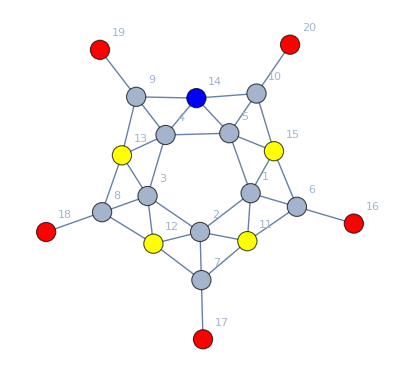

```mathematica
Graph[expMixedBisWithHair,VertexStyle->AssignColors6[{4,4,4,3,4,1,1,1,1,1},{11,12,13,14,15,16,17,18,19,20}],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```